```mathematica
Quiet[Needs["HypExp`"]];
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];
```

Epsilon divergences for perp integrals with non-zero masses

div A0: 2/((D-4) π)

div A1: 0

div A00: m10/((D-4) π)

div A11: 0

div A001: 0

div A111: 0

div A0000: m10^2/(4 (D-4) π)

div A0011: 0

div A1111: 0

div A00001: 0

div A00111: 0

div A11111: 0

div B0: 0

div B1: 0

div B00: 1/((D-4) π)

div B11: 0

div B001: -1/(2 (D-4) π)

div B111: 0

div B0000: (3 (m10+m20)-p10)/(12 (D-4) π)

div B0011: 1/(3 (D-4) π)

div B1111: 0

div B00001: (-2 m10-4 m20+p10)/(24 (D-4) π)

div B00111: -1/(4 (D-4) π)

div B11111: 0

```mathematica
$HistoryLength=2;
turnOffConditional[];

$Assumptions=0<eps<1&&0≤u≤1&&0≤v≤1&&1>beta>0;

replSingVarPlus[e_]:=e/.PlusDistribution[a_*HeavisideTheta[b_]]:>HeavisideTheta[b-beta]a+DiracDelta[b-beta]Integrate[a,{tau,1,tau}]/.PlusDistribution[a_]:>HeavisideTheta[tau-beta]a+DiracDelta[tau-beta]Integrate[a,{tau,1,tau}];

replSymmPlus[e_]:=e/.ubar->1-u/.vbar->1-v/.PlusDistribution[HeavisideTheta[u-v]a_+HeavisideTheta[v-u]b_]:> HeavisideTheta[u-v-beta]a+HeavisideTheta[v-u-beta]b+DiracDelta[u-v-beta]Integrate[a/.u->w,{w,1,u},Assumptions->1>u>v>0]-DiracDelta[v-u-beta]Integrate[b/.u->w,{w,0,u},Assumptions->1>v>u>0]

SetAttributes[multiply,HoldAll];
multiply[a_[u_,w_],b_[w_,v_]]:=Module[{tmp1,tmp2,tmp3},
tmp1=a[u,w]*b[w,v]//Expand;
tmp2=tmp1/.DiracDelta[c_]*DiracDelta[d_]:>DiracDelta[c]*someFunc[d];
tmp3=Integrate[tmp2,{w,0,1},Assumptions->0<w<1&&0<u<1&&0<v<1];
Return[tmp3/.someFunc[c_]:> DiracDelta[c]];
];

multiply[a_[u_,w_],b_[w_,v_],c_[v_,z_]]:=Module[{tmp1,tmp2,s,t},
tmp1[s_,t_]:=multiply[b[w,v],c[v,z]]/.w->s/.z->t;
tmp2:=multiply[a[u,s],tmp1[s,t]]/.t->z;
Return[tmp2];
];

anomDim2a1One=DiracDelta[u-v]*u
anomDim2a1Two=u*v*(16v-12u-3)/16
anomDim2a1Three=0
anomDim2a1BetaThree=anomDim2a1Three//replSymmPlus
anomDim2a1=anomDim2a1One+anomDim2a1Two+anomDim2a1Three

anomDim2a1One=(alphaMS*DiracDelta[u-v]/Pi)(Cf*(LQ-3/2+Log[vbar])+(Ca/2)(1+Log[v/vbar]))
anomDim2a1Two=(alphaMS/Pi)(Cf-Ca/2)ubar((u*v/(ubar*vbar))HeavisideTheta[1-u-v]+(u*v+u+v-1)HeavisideTheta[u+v-1]/(u*v) )
anomDim2a1Three=(alphaMS/Pi)(Ca/2)ubar((vbar-u*v)HeavisideTheta[u-v]/(u*vbar)+(ubar-u*v)HeavisideTheta[v-u]/(v*ubar)-PlusDistribution[HeavisideTheta[u-v](ubar/(u-v))+HeavisideTheta[v-u](vbar/(v-u))]/(ubar*vbar))
anomDim2a1BetaThree=anomDim2a1Three//replSymmPlus
anomDim2a1=anomDim2a1One+anomDim2a1Two+anomDim2a1Three//replSymmPlus
```

u u-v

1/16 u v (-12 u+16 v-3)

0

0

u u-v+1/16 u v (-12 u+16 v-3)

(α_OverBar[MS] u-v (1/2 C_A (log(v/(v̄))+1)+C_F (LQ+log(v̄)-3/2)))/π

(ū α_OverBar[MS] (C_F-C_A/2) ((u v -u-v+1)/(ū v̄)+((u v+u+v-1) u+v-1)/(u v)))/π

(ū C_A α_OverBar[MS] (-(((ū u-v)/(u-v)+(v̄ v-u)/(v-u))_+)/(ū v̄)+(v-u (ū-u v))/(ū v)+(u-v (v̄-u v))/(v̄ u)))/(2 π)

((1-u) C_A α_OverBar[MS] (-(-(v-1) log(1-u/v) u-v+β+((v-1) log((v-1)/(v-u))-u+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u))/((1-u) (1-v))+((-u v-v+1) u-v)/(u (1-v))+((u (-v)-u+1) v-u)/((1-u) v)))/(2 π)

(α_OverBar[MS] u-v (1/2 C_A (log(v/(1-v))+1)+C_F (LQ+log(1-v)-3/2)))/π+((1-u) C_A α_OverBar[MS] (-(-(v-1) log(1-u/v) u-v+β+((v-1) log((v-1)/(v-u))-u+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u))/((1-u) (1-v))+((-u v-v+1) u-v)/(u (1-v))+((u (-v)-u+1) v-u)/((1-u) v)))/(2 π)+((1-u) α_OverBar[MS] (C_F-C_A/2) ((u v -u-v+1)/((1-u) (1-v))+((u v+u+v-1) u+v-1)/(u v)))/π

```mathematica
anomDimm[uu_,vv_]:=anomDim2a1/.u->uu/.v->vv
```

```mathematica
testPsi=DiracDelta[u-v]+A*PlusDistribution[HeavisideTheta[u-v]*ubar/(u-v)+B*HeavisideTheta[v-u]*vbar/(v-u)]+ubar/(ubar^2+v^2)//replSymmPlus
testPsii[uu_,vv_]:=testPsi/.u->uu/.v->vv
anomDimm[u,w]*testPsii[w,z]
multiply[anomDimm[u,w],testPsii[w,z]]
```

A (-(B-B v) log(v/(v-u)) u-v+β+(B (1-v) -u+v-β)/(v-u)+((v-1) log((v-1)/(v-u))-u+1) u-v-β+((1-u) u-v-β)/(u-v))+u-v+(1-u)/((1-u)^2+v^2)

(A (-(B-B z) log(z/(z-w)) w-z+β+(B (1-z) -w+z-β)/(z-w)+((z-1) log((z-1)/(z-w))-w+1) -w+z+β+((1-w) w-z-β)/(w-z))+w-z+(1-w)/((1-w)^2+z^2)) ((α_OverBar[MS] u-w (1/2 C_A (log(w/(1-w))+1)+C_F (LQ+log(1-w)-3/2)))/π+((1-u) C_A α_OverBar[MS] (-(-(w-1) log(1-u/w) u-w+β+((w-1) log((w-1)/(w-u))-u+1) u-w-β+((1-u) u-w-β)/(u-w)+((1-w) -u+w-β)/(w-u))/((1-u) (1-w))+((-u w-w+1) u-w)/(u (1-w))+((u (-w)-u+1) w-u)/((1-u) w)))/(2 π)+((1-u) α_OverBar[MS] (C_F-C_A/2) ((u w -u-w+1)/((1-u) (1-w))+((u w+u+w-1) u+w-1)/(u w)))/π)

$Aborted

```mathematica
tmp1=anomDimm[u,w]*testPsii[w,z]//Expand
tmp2=tmp1/.DiracDelta[c_]*DiracDelta[d_]:>DiracDelta[c]*someFunc[d]
product=integrateTermByTerm[tmp2,{w,0,1}]
```

-(α_OverBar[MS] C_A w-z u-w-β u^2)/(2 π (1-u) (1-w))+(α_OverBar[MS] C_A w u-w-β u^2)/(2 π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A u-w-β u^2)/(2 π (1-u) (1-w) ((1-w)^2+z^2))+(A α_OverBar[MS] C_A w u-w-β -w+z+β u^2)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A u-w-β -w+z+β u^2)/(2 π (1-u) (1-w))+806+(A α_OverBar[MS] B C_F z w-z+β u+w-1 log(z/(z-w)))/(π u)-(A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)))/(2 π w u)+(A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)))/(π w u)+(A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)))/(2 π u)-(A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)))/(π u)
 |  |  |  |

(α_OverBar[MS] C_A w u-w-β u^2)/(2 π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A u-w-β u^2)/(2 π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w w-z -u-w+1 u^2)/(2 π (1-u) (1-w))-(α_OverBar[MS] C_F w w-z -u-w+1 u^2)/(π (1-u) (1-w))-(A α_OverBar[MS] C_A w^2 -w+z+β -u-w+1 u^2)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_F w^2 -w+z+β -u-w+1 u^2)/(π (1-u) (1-w))+805+(A α_OverBar[MS] B C_F z w-z+β u+w-1 log(z/(z-w)))/(π u)-(A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)))/(2 π w u)+(A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)))/(π w u)+(A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)))/(2 π u)-(A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)))/(π u)
 |  |  |  |

Integrating (α_OverBar[MS] C_A w u-w-β u^2)/(2 π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A u-w-β u^2)/(2 π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w w-z -u-w+1 u^2)/(2 π (1-u) (1-w))-(α_OverBar[MS] C_F w w-z -u-w+1 u^2)/(π (1-u) (1-w))-(A α_OverBar[MS] C_A w^2 -w+z+β -u-w+1 u^2)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_F w^2 -w+z+β -u-w+1 u^2)/(π (1-u) (1-w))+(A α_OverBar[MS] C_A w -w+z+β -u-w+1 u^2)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_F w -w+z+β -u-w+1 u^2)/(π (1-u) (1-w))-(α_OverBar[MS] C_A w^2 -u-w+1 u^2)/(2 π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_F w^2 -u-w+1 u^2)/(π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w -u-w+1 u^2)/(2 π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_F w -u-w+1 u^2)/(π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w-z w-u u^2)/(2 π (1-u))+(α_OverBar[MS] C_A w-z w-u u^2)/(2 π (1-u) w)-(A α_OverBar[MS] C_A w -w+z+β w-u u^2)/(2 π (1-u))+(A α_OverBar[MS] C_A -w+z+β w-u u^2)/(2 π (1-u) w)-(α_OverBar[MS] C_A w w-u u^2)/(2 π (1-u) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w-u u^2)/(2 π (1-u) w ((1-w)^2+z^2))-(α_OverBar[MS] C_A w-z u-w-β u^2)/(2 π (1-u) (1-w) (u-w))+(A α_OverBar[MS] C_A w -w+z+β u-w-β u^2)/(2 π (1-u) (1-w) (u-w))-(A α_OverBar[MS] C_A -w+z+β u-w-β u^2)/(2 π (1-u) (1-w) (u-w))+(α_OverBar[MS] C_A w u-w-β u^2)/(2 π (1-u) (1-w) (u-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A u-w-β u^2)/(2 π (1-u) (1-w) (u-w) ((1-w)^2+z^2))+(A α_OverBar[MS] C_A w u-w-β w-z-β u^2)/(2 π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_A u-w-β w-z-β u^2)/(2 π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_A w^2 -u-w+1 w-z-β u^2)/(2 π (1-u) (1-w) (w-z))+(A α_OverBar[MS] C_F w^2 -u-w+1 w-z-β u^2)/(π (1-u) (1-w) (w-z))+(A α_OverBar[MS] C_A w -u-w+1 w-z-β u^2)/(2 π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_F w -u-w+1 w-z-β u^2)/(π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_A w w-u w-z-β u^2)/(2 π (1-u) (w-z))+(A α_OverBar[MS] C_A w-u w-z-β u^2)/(2 π (1-u) w (w-z))+(A α_OverBar[MS] C_A w u-w-β w-z-β u^2)/(2 π (1-u) (1-w) (u-w) (w-z))-(A α_OverBar[MS] C_A u-w-β w-z-β u^2)/(2 π (1-u) (1-w) (u-w) (w-z))+(A α_OverBar[MS] B C_A z u-w-β -w+z-β u^2)/(2 π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_A u-w-β -w+z-β u^2)/(2 π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_A w -u-w+1 -w+z-β u^2)/(2 π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_F w -u-w+1 -w+z-β u^2)/(π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_A w z -u-w+1 -w+z-β u^2)/(2 π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_F w z -u-w+1 -w+z-β u^2)/(π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_A z w-u -w+z-β u^2)/(2 π (1-u) (z-w))-(A α_OverBar[MS] B C_A z w-u -w+z-β u^2)/(2 π (1-u) w (z-w))+(A α_OverBar[MS] B C_A w-u -w+z-β u^2)/(2 π (1-u) (z-w))+(A α_OverBar[MS] B C_A w-u -w+z-β u^2)/(2 π (1-u) w (z-w))+(A α_OverBar[MS] B C_A z u-w-β -w+z-β u^2)/(2 π (1-u) (1-w) (u-w) (z-w))-(A α_OverBar[MS] B C_A u-w-β -w+z-β u^2)/(2 π (1-u) (1-w) (u-w) (z-w))-(A α_OverBar[MS] C_A w -w+z+β -u-w+1 log((z-1)/(z-w)) u^2)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_F w -w+z+β -u-w+1 log((z-1)/(z-w)) u^2)/(π (1-u) (1-w))+(A α_OverBar[MS] C_A w z -w+z+β -u-w+1 log((z-1)/(z-w)) u^2)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_F w z -w+z+β -u-w+1 log((z-1)/(z-w)) u^2)/(π (1-u) (1-w))+(A α_OverBar[MS] C_A z -w+z+β w-u log((z-1)/(z-w)) u^2)/(2 π (1-u))+(A α_OverBar[MS] C_A z -w+z+β w-u log((z-1)/(z-w)) u^2)/(2 π (1-u) w)-(A α_OverBar[MS] C_A -w+z+β w-u log((z-1)/(z-w)) u^2)/(2 π (1-u))-(A α_OverBar[MS] C_A -w+z+β w-u log((z-1)/(z-w)) u^2)/(2 π (1-u) w)-(A α_OverBar[MS] C_A z -w+z+β u-w-β log((z-1)/(z-w)) u^2)/(2 π (1-u) (1-w) (u-w))+(A α_OverBar[MS] C_A -w+z+β u-w-β log((z-1)/(z-w)) u^2)/(2 π (1-u) (1-w) (u-w))-(A α_OverBar[MS] B C_A w w-z+β -u-w+1 log(z/(z-w)) u^2)/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_F w w-z+β -u-w+1 log(z/(z-w)) u^2)/(π (1-u) (1-w))+(A α_OverBar[MS] B C_A w z w-z+β -u-w+1 log(z/(z-w)) u^2)/(2 π (1-u) (1-w))-(A α_OverBar[MS] B C_F w z w-z+β -u-w+1 log(z/(z-w)) u^2)/(π (1-u) (1-w))+(A α_OverBar[MS] B C_A z w-z+β w-u log(z/(z-w)) u^2)/(2 π (1-u))+(A α_OverBar[MS] B C_A z w-z+β w-u log(z/(z-w)) u^2)/(2 π (1-u) w)-(A α_OverBar[MS] B C_A w-z+β w-u log(z/(z-w)) u^2)/(2 π (1-u))-(A α_OverBar[MS] B C_A w-z+β w-u log(z/(z-w)) u^2)/(2 π (1-u) w)-(A α_OverBar[MS] B C_A z w-z+β u-w-β log(z/(z-w)) u^2)/(2 π (1-u) (1-w) (u-w))+(A α_OverBar[MS] B C_A w-z+β u-w-β log(z/(z-w)) u^2)/(2 π (1-u) (1-w) (u-w))-(α_OverBar[MS] C_A w-z someFunc(u-w-β) u^2)/(2 π (1-u) (1-w))-(A α_OverBar[MS] B C_A z u-w-β log(z/(z-w)) someFunc(w-z+β) u^2)/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_A u-w-β log(z/(z-w)) someFunc(w-z+β) u^2)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A w u-w-β someFunc(-w+z+β) u^2)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A u-w-β someFunc(-w+z+β) u^2)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A z u-w-β log((z-1)/(z-w)) someFunc(-w+z+β) u^2)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A u-w-β log((z-1)/(z-w)) someFunc(-w+z+β) u^2)/(2 π (1-u) (1-w))-(α_OverBar[MS] C_A w u-w-β u)/(π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A u-w-β u)/(π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A w w-z -u-w+1 u)/(2 π (1-u) (1-w))+(α_OverBar[MS] C_F w w-z -u-w+1 u)/(π (1-u) (1-w))+(A α_OverBar[MS] C_A w^2 -w+z+β -u-w+1 u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_F w^2 -w+z+β -u-w+1 u)/(π (1-u) (1-w))-(A α_OverBar[MS] C_A w -w+z+β -u-w+1 u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_F w -w+z+β -u-w+1 u)/(π (1-u) (1-w))+(α_OverBar[MS] C_A w^2 -u-w+1 u)/(2 π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_F w^2 -u-w+1 u)/(π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A w -u-w+1 u)/(2 π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_F w -u-w+1 u)/(π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w w-z u-w u)/(2 π (1-w))-(A α_OverBar[MS] C_A w^2 -w+z+β u-w u)/(2 π (1-w))+(A α_OverBar[MS] C_A w -w+z+β u-w u)/(2 π (1-w))-(α_OverBar[MS] C_A w^2 u-w u)/(2 π (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w u-w u)/(2 π (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A w-z w-u u)/(2 π (1-u))-(α_OverBar[MS] C_A w-z w-u u)/(π (1-u) w)+(A α_OverBar[MS] C_A w -w+z+β w-u u)/(2 π (1-u))+(A α_OverBar[MS] C_A -w+z+β w-u u)/(2 π (1-u))-(A α_OverBar[MS] C_A -w+z+β w-u u)/(π (1-u) w)+(α_OverBar[MS] C_A w w-u u)/(2 π (1-u) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w-u u)/(2 π (1-u) ((1-w)^2+z^2))-(α_OverBar[MS] C_A w-u u)/(π (1-u) w ((1-w)^2+z^2))+(α_OverBar[MS] C_A w-z u+w-1 u)/(2 π w)-(α_OverBar[MS] C_F w-z u+w-1 u)/(π w)+(α_OverBar[MS] C_A w-z u+w-1 u)/(2 π)-(α_OverBar[MS] C_F w-z u+w-1 u)/π-(A α_OverBar[MS] C_A w -w+z+β u+w-1 u)/(2 π)+(A α_OverBar[MS] C_F w -w+z+β u+w-1 u)/π+(A α_OverBar[MS] C_A -w+z+β u+w-1 u)/(2 π w)-(A α_OverBar[MS] C_F -w+z+β u+w-1 u)/(π w)-(α_OverBar[MS] C_A w u+w-1 u)/(2 π ((1-w)^2+z^2))+(α_OverBar[MS] C_F w u+w-1 u)/(π ((1-w)^2+z^2))+(α_OverBar[MS] C_A u+w-1 u)/(2 π w ((1-w)^2+z^2))-(α_OverBar[MS] C_F u+w-1 u)/(π w ((1-w)^2+z^2))+(α_OverBar[MS] C_A w-z u-w-β u)/(π (1-u) (1-w) (u-w))-(A α_OverBar[MS] C_A w -w+z+β u-w-β u)/(π (1-u) (1-w) (u-w))+(A α_OverBar[MS] C_A -w+z+β u-w-β u)/(π (1-u) (1-w) (u-w))-(α_OverBar[MS] C_A w u-w-β u)/(π (1-u) (1-w) (u-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A u-w-β u)/(π (1-u) (1-w) (u-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A w w-z -u+w-β u)/(2 π (1-u) (1-w) (w-u))+(α_OverBar[MS] C_A w-z -u+w-β u)/(2 π (1-u) (1-w) (w-u))+(A α_OverBar[MS] C_A w^2 -w+z+β -u+w-β u)/(2 π (1-u) (1-w) (w-u))-(A α_OverBar[MS] C_A w -w+z+β -u+w-β u)/(π (1-u) (1-w) (w-u))+(A α_OverBar[MS] C_A -w+z+β -u+w-β u)/(2 π (1-u) (1-w) (w-u))+(α_OverBar[MS] C_A w^2 -u+w-β u)/(2 π (1-u) (1-w) (w-u) ((1-w)^2+z^2))-(α_OverBar[MS] C_A w -u+w-β u)/(π (1-u) (1-w) (w-u) ((1-w)^2+z^2))+(α_OverBar[MS] C_A -u+w-β u)/(2 π (1-u) (1-w) (w-u) ((1-w)^2+z^2))-(A α_OverBar[MS] C_A w u-w-β w-z-β u)/(π (1-u) (1-w) (w-z))+(A α_OverBar[MS] C_A u-w-β w-z-β u)/(π (1-u) (1-w) (w-z))+(A α_OverBar[MS] C_A w^2 -u-w+1 w-z-β u)/(2 π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_F w^2 -u-w+1 w-z-β u)/(π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_A w -u-w+1 w-z-β u)/(2 π (1-u) (1-w) (w-z))+(A α_OverBar[MS] C_F w -u-w+1 w-z-β u)/(π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_A w^2 u-w w-z-β u)/(2 π (1-w) (w-z))+(A α_OverBar[MS] C_A w u-w w-z-β u)/(2 π (1-w) (w-z))+(A α_OverBar[MS] C_A w w-u w-z-β u)/(2 π (1-u) (w-z))+(A α_OverBar[MS] C_A w-u w-z-β u)/(2 π (1-u) (w-z))-(A α_OverBar[MS] C_A w-u w-z-β u)/(π (1-u) w (w-z))-(A α_OverBar[MS] C_A w u+w-1 w-z-β u)/(2 π (w-z))+(A α_OverBar[MS] C_F w u+w-1 w-z-β u)/(π (w-z))+(A α_OverBar[MS] C_A u+w-1 w-z-β u)/(2 π w (w-z))-(A α_OverBar[MS] C_F u+w-1 w-z-β u)/(π w (w-z))-(A α_OverBar[MS] C_A w u-w-β w-z-β u)/(π (1-u) (1-w) (u-w) (w-z))+(A α_OverBar[MS] C_A u-w-β w-z-β u)/(π (1-u) (1-w) (u-w) (w-z))+(A α_OverBar[MS] C_A w^2 -u+w-β w-z-β u)/(2 π (1-u) (1-w) (w-u) (w-z))-(A α_OverBar[MS] C_A w -u+w-β w-z-β u)/(π (1-u) (1-w) (w-u) (w-z))+(A α_OverBar[MS] C_A -u+w-β w-z-β u)/(2 π (1-u) (1-w) (w-u) (w-z))-(A α_OverBar[MS] B C_A z u-w-β -w+z-β u)/(π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_A u-w-β -w+z-β u)/(π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_A w -u-w+1 -w+z-β u)/(2 π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_F w -u-w+1 -w+z-β u)/(π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_A w z -u-w+1 -w+z-β u)/(2 π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_F w z -u-w+1 -w+z-β u)/(π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_A w u-w -w+z-β u)/(2 π (1-w) (z-w))-(A α_OverBar[MS] B C_A w z u-w -w+z-β u)/(2 π (1-w) (z-w))+(A α_OverBar[MS] B C_A z w-u -w+z-β u)/(2 π (1-u) (z-w))+(A α_OverBar[MS] B C_A z w-u -w+z-β u)/(π (1-u) w (z-w))-(A α_OverBar[MS] B C_A w-u -w+z-β u)/(2 π (1-u) (z-w))-(A α_OverBar[MS] B C_A w-u -w+z-β u)/(π (1-u) w (z-w))-(A α_OverBar[MS] B C_A z u+w-1 -w+z-β u)/(2 π w (z-w))+(A α_OverBar[MS] B C_F z u+w-1 -w+z-β u)/(π w (z-w))-(A α_OverBar[MS] B C_A z u+w-1 -w+z-β u)/(2 π (z-w))+(A α_OverBar[MS] B C_F z u+w-1 -w+z-β u)/(π (z-w))+(A α_OverBar[MS] B C_A u+w-1 -w+z-β u)/(2 π w (z-w))-(A α_OverBar[MS] B C_F u+w-1 -w+z-β u)/(π w (z-w))+(A α_OverBar[MS] B C_A u+w-1 -w+z-β u)/(2 π (z-w))-(A α_OverBar[MS] B C_F u+w-1 -w+z-β u)/(π (z-w))-(A α_OverBar[MS] B C_A z u-w-β -w+z-β u)/(π (1-u) (1-w) (u-w) (z-w))+(A α_OverBar[MS] B C_A u-w-β -w+z-β u)/(π (1-u) (1-w) (u-w) (z-w))+(A α_OverBar[MS] B C_A w z -u+w-β -w+z-β u)/(2 π (1-u) (1-w) (w-u) (z-w))-(A α_OverBar[MS] B C_A z -u+w-β -w+z-β u)/(2 π (1-u) (1-w) (w-u) (z-w))-(A α_OverBar[MS] B C_A w -u+w-β -w+z-β u)/(2 π (1-u) (1-w) (w-u) (z-w))+(A α_OverBar[MS] B C_A -u+w-β -w+z-β u)/(2 π (1-u) (1-w) (w-u) (z-w))+(α_OverBar[MS] C_A w^2 u-w+β log(1-u/w) u)/(2 π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A w u-w+β log(1-u/w) u)/(π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A u-w+β log(1-u/w) u)/(2 π (1-u) (1-w) ((1-w)^2+z^2))+(A α_OverBar[MS] C_A w^2 u-w+β w-z-β log(1-u/w) u)/(2 π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_A w u-w+β w-z-β log(1-u/w) u)/(π (1-u) (1-w) (w-z))+(A α_OverBar[MS] C_A u-w+β w-z-β log(1-u/w) u)/(2 π (1-u) (1-w) (w-z))-(A α_OverBar[MS] B C_A w u-w+β -w+z-β log(1-u/w) u)/(2 π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_A w z u-w+β -w+z-β log(1-u/w) u)/(2 π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_A z u-w+β -w+z-β log(1-u/w) u)/(2 π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_A u-w+β -w+z-β log(1-u/w) u)/(2 π (1-u) (1-w) (z-w))-(α_OverBar[MS] C_A w^2 u-w-β log((w-1)/(w-u)) u)/(2 π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w u-w-β log((w-1)/(w-u)) u)/(π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A u-w-β log((w-1)/(w-u)) u)/(2 π (1-u) (1-w) ((1-w)^2+z^2))-(A α_OverBar[MS] C_A w^2 u-w-β w-z-β log((w-1)/(w-u)) u)/(2 π (1-u) (1-w) (w-z))+(A α_OverBar[MS] C_A w u-w-β w-z-β log((w-1)/(w-u)) u)/(π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_A u-w-β w-z-β log((w-1)/(w-u)) u)/(2 π (1-u) (1-w) (w-z))+(A α_OverBar[MS] B C_A w u-w-β -w+z-β log((w-1)/(w-u)) u)/(2 π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_A w z u-w-β -w+z-β log((w-1)/(w-u)) u)/(2 π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_A z u-w-β -w+z-β log((w-1)/(w-u)) u)/(2 π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_A u-w-β -w+z-β log((w-1)/(w-u)) u)/(2 π (1-u) (1-w) (z-w))+(A α_OverBar[MS] C_A w -w+z+β -u-w+1 log((z-1)/(z-w)) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_F w -w+z+β -u-w+1 log((z-1)/(z-w)) u)/(π (1-u) (1-w))-(A α_OverBar[MS] C_A w z -w+z+β -u-w+1 log((z-1)/(z-w)) u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_F w z -w+z+β -u-w+1 log((z-1)/(z-w)) u)/(π (1-u) (1-w))-(A α_OverBar[MS] C_A w -w+z+β u-w log((z-1)/(z-w)) u)/(2 π (1-w))+(A α_OverBar[MS] C_A w z -w+z+β u-w log((z-1)/(z-w)) u)/(2 π (1-w))-(A α_OverBar[MS] C_A z -w+z+β w-u log((z-1)/(z-w)) u)/(2 π (1-u))-(A α_OverBar[MS] C_A z -w+z+β w-u log((z-1)/(z-w)) u)/(π (1-u) w)+(A α_OverBar[MS] C_A -w+z+β w-u log((z-1)/(z-w)) u)/(2 π (1-u))+(A α_OverBar[MS] C_A -w+z+β w-u log((z-1)/(z-w)) u)/(π (1-u) w)+(A α_OverBar[MS] C_A z -w+z+β u+w-1 log((z-1)/(z-w)) u)/(2 π w)-(A α_OverBar[MS] C_F z -w+z+β u+w-1 log((z-1)/(z-w)) u)/(π w)+(A α_OverBar[MS] C_A z -w+z+β u+w-1 log((z-1)/(z-w)) u)/(2 π)-(A α_OverBar[MS] C_F z -w+z+β u+w-1 log((z-1)/(z-w)) u)/π-(A α_OverBar[MS] C_A -w+z+β u+w-1 log((z-1)/(z-w)) u)/(2 π w)+(A α_OverBar[MS] C_F -w+z+β u+w-1 log((z-1)/(z-w)) u)/(π w)-(A α_OverBar[MS] C_A -w+z+β u+w-1 log((z-1)/(z-w)) u)/(2 π)+(A α_OverBar[MS] C_F -w+z+β u+w-1 log((z-1)/(z-w)) u)/π+(A α_OverBar[MS] C_A z -w+z+β u-w-β log((z-1)/(z-w)) u)/(π (1-u) (1-w) (u-w))-(A α_OverBar[MS] C_A -w+z+β u-w-β log((z-1)/(z-w)) u)/(π (1-u) (1-w) (u-w))-(A α_OverBar[MS] C_A w z -w+z+β -u+w-β log((z-1)/(z-w)) u)/(2 π (1-u) (1-w) (w-u))+(A α_OverBar[MS] C_A z -w+z+β -u+w-β log((z-1)/(z-w)) u)/(2 π (1-u) (1-w) (w-u))+(A α_OverBar[MS] C_A w -w+z+β -u+w-β log((z-1)/(z-w)) u)/(2 π (1-u) (1-w) (w-u))-(A α_OverBar[MS] C_A -w+z+β -u+w-β log((z-1)/(z-w)) u)/(2 π (1-u) (1-w) (w-u))+(A α_OverBar[MS] B C_A w w-z+β -u-w+1 log(z/(z-w)) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] B C_F w w-z+β -u-w+1 log(z/(z-w)) u)/(π (1-u) (1-w))-(A α_OverBar[MS] B C_A w z w-z+β -u-w+1 log(z/(z-w)) u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_F w z w-z+β -u-w+1 log(z/(z-w)) u)/(π (1-u) (1-w))-(A α_OverBar[MS] B C_A w w-z+β u-w log(z/(z-w)) u)/(2 π (1-w))+(A α_OverBar[MS] B C_A w z w-z+β u-w log(z/(z-w)) u)/(2 π (1-w))-(A α_OverBar[MS] B C_A z w-z+β w-u log(z/(z-w)) u)/(2 π (1-u))-(A α_OverBar[MS] B C_A z w-z+β w-u log(z/(z-w)) u)/(π (1-u) w)+(A α_OverBar[MS] B C_A w-z+β w-u log(z/(z-w)) u)/(2 π (1-u))+(A α_OverBar[MS] B C_A w-z+β w-u log(z/(z-w)) u)/(π (1-u) w)+(A α_OverBar[MS] B C_A z w-z+β u+w-1 log(z/(z-w)) u)/(2 π w)-(A α_OverBar[MS] B C_F z w-z+β u+w-1 log(z/(z-w)) u)/(π w)+(A α_OverBar[MS] B C_A z w-z+β u+w-1 log(z/(z-w)) u)/(2 π)-(A α_OverBar[MS] B C_F z w-z+β u+w-1 log(z/(z-w)) u)/π-(A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)) u)/(2 π w)+(A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)) u)/(π w)-(A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)) u)/(2 π)+(A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)) u)/π+(A α_OverBar[MS] B C_A z w-z+β u-w-β log(z/(z-w)) u)/(π (1-u) (1-w) (u-w))-(A α_OverBar[MS] B C_A w-z+β u-w-β log(z/(z-w)) u)/(π (1-u) (1-w) (u-w))-(A α_OverBar[MS] B C_A w z w-z+β -u+w-β log(z/(z-w)) u)/(2 π (1-u) (1-w) (w-u))+(A α_OverBar[MS] B C_A z w-z+β -u+w-β log(z/(z-w)) u)/(2 π (1-u) (1-w) (w-u))+(A α_OverBar[MS] B C_A w w-z+β -u+w-β log(z/(z-w)) u)/(2 π (1-u) (1-w) (w-u))-(A α_OverBar[MS] B C_A w-z+β -u+w-β log(z/(z-w)) u)/(2 π (1-u) (1-w) (w-u))+(α_OverBar[MS] C_A w-z someFunc(u-w-β) u)/(π (1-u) (1-w))+(α_OverBar[MS] C_A w w-z log((w-1)/(w-u)) someFunc(u-w-β) u)/(2 π (1-u) (1-w))-(α_OverBar[MS] C_A w-z log((w-1)/(w-u)) someFunc(u-w-β) u)/(2 π (1-u) (1-w))-(α_OverBar[MS] C_A w w-z log(1-u/w) someFunc(u-w+β) u)/(2 π (1-u) (1-w))+(α_OverBar[MS] C_A w-z log(1-u/w) someFunc(u-w+β) u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_A z u-w-β log(z/(z-w)) someFunc(w-z+β) u)/(π (1-u) (1-w))-(A α_OverBar[MS] B C_A u-w-β log(z/(z-w)) someFunc(w-z+β) u)/(π (1-u) (1-w))+(A α_OverBar[MS] B C_A w u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] B C_A w z u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β) u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_A z u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] B C_A u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] B C_A w u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β) u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_A w z u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] B C_A z u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β) u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_A u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A w u-w-β someFunc(-w+z+β) u)/(π (1-u) (1-w))+(A α_OverBar[MS] C_A u-w-β someFunc(-w+z+β) u)/(π (1-u) (1-w))+(A α_OverBar[MS] C_A w^2 u-w+β log(1-u/w) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A w u-w+β log(1-u/w) someFunc(-w+z+β) u)/(π (1-u) (1-w))+(A α_OverBar[MS] C_A u-w+β log(1-u/w) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A w^2 u-w-β log((w-1)/(w-u)) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A w u-w-β log((w-1)/(w-u)) someFunc(-w+z+β) u)/(π (1-u) (1-w))-(A α_OverBar[MS] C_A u-w-β log((w-1)/(w-u)) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A z u-w-β log((z-1)/(z-w)) someFunc(-w+z+β) u)/(π (1-u) (1-w))-(A α_OverBar[MS] C_A u-w-β log((z-1)/(z-w)) someFunc(-w+z+β) u)/(π (1-u) (1-w))+(A α_OverBar[MS] C_A w u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A w z u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A z u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A w u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A w z u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A z u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β) u)/(2 π (1-u) (1-w))-(α_OverBar[MS] C_A w u-w)/(2 π ((1-w)^2+z^2))+(3 α_OverBar[MS] C_F w u-w)/(2 π ((1-w)^2+z^2))-(α_OverBar[MS] C_F LQ w u-w)/(π ((1-w)^2+z^2))+(α_OverBar[MS] C_A u-w)/(2 π ((1-w)^2+z^2))-(3 α_OverBar[MS] C_F u-w)/(2 π ((1-w)^2+z^2))+(α_OverBar[MS] C_F LQ u-w)/(π ((1-w)^2+z^2))+(α_OverBar[MS] C_A w u-w-β)/(2 π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A u-w-β)/(2 π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A w-z u-w)/(2 π (1-w))+(A α_OverBar[MS] C_A w -w+z+β u-w)/(2 π (1-w))-(A α_OverBar[MS] C_A -w+z+β u-w)/(2 π (1-w))+(α_OverBar[MS] C_A w u-w)/(2 π (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A u-w)/(2 π (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w-z w-u)/(2 π (1-u) w)-(A α_OverBar[MS] C_A -w+z+β w-u)/(2 π (1-u))+(A α_OverBar[MS] C_A -w+z+β w-u)/(2 π (1-u) w)-(α_OverBar[MS] C_A w-u)/(2 π (1-u) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w-u)/(2 π (1-u) w ((1-w)^2+z^2))-(α_OverBar[MS] C_A w-z u+w-1)/(π w)+(2 α_OverBar[MS] C_F w-z u+w-1)/(π w)-(A α_OverBar[MS] C_A -w+z+β u+w-1)/(π w)+(2 A α_OverBar[MS] C_F -w+z+β u+w-1)/(π w)+(A α_OverBar[MS] C_A -w+z+β u+w-1)/π-(2 A α_OverBar[MS] C_F -w+z+β u+w-1)/π-(α_OverBar[MS] C_A u+w-1)/(π w ((1-w)^2+z^2))+(2 α_OverBar[MS] C_F u+w-1)/(π w ((1-w)^2+z^2))+(α_OverBar[MS] C_A u+w-1)/(π ((1-w)^2+z^2))-(2 α_OverBar[MS] C_F u+w-1)/(π ((1-w)^2+z^2))-(α_OverBar[MS] C_A w-z u-w-β)/(2 π (1-u) (1-w) (u-w))+(A α_OverBar[MS] C_A w -w+z+β u-w-β)/(2 π (1-u) (1-w) (u-w))-(A α_OverBar[MS] C_A -w+z+β u-w-β)/(2 π (1-u) (1-w) (u-w))+(α_OverBar[MS] C_A w u-w-β)/(2 π (1-u) (1-w) (u-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A u-w-β)/(2 π (1-u) (1-w) (u-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w w-z -u+w-β)/(2 π (1-u) (1-w) (w-u))-(α_OverBar[MS] C_A w-z -u+w-β)/(2 π (1-u) (1-w) (w-u))-(A α_OverBar[MS] C_A w^2 -w+z+β -u+w-β)/(2 π (1-u) (1-w) (w-u))+(A α_OverBar[MS] C_A w -w+z+β -u+w-β)/(π (1-u) (1-w) (w-u))-(A α_OverBar[MS] C_A -w+z+β -u+w-β)/(2 π (1-u) (1-w) (w-u))-(α_OverBar[MS] C_A w^2 -u+w-β)/(2 π (1-u) (1-w) (w-u) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w -u+w-β)/(π (1-u) (1-w) (w-u) ((1-w)^2+z^2))-(α_OverBar[MS] C_A -u+w-β)/(2 π (1-u) (1-w) (w-u) ((1-w)^2+z^2))-(A α_OverBar[MS] C_A w u-w w-z-β)/(2 π (w-z))+(3 A α_OverBar[MS] C_F w u-w w-z-β)/(2 π (w-z))-(A α_OverBar[MS] C_F LQ w u-w w-z-β)/(π (w-z))+(A α_OverBar[MS] C_A u-w w-z-β)/(2 π (w-z))-(3 A α_OverBar[MS] C_F u-w w-z-β)/(2 π (w-z))+(A α_OverBar[MS] C_F LQ u-w w-z-β)/(π (w-z))+(A α_OverBar[MS] C_A w u-w-β w-z-β)/(2 π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_A u-w-β w-z-β)/(2 π (1-u) (1-w) (w-z))+(A α_OverBar[MS] C_A w u-w w-z-β)/(2 π (1-w) (w-z))-(A α_OverBar[MS] C_A u-w w-z-β)/(2 π (1-w) (w-z))-(A α_OverBar[MS] C_A w-u w-z-β)/(2 π (1-u) (w-z))+(A α_OverBar[MS] C_A w-u w-z-β)/(2 π (1-u) w (w-z))-(A α_OverBar[MS] C_A u+w-1 w-z-β)/(π w (w-z))+(2 A α_OverBar[MS] C_F u+w-1 w-z-β)/(π w (w-z))+(A α_OverBar[MS] C_A u+w-1 w-z-β)/(π (w-z))-(2 A α_OverBar[MS] C_F u+w-1 w-z-β)/(π (w-z))+(A α_OverBar[MS] C_A w u-w-β w-z-β)/(2 π (1-u) (1-w) (u-w) (w-z))-(A α_OverBar[MS] C_A u-w-β w-z-β)/(2 π (1-u) (1-w) (u-w) (w-z))-(A α_OverBar[MS] C_A w^2 -u+w-β w-z-β)/(2 π (1-u) (1-w) (w-u) (w-z))+(A α_OverBar[MS] C_A w -u+w-β w-z-β)/(π (1-u) (1-w) (w-u) (w-z))-(A α_OverBar[MS] C_A -u+w-β w-z-β)/(2 π (1-u) (1-w) (w-u) (w-z))-(A α_OverBar[MS] B C_A z u-w -w+z-β)/(2 π (z-w))+(3 A α_OverBar[MS] B C_F z u-w -w+z-β)/(2 π (z-w))-(A α_OverBar[MS] B C_F LQ z u-w -w+z-β)/(π (z-w))+(A α_OverBar[MS] B C_A u-w -w+z-β)/(2 π (z-w))-(3 A α_OverBar[MS] B C_F u-w -w+z-β)/(2 π (z-w))+(A α_OverBar[MS] B C_F LQ u-w -w+z-β)/(π (z-w))+(A α_OverBar[MS] B C_A z u-w-β -w+z-β)/(2 π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_A u-w-β -w+z-β)/(2 π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_A z u-w -w+z-β)/(2 π (1-w) (z-w))-(A α_OverBar[MS] B C_A u-w -w+z-β)/(2 π (1-w) (z-w))-(A α_OverBar[MS] B C_A z w-u -w+z-β)/(2 π (1-u) w (z-w))+(A α_OverBar[MS] B C_A w-u -w+z-β)/(2 π (1-u) w (z-w))+(A α_OverBar[MS] B C_A z u+w-1 -w+z-β)/(π w (z-w))-(2 A α_OverBar[MS] B C_F z u+w-1 -w+z-β)/(π w (z-w))-(A α_OverBar[MS] B C_A u+w-1 -w+z-β)/(π w (z-w))+(2 A α_OverBar[MS] B C_F u+w-1 -w+z-β)/(π w (z-w))+(A α_OverBar[MS] B C_A z u-w-β -w+z-β)/(2 π (1-u) (1-w) (u-w) (z-w))-(A α_OverBar[MS] B C_A u-w-β -w+z-β)/(2 π (1-u) (1-w) (u-w) (z-w))-(A α_OverBar[MS] B C_A w z -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))+(A α_OverBar[MS] B C_A z -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))+(A α_OverBar[MS] B C_A w -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))-(A α_OverBar[MS] B C_A -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))-(α_OverBar[MS] C_A w^2 u-w+β log(1-u/w))/(2 π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A w u-w+β log(1-u/w))/(π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A u-w+β log(1-u/w))/(2 π (1-u) (1-w) ((1-w)^2+z^2))-(A α_OverBar[MS] C_A w^2 u-w+β w-z-β log(1-u/w))/(2 π (1-u) (1-w) (w-z))+(A α_OverBar[MS] C_A w u-w+β w-z-β log(1-u/w))/(π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_A u-w+β w-z-β log(1-u/w))/(2 π (1-u) (1-w) (w-z))+(A α_OverBar[MS] B C_A w u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_A w z u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_A z u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_A u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))-(α_OverBar[MS] C_F w u-w log(1-w))/(π ((1-w)^2+z^2))+(α_OverBar[MS] C_F u-w log(1-w))/(π ((1-w)^2+z^2))-(A α_OverBar[MS] C_F w u-w w-z-β log(1-w))/(π (w-z))+(A α_OverBar[MS] C_F u-w w-z-β log(1-w))/(π (w-z))-(A α_OverBar[MS] B C_F z u-w -w+z-β log(1-w))/(π (z-w))+(A α_OverBar[MS] B C_F u-w -w+z-β log(1-w))/(π (z-w))-(α_OverBar[MS] C_A w u-w log(w/(1-w)))/(2 π ((1-w)^2+z^2))+(α_OverBar[MS] C_A u-w log(w/(1-w)))/(2 π ((1-w)^2+z^2))-(A α_OverBar[MS] C_A w u-w w-z-β log(w/(1-w)))/(2 π (w-z))+(A α_OverBar[MS] C_A u-w w-z-β log(w/(1-w)))/(2 π (w-z))-(A α_OverBar[MS] B C_A z u-w -w+z-β log(w/(1-w)))/(2 π (z-w))+(A α_OverBar[MS] B C_A u-w -w+z-β log(w/(1-w)))/(2 π (z-w))+(α_OverBar[MS] C_A w^2 u-w-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) ((1-w)^2+z^2))-(α_OverBar[MS] C_A w u-w-β log((w-1)/(w-u)))/(π (1-u) (1-w) ((1-w)^2+z^2))+(α_OverBar[MS] C_A u-w-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) ((1-w)^2+z^2))+(A α_OverBar[MS] C_A w^2 u-w-β w-z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (w-z))-(A α_OverBar[MS] C_A w u-w-β w-z-β log((w-1)/(w-u)))/(π (1-u) (1-w) (w-z))+(A α_OverBar[MS] C_A u-w-β w-z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (w-z))-(A α_OverBar[MS] B C_A w u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_A w z u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))-(A α_OverBar[MS] B C_A z u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))+(A α_OverBar[MS] B C_A u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))-(A α_OverBar[MS] C_A z -w+z+β u-w log((z-1)/(z-w)))/(2 π (1-w))+(A α_OverBar[MS] C_A -w+z+β u-w log((z-1)/(z-w)))/(2 π (1-w))+(A α_OverBar[MS] C_A z -w+z+β w-u log((z-1)/(z-w)))/(2 π (1-u) w)-(A α_OverBar[MS] C_A -w+z+β w-u log((z-1)/(z-w)))/(2 π (1-u) w)-(A α_OverBar[MS] C_A z -w+z+β u+w-1 log((z-1)/(z-w)))/(π w)+(2 A α_OverBar[MS] C_F z -w+z+β u+w-1 log((z-1)/(z-w)))/(π w)+(A α_OverBar[MS] C_A -w+z+β u+w-1 log((z-1)/(z-w)))/(π w)-(2 A α_OverBar[MS] C_F -w+z+β u+w-1 log((z-1)/(z-w)))/(π w)-(A α_OverBar[MS] C_A z -w+z+β u-w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (u-w))+(A α_OverBar[MS] C_A -w+z+β u-w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (u-w))+(A α_OverBar[MS] C_A w z -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))-(A α_OverBar[MS] C_A z -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))-(A α_OverBar[MS] C_A w -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))+(A α_OverBar[MS] C_A -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))-(A α_OverBar[MS] B C_A z w-z+β u-w log(z/(z-w)))/(2 π (1-w))+(A α_OverBar[MS] B C_A w-z+β u-w log(z/(z-w)))/(2 π (1-w))+(A α_OverBar[MS] B C_A z w-z+β w-u log(z/(z-w)))/(2 π (1-u) w)-(A α_OverBar[MS] B C_A w-z+β w-u log(z/(z-w)))/(2 π (1-u) w)-(A α_OverBar[MS] B C_A z w-z+β u+w-1 log(z/(z-w)))/(π w)+(2 A α_OverBar[MS] B C_F z w-z+β u+w-1 log(z/(z-w)))/(π w)+(A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)))/(π w)-(2 A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)))/(π w)-(A α_OverBar[MS] B C_A z w-z+β u-w-β log(z/(z-w)))/(2 π (1-u) (1-w) (u-w))+(A α_OverBar[MS] B C_A w-z+β u-w-β log(z/(z-w)))/(2 π (1-u) (1-w) (u-w))+(A α_OverBar[MS] B C_A w z w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))-(A α_OverBar[MS] B C_A z w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))-(A α_OverBar[MS] B C_A w w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))+(A α_OverBar[MS] B C_A w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))+(α_OverBar[MS] C_A u-w someFunc(w-z))/(2 π)-(3 α_OverBar[MS] C_F u-w someFunc(w-z))/(2 π)+(α_OverBar[MS] C_F LQ u-w someFunc(w-z))/π+(α_OverBar[MS] C_F u-w log(1-w) someFunc(w-z))/π+(α_OverBar[MS] C_A u-w log(w/(1-w)) someFunc(w-z))/(2 π)-(α_OverBar[MS] C_A w-z someFunc(u-w-β))/(2 π (1-u) (1-w))-(α_OverBar[MS] C_A w w-z log((w-1)/(w-u)) someFunc(u-w-β))/(2 π (1-u) (1-w))+(α_OverBar[MS] C_A w-z log((w-1)/(w-u)) someFunc(u-w-β))/(2 π (1-u) (1-w))+(α_OverBar[MS] C_A w w-z log(1-u/w) someFunc(u-w+β))/(2 π (1-u) (1-w))-(α_OverBar[MS] C_A w-z log(1-u/w) someFunc(u-w+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_A z u-w log(z/(z-w)) someFunc(w-z+β))/(2 π)-(3 A α_OverBar[MS] B C_F z u-w log(z/(z-w)) someFunc(w-z+β))/(2 π)+(A α_OverBar[MS] B C_F LQ z u-w log(z/(z-w)) someFunc(w-z+β))/π-(A α_OverBar[MS] B C_A u-w log(z/(z-w)) someFunc(w-z+β))/(2 π)+(3 A α_OverBar[MS] B C_F u-w log(z/(z-w)) someFunc(w-z+β))/(2 π)-(A α_OverBar[MS] B C_F LQ u-w log(z/(z-w)) someFunc(w-z+β))/π-(A α_OverBar[MS] B C_A z u-w-β log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_A u-w-β log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] B C_A w u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_A w z u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] B C_A z u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_A u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_F z u-w log(1-w) log(z/(z-w)) someFunc(w-z+β))/π-(A α_OverBar[MS] B C_F u-w log(1-w) log(z/(z-w)) someFunc(w-z+β))/π+(A α_OverBar[MS] B C_A z u-w log(w/(1-w)) log(z/(z-w)) someFunc(w-z+β))/(2 π)-(A α_OverBar[MS] B C_A u-w log(w/(1-w)) log(z/(z-w)) someFunc(w-z+β))/(2 π)+(A α_OverBar[MS] B C_A w u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] B C_A w z u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] B C_A z u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] B C_A u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A w u-w someFunc(-w+z+β))/(2 π)+(3 A α_OverBar[MS] C_F w u-w someFunc(-w+z+β))/(2 π)-(A α_OverBar[MS] C_F LQ w u-w someFunc(-w+z+β))/π+(A α_OverBar[MS] C_A u-w someFunc(-w+z+β))/(2 π)-(3 A α_OverBar[MS] C_F u-w someFunc(-w+z+β))/(2 π)+(A α_OverBar[MS] C_F LQ u-w someFunc(-w+z+β))/π+(A α_OverBar[MS] C_A w u-w-β someFunc(-w+z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A u-w-β someFunc(-w+z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A w^2 u-w+β log(1-u/w) someFunc(-w+z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A w u-w+β log(1-u/w) someFunc(-w+z+β))/(π (1-u) (1-w))-(A α_OverBar[MS] C_A u-w+β log(1-u/w) someFunc(-w+z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_F w u-w log(1-w) someFunc(-w+z+β))/π+(A α_OverBar[MS] C_F u-w log(1-w) someFunc(-w+z+β))/π-(A α_OverBar[MS] C_A w u-w log(w/(1-w)) someFunc(-w+z+β))/(2 π)+(A α_OverBar[MS] C_A u-w log(w/(1-w)) someFunc(-w+z+β))/(2 π)+(A α_OverBar[MS] C_A w^2 u-w-β log((w-1)/(w-u)) someFunc(-w+z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A w u-w-β log((w-1)/(w-u)) someFunc(-w+z+β))/(π (1-u) (1-w))+(A α_OverBar[MS] C_A u-w-β log((w-1)/(w-u)) someFunc(-w+z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A z u-w log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)-(3 A α_OverBar[MS] C_F z u-w log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)+(A α_OverBar[MS] C_F LQ z u-w log((z-1)/(z-w)) someFunc(-w+z+β))/π-(A α_OverBar[MS] C_A u-w log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)+(3 A α_OverBar[MS] C_F u-w log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)-(A α_OverBar[MS] C_F LQ u-w log((z-1)/(z-w)) someFunc(-w+z+β))/π-(A α_OverBar[MS] C_A z u-w-β log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A u-w-β log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A w u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A w z u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A z u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_F z u-w log(1-w) log((z-1)/(z-w)) someFunc(-w+z+β))/π-(A α_OverBar[MS] C_F u-w log(1-w) log((z-1)/(z-w)) someFunc(-w+z+β))/π+(A α_OverBar[MS] C_A z u-w log(w/(1-w)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)-(A α_OverBar[MS] C_A u-w log(w/(1-w)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)+(A α_OverBar[MS] C_A w u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A w z u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))+(A α_OverBar[MS] C_A z u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))-(A α_OverBar[MS] C_A u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))-(α_OverBar[MS] C_A w w-z u-w)/(2 π (1-w) u)+(α_OverBar[MS] C_A w-z u-w)/(2 π (1-w) u)+(A α_OverBar[MS] C_A w^2 -w+z+β u-w)/(2 π (1-w) u)-(A α_OverBar[MS] C_A w -w+z+β u-w)/(π (1-w) u)+(A α_OverBar[MS] C_A -w+z+β u-w)/(2 π (1-w) u)+(α_OverBar[MS] C_A w^2 u-w)/(2 π (1-w) ((1-w)^2+z^2) u)-(α_OverBar[MS] C_A w u-w)/(π (1-w) ((1-w)^2+z^2) u)+(α_OverBar[MS] C_A u-w)/(2 π (1-w) ((1-w)^2+z^2) u)+(α_OverBar[MS] C_A w-z u+w-1)/(2 π w u)-(α_OverBar[MS] C_F w-z u+w-1)/(π w u)-(α_OverBar[MS] C_A w-z u+w-1)/(2 π u)+(α_OverBar[MS] C_F w-z u+w-1)/(π u)+(A α_OverBar[MS] C_A w -w+z+β u+w-1)/(2 π u)-(A α_OverBar[MS] C_F w -w+z+β u+w-1)/(π u)+(A α_OverBar[MS] C_A -w+z+β u+w-1)/(2 π w u)-(A α_OverBar[MS] C_F -w+z+β u+w-1)/(π w u)-(A α_OverBar[MS] C_A -w+z+β u+w-1)/(π u)+(2 A α_OverBar[MS] C_F -w+z+β u+w-1)/(π u)+(α_OverBar[MS] C_A w u+w-1)/(2 π ((1-w)^2+z^2) u)-(α_OverBar[MS] C_F w u+w-1)/(π ((1-w)^2+z^2) u)+(α_OverBar[MS] C_A u+w-1)/(2 π w ((1-w)^2+z^2) u)-(α_OverBar[MS] C_F u+w-1)/(π w ((1-w)^2+z^2) u)-(α_OverBar[MS] C_A u+w-1)/(π ((1-w)^2+z^2) u)+(2 α_OverBar[MS] C_F u+w-1)/(π ((1-w)^2+z^2) u)+(A α_OverBar[MS] C_A w^2 u-w w-z-β)/(2 π (1-w) (w-z) u)-(A α_OverBar[MS] C_A w u-w w-z-β)/(π (1-w) (w-z) u)+(A α_OverBar[MS] C_A u-w w-z-β)/(2 π (1-w) (w-z) u)+(A α_OverBar[MS] C_A w u+w-1 w-z-β)/(2 π (w-z) u)-(A α_OverBar[MS] C_F w u+w-1 w-z-β)/(π (w-z) u)+(A α_OverBar[MS] C_A u+w-1 w-z-β)/(2 π w (w-z) u)-(A α_OverBar[MS] C_F u+w-1 w-z-β)/(π w (w-z) u)-(A α_OverBar[MS] C_A u+w-1 w-z-β)/(π (w-z) u)+(2 A α_OverBar[MS] C_F u+w-1 w-z-β)/(π (w-z) u)-(A α_OverBar[MS] B C_A w u-w -w+z-β)/(2 π (1-w) (z-w) u)+(A α_OverBar[MS] B C_A w z u-w -w+z-β)/(2 π (1-w) (z-w) u)-(A α_OverBar[MS] B C_A z u-w -w+z-β)/(2 π (1-w) (z-w) u)+(A α_OverBar[MS] B C_A u-w -w+z-β)/(2 π (1-w) (z-w) u)-(A α_OverBar[MS] B C_A z u+w-1 -w+z-β)/(2 π w (z-w) u)+(A α_OverBar[MS] B C_F z u+w-1 -w+z-β)/(π w (z-w) u)+(A α_OverBar[MS] B C_A z u+w-1 -w+z-β)/(2 π (z-w) u)-(A α_OverBar[MS] B C_F z u+w-1 -w+z-β)/(π (z-w) u)+(A α_OverBar[MS] B C_A u+w-1 -w+z-β)/(2 π w (z-w) u)-(A α_OverBar[MS] B C_F u+w-1 -w+z-β)/(π w (z-w) u)-(A α_OverBar[MS] B C_A u+w-1 -w+z-β)/(2 π (z-w) u)+(A α_OverBar[MS] B C_F u+w-1 -w+z-β)/(π (z-w) u)+(A α_OverBar[MS] C_A w -w+z+β u-w log((z-1)/(z-w)))/(2 π (1-w) u)-(A α_OverBar[MS] C_A w z -w+z+β u-w log((z-1)/(z-w)))/(2 π (1-w) u)+(A α_OverBar[MS] C_A z -w+z+β u-w log((z-1)/(z-w)))/(2 π (1-w) u)-(A α_OverBar[MS] C_A -w+z+β u-w log((z-1)/(z-w)))/(2 π (1-w) u)+(A α_OverBar[MS] C_A z -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π w u)-(A α_OverBar[MS] C_F z -w+z+β u+w-1 log((z-1)/(z-w)))/(π w u)-(A α_OverBar[MS] C_A z -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π u)+(A α_OverBar[MS] C_F z -w+z+β u+w-1 log((z-1)/(z-w)))/(π u)-(A α_OverBar[MS] C_A -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π w u)+(A α_OverBar[MS] C_F -w+z+β u+w-1 log((z-1)/(z-w)))/(π w u)+(A α_OverBar[MS] C_A -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π u)-(A α_OverBar[MS] C_F -w+z+β u+w-1 log((z-1)/(z-w)))/(π u)+(A α_OverBar[MS] B C_A w w-z+β u-w log(z/(z-w)))/(2 π (1-w) u)-(A α_OverBar[MS] B C_A w z w-z+β u-w log(z/(z-w)))/(2 π (1-w) u)+(A α_OverBar[MS] B C_A z w-z+β u-w log(z/(z-w)))/(2 π (1-w) u)-(A α_OverBar[MS] B C_A w-z+β u-w log(z/(z-w)))/(2 π (1-w) u)+(A α_OverBar[MS] B C_A z w-z+β u+w-1 log(z/(z-w)))/(2 π w u)-(A α_OverBar[MS] B C_F z w-z+β u+w-1 log(z/(z-w)))/(π w u)-(A α_OverBar[MS] B C_A z w-z+β u+w-1 log(z/(z-w)))/(2 π u)+(A α_OverBar[MS] B C_F z w-z+β u+w-1 log(z/(z-w)))/(π u)-(A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)))/(2 π w u)+(A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)))/(π w u)+(A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)))/(2 π u)-(A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)))/(π u)

Integrating 550 terms.

Term 1 : (α_OverBar[MS] C_A u-w)/(2 π ((1-w)^2+z^2))

1 : (α_OverBar[MS] C_A)/(2 π (u^2-2 u+z^2+1))

Term 2 : -(3 α_OverBar[MS] C_F u-w)/(2 π ((1-w)^2+z^2))

2 : -(3 α_OverBar[MS] C_F)/(2 π (u^2-2 u+z^2+1))

Term 3 : (α_OverBar[MS] C_F LQ u-w)/(π ((1-w)^2+z^2))

3 : (α_OverBar[MS] C_F LQ)/(π (u^2-2 u+z^2+1))

Term 4 : -(α_OverBar[MS] C_A w u-w)/(2 π ((1-w)^2+z^2))

4 : -(α_OverBar[MS] C_A u)/(2 π (u^2-2 u+z^2+1))

Term 5 : (3 α_OverBar[MS] C_F w u-w)/(2 π ((1-w)^2+z^2))

5 : (3 α_OverBar[MS] C_F u)/(2 π (u^2-2 u+z^2+1))

Term 6 : -(α_OverBar[MS] C_F LQ w u-w)/(π ((1-w)^2+z^2))

6 : -(α_OverBar[MS] C_F LQ u)/(π (u^2-2 u+z^2+1))

Term 7 : -(α_OverBar[MS] C_A u-w-β)/(2 π (1-u) (1-w) ((1-w)^2+z^2))

7 : -(α_OverBar[MS] C_A u-β)/(2 π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 8 : (α_OverBar[MS] C_A u u-w-β)/(π (1-u) (1-w) ((1-w)^2+z^2))

8 : (α_OverBar[MS] C_A u u-β)/(π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 9 : -(α_OverBar[MS] C_A u^2 u-w-β)/(2 π (1-u) (1-w) ((1-w)^2+z^2))

9 : -(α_OverBar[MS] C_A u^2 u-β)/(2 π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 10 : (α_OverBar[MS] C_A w u-w-β)/(2 π (1-u) (1-w) ((1-w)^2+z^2))

10 : (α_OverBar[MS] C_A (u-β) u-β)/(2 π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 11 : -(α_OverBar[MS] C_A u w u-w-β)/(π (1-u) (1-w) ((1-w)^2+z^2))

11 : -(α_OverBar[MS] C_A u (u-β) u-β)/(π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 12 : (α_OverBar[MS] C_A u^2 w u-w-β)/(2 π (1-u) (1-w) ((1-w)^2+z^2))

12 : (α_OverBar[MS] C_A u^2 (u-β) u-β)/(2 π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 13 : -(α_OverBar[MS] C_A u w -u-w+1)/(2 π (1-u) (1-w) ((1-w)^2+z^2))

13 : -(α_OverBar[MS] C_A u (2 z cot^-1(z)-2 z tan^-1(u/z)+2 log(u)+log(z^2+1)-log(u^2+z^2)))/(4 π (u-1) z^2)

Term 14 : (α_OverBar[MS] C_F u w -u-w+1)/(π (1-u) (1-w) ((1-w)^2+z^2))

14 : (α_OverBar[MS] C_F u (2 z cot^-1(z)-2 z tan^-1(u/z)+2 log(u)+log(z^2+1)-log(u^2+z^2)))/(2 π (u-1) z^2)

Term 15 : (α_OverBar[MS] C_A u^2 w -u-w+1)/(2 π (1-u) (1-w) ((1-w)^2+z^2))

15 : (α_OverBar[MS] C_A u^2 (2 z cot^-1(z)-2 z tan^-1(u/z)+2 log(u)+log(z^2+1)-log(u^2+z^2)))/(4 π (u-1) z^2)

Term 16 : -(α_OverBar[MS] C_F u^2 w -u-w+1)/(π (1-u) (1-w) ((1-w)^2+z^2))

16 : -(α_OverBar[MS] C_F u^2 (2 z cot^-1(z)-2 z tan^-1(u/z)+2 log(u)+log(z^2+1)-log(u^2+z^2)))/(2 π (u-1) z^2)

Term 17 : (α_OverBar[MS] C_A u w^2 -u-w+1)/(2 π (1-u) (1-w) ((1-w)^2+z^2))

17 : (α_OverBar[MS] C_A u (-log(z^2+1) z^2+log(u^2+z^2) z^2+4 tan^-1(1/z) z-4 tan^-1(u/z) z+2 log(u)+log(z^2+1)-log(u^2+z^2)))/(4 π (u-1) z^2)

Term 18 : -(α_OverBar[MS] C_F u w^2 -u-w+1)/(π (1-u) (1-w) ((1-w)^2+z^2))

18 : (α_OverBar[MS] C_F u (log(z^2+1) z^2-log(u^2+z^2) z^2-4 tan^-1(1/z) z+4 tan^-1(u/z) z-2 log(u)-log(z^2+1)+log(u^2+z^2)))/(2 π (u-1) z^2)

Term 19 : -(α_OverBar[MS] C_A u^2 w^2 -u-w+1)/(2 π (1-u) (1-w) ((1-w)^2+z^2))

19 : (α_OverBar[MS] C_A u^2 (log(z^2+1) z^2-log(u^2+z^2) z^2-4 tan^-1(1/z) z+4 tan^-1(u/z) z-2 log(u)-log(z^2+1)+log(u^2+z^2)))/(4 π (u-1) z^2)

Term 20 : (α_OverBar[MS] C_F u^2 w^2 -u-w+1)/(π (1-u) (1-w) ((1-w)^2+z^2))

20 : (α_OverBar[MS] C_F u^2 (-log(z^2+1) z^2+log(u^2+z^2) z^2+4 tan^-1(1/z) z-4 tan^-1(u/z) z+2 log(u)+log(z^2+1)-log(u^2+z^2)))/(2 π (u-1) z^2)

Term 21 : -(α_OverBar[MS] C_A u w w-z -u-w+1)/(2 π (1-u) (1-w))

21 : -(α_OverBar[MS] C_A u z -u-z+1)/(2 π (u-1) (z-1))

Term 22 : (α_OverBar[MS] C_F u w w-z -u-w+1)/(π (1-u) (1-w))

22 : (α_OverBar[MS] C_F u z -u-z+1)/(π (u-1) (z-1))

Term 23 : (α_OverBar[MS] C_A u^2 w w-z -u-w+1)/(2 π (1-u) (1-w))

23 : (α_OverBar[MS] C_A u^2 z -u-z+1)/(2 π (u-1) (z-1))

Term 24 : -(α_OverBar[MS] C_F u^2 w w-z -u-w+1)/(π (1-u) (1-w))

24 : -(α_OverBar[MS] C_F u^2 z -u-z+1)/(π (u-1) (z-1))

Term 25 : -(A α_OverBar[MS] C_A u w -w+z+β -u-w+1)/(2 π (1-u) (1-w))

25 : -(A α_OverBar[MS] C_A u (z+β) -z-β+1,-u-z-β+1)/(2 π (u-1) (z+β-1))

Term 26 : (A α_OverBar[MS] C_F u w -w+z+β -u-w+1)/(π (1-u) (1-w))

26 : (A α_OverBar[MS] C_F u (z+β) -z-β+1,-u-z-β+1)/(π (u-1) (z+β-1))

Term 27 : (A α_OverBar[MS] C_A u^2 w -w+z+β -u-w+1)/(2 π (1-u) (1-w))

27 : (A α_OverBar[MS] C_A u^2 (z+β) -z-β+1,-u-z-β+1)/(2 π (u-1) (z+β-1))

Term 28 : -(A α_OverBar[MS] C_F u^2 w -w+z+β -u-w+1)/(π (1-u) (1-w))

28 : -(A α_OverBar[MS] C_F u^2 (z+β) -z-β+1,-u-z-β+1)/(π (u-1) (z+β-1))

Term 29 : (A α_OverBar[MS] C_A u w^2 -w+z+β -u-w+1)/(2 π (1-u) (1-w))

29 : (A α_OverBar[MS] C_A u (z+β)^2 -z-β+1,-u-z-β+1)/(2 π (u-1) (z+β-1))

Term 30 : -(A α_OverBar[MS] C_F u w^2 -w+z+β -u-w+1)/(π (1-u) (1-w))

30 : -(A α_OverBar[MS] C_F u (z+β)^2 -z-β+1,-u-z-β+1)/(π (u-1) (z+β-1))

Term 31 : -(A α_OverBar[MS] C_A u^2 w^2 -w+z+β -u-w+1)/(2 π (1-u) (1-w))

31 : -(A α_OverBar[MS] C_A u^2 (z+β)^2 -z-β+1,-u-z-β+1)/(2 π (u-1) (z+β-1))

Term 32 : (A α_OverBar[MS] C_F u^2 w^2 -w+z+β -u-w+1)/(π (1-u) (1-w))

32 : (A α_OverBar[MS] C_F u^2 (z+β)^2 -z-β+1,-u-z-β+1)/(π (u-1) (z+β-1))

Term 33 : -(α_OverBar[MS] C_A u-w)/(2 π (1-w) ((1-w)^2+z^2))

33 : (α_OverBar[MS] C_A (2 log(1-u)+log(z^2+1)-log((u-1)^2+z^2)))/(4 π z^2)

Term 34 : (α_OverBar[MS] C_A u-w)/(2 π u (1-w) ((1-w)^2+z^2))

34 : -(α_OverBar[MS] C_A (2 log(1-u)+log(z^2+1)-log((u-1)^2+z^2)))/(4 π u z^2)

Term 35 : (α_OverBar[MS] C_A w u-w)/(2 π (1-w) ((1-w)^2+z^2))

35 : -(α_OverBar[MS] C_A (2 z (cot^-1(z)+tan^-1((u-1)/z))+2 log(1-u)+log(z^2+1)-log((u-1)^2+z^2)))/(4 π z^2)

Term 36 : -(α_OverBar[MS] C_A w u-w)/(π u (1-w) ((1-w)^2+z^2))

36 : (α_OverBar[MS] C_A (2 z (cot^-1(z)+tan^-1((u-1)/z))+2 log(1-u)+log(z^2+1)-log((u-1)^2+z^2)))/(2 π u z^2)

Term 37 : (α_OverBar[MS] C_A u w u-w)/(2 π (1-w) ((1-w)^2+z^2))

37 : -(α_OverBar[MS] C_A u (2 z (cot^-1(z)+tan^-1((u-1)/z))+2 log(1-u)+log(z^2+1)-log((u-1)^2+z^2)))/(4 π z^2)

Term 38 : (α_OverBar[MS] C_A w^2 u-w)/(2 π u (1-w) ((1-w)^2+z^2))

38 : -(α_OverBar[MS] C_A (4 z (cot^-1(z)+tan^-1((u-1)/z))+2 log(1-u)+(z^2-1) log(((u-2) u)/(z^2+1)+1)))/(4 π u z^2)

Term 39 : -(α_OverBar[MS] C_A u w^2 u-w)/(2 π (1-w) ((1-w)^2+z^2))

39 : (α_OverBar[MS] C_A u (4 z (cot^-1(z)+tan^-1((u-1)/z))+2 log(1-u)+(z^2-1) log(((u-2) u)/(z^2+1)+1)))/(4 π z^2)

Term 40 : -(α_OverBar[MS] C_A w-z u-w)/(2 π (1-w))

40 : -(α_OverBar[MS] C_A u-z)/(2 π-2 π z)

Term 41 : (α_OverBar[MS] C_A w-z u-w)/(2 π u (1-w))

41 : (α_OverBar[MS] C_A u-z)/(2 π u-2 π u z)

Term 42 : -(α_OverBar[MS] C_A w w-z u-w)/(2 π u (1-w))

42 : -(α_OverBar[MS] C_A z u-z)/(2 π u-2 π u z)

Term 43 : (α_OverBar[MS] C_A u w w-z u-w)/(2 π (1-w))

43 : (α_OverBar[MS] C_A u z u-z)/(2 π-2 π z)

Term 44 : -(A α_OverBar[MS] C_A -w+z+β u-w)/(2 π (1-w))

44 : (A α_OverBar[MS] C_A -z-β+1,u-z-β)/(2 π (z+β-1))

Term 45 : (A α_OverBar[MS] C_A -w+z+β u-w)/(2 π u (1-w))

45 : (A α_OverBar[MS] C_A -z-β+1,u-z-β)/(-2 π z u-2 π β u+2 π u)

Term 46 : (A α_OverBar[MS] C_A w -w+z+β u-w)/(2 π (1-w))

46 : -(A α_OverBar[MS] C_A (z+β) -z-β+1,u-z-β)/(2 π (z+β-1))

Term 47 : -(A α_OverBar[MS] C_A w -w+z+β u-w)/(π u (1-w))

47 : (A α_OverBar[MS] C_A (z+β) -z-β+1,u-z-β)/(π u (z+β-1))

Term 48 : (A α_OverBar[MS] C_A u w -w+z+β u-w)/(2 π (1-w))

48 : -(A α_OverBar[MS] C_A u (z+β) -z-β+1,u-z-β)/(2 π (z+β-1))

Term 49 : (A α_OverBar[MS] C_A w^2 -w+z+β u-w)/(2 π u (1-w))

49 : -(A α_OverBar[MS] C_A (z+β)^2 -z-β+1,u-z-β)/(2 π u (z+β-1))

Term 50 : -(A α_OverBar[MS] C_A u w^2 -w+z+β u-w)/(2 π (1-w))

50 : (A α_OverBar[MS] C_A u (z+β)^2 -z-β+1,u-z-β)/(2 π (z+β-1))

Term 51 : -(α_OverBar[MS] C_A w-u)/(2 π (1-u) ((1-w)^2+z^2))

51 : (α_OverBar[MS] C_A tan^-1((u-1)/z))/(2 π z-2 π u z)

Term 52 : (α_OverBar[MS] C_A u w-u)/(2 π (1-u) ((1-w)^2+z^2))

52 : (α_OverBar[MS] C_A u tan^-1((1-u)/z))/(2 π z-2 π u z)

Term 53 : (α_OverBar[MS] C_A w-u)/(2 π (1-u) w ((1-w)^2+z^2))

53 : -(α_OverBar[MS] C_A (z log((u-1)^2+z^2)-2 (tan^-1((u-1)/z)+z log(u z))))/(4 π (u-1) (z^3+z))

Term 54 : -(α_OverBar[MS] C_A u w-u)/(π (1-u) w ((1-w)^2+z^2))

54 : (α_OverBar[MS] C_A u (z log((u-1)^2+z^2)-2 (tan^-1((u-1)/z)+z log(u z))))/(2 π (u-1) (z^3+z))

Term 55 : (α_OverBar[MS] C_A u^2 w-u)/(2 π (1-u) w ((1-w)^2+z^2))

55 : -(α_OverBar[MS] C_A u^2 (z log((u-1)^2+z^2)-2 (tan^-1((u-1)/z)+z log(u z))))/(4 π (u-1) (z^3+z))

Term 56 : (α_OverBar[MS] C_A u w w-u)/(2 π (1-u) ((1-w)^2+z^2))

56 : -(α_OverBar[MS] C_A u ((tan^-1((1-u)/z))/z+log(z)-1/2 log(u^2-2 u+z^2+1)))/(2 π (u-1))

Term 57 : -(α_OverBar[MS] C_A u^2 w w-u)/(2 π (1-u) ((1-w)^2+z^2))

57 : (α_OverBar[MS] C_A u^2 ((tan^-1((1-u)/z))/z+log(z)-1/2 log(u^2-2 u+z^2+1)))/(2 π (u-1))

Term 58 : -(α_OverBar[MS] C_A u w-z w-u)/(2 π (1-u))

58 : -(α_OverBar[MS] C_A u z-u)/(2 π-2 π u)

Term 59 : (α_OverBar[MS] C_A u^2 w-z w-u)/(2 π (1-u))

59 : (α_OverBar[MS] C_A u^2 z-u)/(2 π-2 π u)

Term 60 : (α_OverBar[MS] C_A w-z w-u)/(2 π (1-u) w)

60 : (α_OverBar[MS] C_A z-u)/(2 π z-2 π u z)

Term 61 : -(α_OverBar[MS] C_A u w-z w-u)/(π (1-u) w)

61 : -(α_OverBar[MS] C_A u z-u)/(π z-π u z)

Term 62 : (α_OverBar[MS] C_A u^2 w-z w-u)/(2 π (1-u) w)

62 : (α_OverBar[MS] C_A u^2 z-u)/(2 π z-2 π u z)

Term 63 : -(A α_OverBar[MS] C_A -w+z+β w-u)/(2 π (1-u))

63 : -(A α_OverBar[MS] C_A -z-β+1,-u+z+β)/(2 π-2 π u)

Term 64 : (A α_OverBar[MS] C_A u -w+z+β w-u)/(2 π (1-u))

64 : (A α_OverBar[MS] C_A u -z-β+1,-u+z+β)/(2 π-2 π u)

Term 65 : (A α_OverBar[MS] C_A -w+z+β w-u)/(2 π (1-u) w)

65 : -(A α_OverBar[MS] C_A -z-β+1,-u+z+β)/(2 π (u-1) (z+β))

Term 66 : -(A α_OverBar[MS] C_A u -w+z+β w-u)/(π (1-u) w)

66 : (A α_OverBar[MS] C_A u -z-β+1,-u+z+β)/(π (u-1) (z+β))

Term 67 : (A α_OverBar[MS] C_A u^2 -w+z+β w-u)/(2 π (1-u) w)

67 : -(A α_OverBar[MS] C_A u^2 -z-β+1,-u+z+β)/(2 π (u-1) (z+β))

Term 68 : (A α_OverBar[MS] C_A u w -w+z+β w-u)/(2 π (1-u))

68 : (A α_OverBar[MS] C_A u (z+β) -z-β+1,-u+z+β)/(2 π-2 π u)

Term 69 : -(A α_OverBar[MS] C_A u^2 w -w+z+β w-u)/(2 π (1-u))

69 : (A α_OverBar[MS] C_A u^2 (z+β) -z-β+1,-u+z+β)/(2 π (u-1))

Term 70 : (α_OverBar[MS] C_A u+w-1)/(π ((1-w)^2+z^2))

70 : (α_OverBar[MS] C_A tan^-1(u/z))/(π z)

Term 71 : -(2 α_OverBar[MS] C_F u+w-1)/(π ((1-w)^2+z^2))

71 : -(2 α_OverBar[MS] C_F tan^-1(u/z))/(π z)

Term 72 : -(α_OverBar[MS] C_A u+w-1)/(π u ((1-w)^2+z^2))

72 : -(α_OverBar[MS] C_A tan^-1(u/z))/(π u z)

Term 73 : (2 α_OverBar[MS] C_F u+w-1)/(π u ((1-w)^2+z^2))

73 : (2 α_OverBar[MS] C_F tan^-1(u/z))/(π u z)

Term 74 : -(α_OverBar[MS] C_A u+w-1)/(π w ((1-w)^2+z^2))

74 : -(α_OverBar[MS] C_A (2 tan^-1(u/z)+z (log(u^2+z^2)-2 log(z-u z))))/(2 π (z^3+z))

Term 75 : (2 α_OverBar[MS] C_F u+w-1)/(π w ((1-w)^2+z^2))

75 : (α_OverBar[MS] C_F (2 tan^-1(u/z)+z (log(u^2+z^2)-2 log(z-u z))))/(π (z^3+z))

Term 76 : (α_OverBar[MS] C_A u+w-1)/(2 π u w ((1-w)^2+z^2))

76 : (α_OverBar[MS] C_A (2 tan^-1(u/z)+z (log(u^2+z^2)-2 log(z-u z))))/(4 π u (z^3+z))

Term 77 : -(α_OverBar[MS] C_F u+w-1)/(π u w ((1-w)^2+z^2))

77 : -(α_OverBar[MS] C_F (2 tan^-1(u/z)+z (log(u^2+z^2)-2 log(z-u z))))/(2 π u (z^3+z))

Term 78 : (α_OverBar[MS] C_A u u+w-1)/(2 π w ((1-w)^2+z^2))

78 : (α_OverBar[MS] C_A u (2 tan^-1(u/z)+z (log(u^2+z^2)-2 log(z-u z))))/(4 π (z^3+z))

Term 79 : -(α_OverBar[MS] C_F u u+w-1)/(π w ((1-w)^2+z^2))

79 : -(α_OverBar[MS] C_F u (2 tan^-1(u/z)+z (log(u^2+z^2)-2 log(z-u z))))/(2 π (z^3+z))

Term 80 : (α_OverBar[MS] C_A w u+w-1)/(2 π u ((1-w)^2+z^2))

80 : (α_OverBar[MS] C_A ((tan^-1(u/z))/z+log(z)-1/2 log(u^2+z^2)))/(2 π u)

Term 81 : -(α_OverBar[MS] C_F w u+w-1)/(π u ((1-w)^2+z^2))

81 : -(α_OverBar[MS] C_F ((tan^-1(u/z))/z+log(z)-1/2 log(u^2+z^2)))/(π u)

Term 82 : -(α_OverBar[MS] C_A u w u+w-1)/(2 π ((1-w)^2+z^2))

82 : -(α_OverBar[MS] C_A u ((tan^-1(u/z))/z+log(z)-1/2 log(u^2+z^2)))/(2 π)

Term 83 : (α_OverBar[MS] C_F u w u+w-1)/(π ((1-w)^2+z^2))

83 : (α_OverBar[MS] C_F u ((tan^-1(u/z))/z+log(z)-1/2 log(u^2+z^2)))/π

Term 84 : -(α_OverBar[MS] C_A w-z u+w-1)/(2 π u)

84 : -(α_OverBar[MS] C_A u+z-1)/(2 π u)

Term 85 : (α_OverBar[MS] C_F w-z u+w-1)/(π u)

85 : (α_OverBar[MS] C_F u+z-1)/(π u)

Term 86 : (α_OverBar[MS] C_A u w-z u+w-1)/(2 π)

86 : (α_OverBar[MS] C_A u u+z-1)/(2 π)

Term 87 : -(α_OverBar[MS] C_F u w-z u+w-1)/π

87 : -(α_OverBar[MS] C_F u u+z-1)/π

Term 88 : -(α_OverBar[MS] C_A w-z u+w-1)/(π w)

88 : -(α_OverBar[MS] C_A u+z-1)/(π z)

Term 89 : (2 α_OverBar[MS] C_F w-z u+w-1)/(π w)

89 : (2 α_OverBar[MS] C_F u+z-1)/(π z)

Term 90 : (α_OverBar[MS] C_A w-z u+w-1)/(2 π u w)

90 : (α_OverBar[MS] C_A u+z-1)/(2 π u z)

Term 91 : -(α_OverBar[MS] C_F w-z u+w-1)/(π u w)

91 : -(α_OverBar[MS] C_F u+z-1)/(π u z)

Term 92 : (α_OverBar[MS] C_A u w-z u+w-1)/(2 π w)

92 : (α_OverBar[MS] C_A u u+z-1)/(2 π z)

Term 93 : -(α_OverBar[MS] C_F u w-z u+w-1)/(π w)

93 : -(α_OverBar[MS] C_F u u+z-1)/(π z)

Term 94 : (A α_OverBar[MS] C_A -w+z+β u+w-1)/π

94 : (A α_OverBar[MS] C_A -z-β+1,u+z+β-1)/π

Term 95 : -(2 A α_OverBar[MS] C_F -w+z+β u+w-1)/π

95 : -(2 A α_OverBar[MS] C_F -z-β+1,u+z+β-1)/π

Term 96 : -(A α_OverBar[MS] C_A -w+z+β u+w-1)/(π u)

96 : -(A α_OverBar[MS] C_A -z-β+1,u+z+β-1)/(π u)

Term 97 : (2 A α_OverBar[MS] C_F -w+z+β u+w-1)/(π u)

97 : (2 A α_OverBar[MS] C_F -z-β+1,u+z+β-1)/(π u)

Term 98 : -(A α_OverBar[MS] C_A -w+z+β u+w-1)/(π w)

98 : -(A α_OverBar[MS] C_A -z-β+1,u+z+β-1)/(π (z+β))

Term 99 : (2 A α_OverBar[MS] C_F -w+z+β u+w-1)/(π w)

99 : (2 A α_OverBar[MS] C_F -z-β+1,u+z+β-1)/(π (z+β))

Term 100 : (A α_OverBar[MS] C_A -w+z+β u+w-1)/(2 π u w)

100 : (A α_OverBar[MS] C_A -z-β+1,u+z+β-1)/(2 π u z+2 π u β)

Term 101 : -(A α_OverBar[MS] C_F -w+z+β u+w-1)/(π u w)

101 : -(A α_OverBar[MS] C_F -z-β+1,u+z+β-1)/(π u z+π u β)

Term 102 : (A α_OverBar[MS] C_A u -w+z+β u+w-1)/(2 π w)

102 : (A α_OverBar[MS] C_A u -z-β+1,u+z+β-1)/(2 π z+2 π β)

Term 103 : -(A α_OverBar[MS] C_F u -w+z+β u+w-1)/(π w)

103 : -(A α_OverBar[MS] C_F u -z-β+1,u+z+β-1)/(π (z+β))

Term 104 : (A α_OverBar[MS] C_A w -w+z+β u+w-1)/(2 π u)

104 : (A α_OverBar[MS] C_A (z+β) -z-β+1,u+z+β-1)/(2 π u)

Term 105 : -(A α_OverBar[MS] C_F w -w+z+β u+w-1)/(π u)

105 : -(A α_OverBar[MS] C_F (z+β) -z-β+1,u+z+β-1)/(π u)

Term 106 : -(A α_OverBar[MS] C_A u w -w+z+β u+w-1)/(2 π)

106 : -(A α_OverBar[MS] C_A u (z+β) -z-β+1,u+z+β-1)/(2 π)

Term 107 : (A α_OverBar[MS] C_F u w -w+z+β u+w-1)/π

107 : (A α_OverBar[MS] C_F u (z+β) -z-β+1,u+z+β-1)/π

Term 108 : -(α_OverBar[MS] C_A u-w-β)/(2 π (1-u) (1-w) (u-w) ((1-w)^2+z^2))

108 : 0

Term 109 : (α_OverBar[MS] C_A u u-w-β)/(π (1-u) (1-w) (u-w) ((1-w)^2+z^2))

109 : 0

Term 110 : -(α_OverBar[MS] C_A u^2 u-w-β)/(2 π (1-u) (1-w) (u-w) ((1-w)^2+z^2))

110 : 0

Term 111 : (α_OverBar[MS] C_A w u-w-β)/(2 π (1-u) (1-w) (u-w) ((1-w)^2+z^2))

111 : Piecewise[{{(α_OverBar[MS] C_A (log(z^2+1) u^2+2 log(-u+β+1) u^2-log(u^2-2 (β+1) u+z^2+(β+1)^2) u^2+2 (u-1) z tan^-1(1/z) u-2 (u-1) z tan^-1((-u+β+1)/z) u+2 z^2 log(u) u-z^2 log(z^2+1) u-2 log(z^2+1) u-2 z^2 log(β) u-4 log(-u+β+1) u+z^2 log(u^2-2 (β+1) u+z^2+(β+1)^2) u+2 log(u^2-2 (β+1) u+z^2+(β+1)^2) u+z^2 log(z^2+1)+log(z^2+1)+2 z^2 log(-u+β+1)+2 log(-u+β+1)-z^2 log(u^2-2 (β+1) u+z^2+(β+1)^2)-log(u^2-2 (β+1) u+z^2+(β+1)^2)))/(2 (u-1) (2 π u-2 π) z^2 (u^2-2 u+z^2+1)), β<u}, {0, True}}]

Term 112 : -(α_OverBar[MS] C_A u w u-w-β)/(π (1-u) (1-w) (u-w) ((1-w)^2+z^2))

112 : Piecewise[{{(α_OverBar[MS] C_A u (log(z^2+1) u^2+2 log(-u+β+1) u^2-log(u^2-2 (β+1) u+z^2+(β+1)^2) u^2+2 (u-1) z tan^-1(1/z) u-2 (u-1) z tan^-1((-u+β+1)/z) u+2 z^2 log(u) u-z^2 log(z^2+1) u-2 log(z^2+1) u-2 z^2 log(β) u-4 log(-u+β+1) u+z^2 log(u^2-2 (β+1) u+z^2+(β+1)^2) u+2 log(u^2-2 (β+1) u+z^2+(β+1)^2) u+z^2 log(z^2+1)+log(z^2+1)+2 z^2 log(-u+β+1)+2 log(-u+β+1)-z^2 log(u^2-2 (β+1) u+z^2+(β+1)^2)-log(u^2-2 (β+1) u+z^2+(β+1)^2)))/(2 (u-1) (π-π u) z^2 (u^2-2 u+z^2+1)), β<u}, {0, True}}]

Term 113 : (α_OverBar[MS] C_A u^2 w u-w-β)/(2 π (1-u) (1-w) (u-w) ((1-w)^2+z^2))

113 : Piecewise[{{(α_OverBar[MS] C_A u^2 (log(z^2+1) u^2+2 log(-u+β+1) u^2-log(u^2-2 (β+1) u+z^2+(β+1)^2) u^2+2 (u-1) z tan^-1(1/z) u-2 (u-1) z tan^-1((-u+β+1)/z) u+2 z^2 log(u) u-z^2 log(z^2+1) u-2 log(z^2+1) u-2 z^2 log(β) u-4 log(-u+β+1) u+z^2 log(u^2-2 (β+1) u+z^2+(β+1)^2) u+2 log(u^2-2 (β+1) u+z^2+(β+1)^2) u+z^2 log(z^2+1)+log(z^2+1)+2 z^2 log(-u+β+1)+2 log(-u+β+1)-z^2 log(u^2-2 (β+1) u+z^2+(β+1)^2)-log(u^2-2 (β+1) u+z^2+(β+1)^2)))/(2 (u-1) (2 π u-2 π) z^2 (u^2-2 u+z^2+1)), β<u}, {0, True}}]

Term 114 : -(α_OverBar[MS] C_A w-z u-w-β)/(2 π (1-u) (1-w) (u-w))

114 : -(α_OverBar[MS] C_A u-z-β)/(2 π (u-1) (u-z) (z-1))

Term 115 : (α_OverBar[MS] C_A u w-z u-w-β)/(π (1-u) (1-w) (u-w))

115 : (α_OverBar[MS] C_A u u-z-β)/(π (u-1) (u-z) (z-1))

Term 116 : -(α_OverBar[MS] C_A u^2 w-z u-w-β)/(2 π (1-u) (1-w) (u-w))

116 : -(α_OverBar[MS] C_A u^2 u-z-β)/(2 π (u-1) (u-z) (z-1))

Term 117 : -(A α_OverBar[MS] C_A -w+z+β u-w-β)/(2 π (1-u) (1-w) (u-w))

117 : -(A α_OverBar[MS] C_A u-z-2 β,-z-β+1)/(2 π (u-1) (u-z-β) (z+β-1))

Term 118 : (A α_OverBar[MS] C_A u -w+z+β u-w-β)/(π (1-u) (1-w) (u-w))

118 : (A α_OverBar[MS] C_A u u-z-2 β,-z-β+1)/(π (u-1) (u-z-β) (z+β-1))

Term 119 : -(A α_OverBar[MS] C_A u^2 -w+z+β u-w-β)/(2 π (1-u) (1-w) (u-w))

119 : -(A α_OverBar[MS] C_A u^2 u-z-2 β,-z-β+1)/(2 π (u-1) (u-z-β) (z+β-1))

Term 120 : (A α_OverBar[MS] C_A w -w+z+β u-w-β)/(2 π (1-u) (1-w) (u-w))

120 : -(A α_OverBar[MS] C_A (z+β) u-z-2 β,-z-β+1)/(2 π (u-1) (z+β-1) (-u+z+β))

Term 121 : -(A α_OverBar[MS] C_A u w -w+z+β u-w-β)/(π (1-u) (1-w) (u-w))

121 : (A α_OverBar[MS] C_A u (z+β) u-z-2 β,-z-β+1)/(π (u-1) (z+β-1) (-u+z+β))

Term 122 : (A α_OverBar[MS] C_A u^2 w -w+z+β u-w-β)/(2 π (1-u) (1-w) (u-w))

122 : -(A α_OverBar[MS] C_A u^2 (z+β) u-z-2 β,-z-β+1)/(2 π (u-1) (z+β-1) (-u+z+β))

Term 123 : -(α_OverBar[MS] C_A -u+w-β)/(2 π (1-u) (1-w) (w-u) ((1-w)^2+z^2))

123 : 0

Term 124 : (α_OverBar[MS] C_A u -u+w-β)/(2 π (1-u) (1-w) (w-u) ((1-w)^2+z^2))

124 : 0

Term 125 : (α_OverBar[MS] C_A w -u+w-β)/(π (1-u) (1-w) (w-u) ((1-w)^2+z^2))

125 : 0

Term 126 : -(α_OverBar[MS] C_A u w -u+w-β)/(π (1-u) (1-w) (w-u) ((1-w)^2+z^2))

126 : 0

Term 127 : -(α_OverBar[MS] C_A w^2 -u+w-β)/(2 π (1-u) (1-w) (w-u) ((1-w)^2+z^2))

127 : 0

Term 128 : (α_OverBar[MS] C_A u w^2 -u+w-β)/(2 π (1-u) (1-w) (w-u) ((1-w)^2+z^2))

128 : 0

Term 129 : -(α_OverBar[MS] C_A w-z -u+w-β)/(2 π (1-u) (1-w) (w-u))

129 : (α_OverBar[MS] C_A -u+z-β)/(2 π (u-1) (u-z) (z-1))

Term 130 : (α_OverBar[MS] C_A u w-z -u+w-β)/(2 π (1-u) (1-w) (w-u))

130 : -(α_OverBar[MS] C_A u -u+z-β)/(2 π (u-1) (u-z) (z-1))

Term 131 : (α_OverBar[MS] C_A w w-z -u+w-β)/(2 π (1-u) (1-w) (w-u))

131 : -(α_OverBar[MS] C_A z -u+z-β)/(2 π (u-1) (u-z) (z-1))

Term 132 : -(α_OverBar[MS] C_A u w w-z -u+w-β)/(2 π (1-u) (1-w) (w-u))

132 : (α_OverBar[MS] C_A u z -u+z-β)/(2 π (u-1) (u-z) (z-1))

Term 133 : -(A α_OverBar[MS] C_A -w+z+β -u+w-β)/(2 π (1-u) (1-w) (w-u))

133 : (A α_OverBar[MS] C_A z-u,-z-β+1)/(2 π (u-1) (u-z-β) (z+β-1))

Term 134 : (A α_OverBar[MS] C_A u -w+z+β -u+w-β)/(2 π (1-u) (1-w) (w-u))

134 : -(A α_OverBar[MS] C_A u z-u,-z-β+1)/(2 π (u-1) (u-z-β) (z+β-1))

Term 135 : (A α_OverBar[MS] C_A w -w+z+β -u+w-β)/(π (1-u) (1-w) (w-u))

135 : (A α_OverBar[MS] C_A (z+β) z-u,-z-β+1)/(π (u-1) (z+β-1) (-u+z+β))

Term 136 : -(A α_OverBar[MS] C_A u w -w+z+β -u+w-β)/(π (1-u) (1-w) (w-u))

136 : -(A α_OverBar[MS] C_A u (z+β) z-u,-z-β+1)/(π (u-1) (z+β-1) (-u+z+β))

Term 137 : -(A α_OverBar[MS] C_A w^2 -w+z+β -u+w-β)/(2 π (1-u) (1-w) (w-u))

137 : -(A α_OverBar[MS] C_A (z+β)^2 z-u,-z-β+1)/(2 π (u-1) (z+β-1) (-u+z+β))

Term 138 : (A α_OverBar[MS] C_A u w^2 -w+z+β -u+w-β)/(2 π (1-u) (1-w) (w-u))

138 : (A α_OverBar[MS] C_A u (z+β)^2 z-u,-z-β+1)/(2 π (u-1) (z+β-1) (-u+z+β))

Term 139 : (A α_OverBar[MS] C_A u-w w-z-β)/(2 π (w-z))

139 : (A α_OverBar[MS] C_A u-z-β)/(2 π u-2 π z)

Term 140 : -(3 A α_OverBar[MS] C_F u-w w-z-β)/(2 π (w-z))

140 : -(3 A α_OverBar[MS] C_F u-z-β)/(2 π u-2 π z)

Term 141 : (A α_OverBar[MS] C_F LQ u-w w-z-β)/(π (w-z))

141 : (A α_OverBar[MS] C_F LQ u-z-β)/(π u-π z)

Term 142 : -(A α_OverBar[MS] C_A w u-w w-z-β)/(2 π (w-z))

142 : -(A α_OverBar[MS] C_A u u-z-β)/(2 π u-2 π z)

Term 143 : (3 A α_OverBar[MS] C_F w u-w w-z-β)/(2 π (w-z))

143 : (3 A α_OverBar[MS] C_F u u-z-β)/(2 π u-2 π z)

Term 144 : -(A α_OverBar[MS] C_F LQ w u-w w-z-β)/(π (w-z))

144 : -(A α_OverBar[MS] C_F LQ u u-z-β)/(π u-π z)

Term 145 : -(A α_OverBar[MS] C_A u-w-β w-z-β)/(2 π (1-u) (1-w) (w-z))

145 : -(A α_OverBar[MS] C_A u-z-2 β,u-β)/(2 π (u-1) (u-β-1) (u-z-β))

Term 146 : (A α_OverBar[MS] C_A u u-w-β w-z-β)/(π (1-u) (1-w) (w-z))

146 : (A α_OverBar[MS] C_A u u-z-2 β,u-β)/(π (u-1) (u-β-1) (u-z-β))

Term 147 : -(A α_OverBar[MS] C_A u^2 u-w-β w-z-β)/(2 π (1-u) (1-w) (w-z))

147 : -(A α_OverBar[MS] C_A u^2 u-z-2 β,u-β)/(2 π (u-1) (u-β-1) (u-z-β))

Term 148 : (A α_OverBar[MS] C_A w u-w-β w-z-β)/(2 π (1-u) (1-w) (w-z))

148 : (A α_OverBar[MS] C_A (u-β) u-z-2 β,u-β)/(2 π (u-1) (u-β-1) (u-z-β))

Term 149 : -(A α_OverBar[MS] C_A u w u-w-β w-z-β)/(π (1-u) (1-w) (w-z))

149 : -(A α_OverBar[MS] C_A u (u-β) u-z-2 β,u-β)/(π (u-1) (u-β-1) (u-z-β))

Term 150 : (A α_OverBar[MS] C_A u^2 w u-w-β w-z-β)/(2 π (1-u) (1-w) (w-z))

150 : (A α_OverBar[MS] C_A u^2 (u-β) u-z-2 β,u-β)/(2 π (u-1) (u-β-1) (u-z-β))

Term 151 : -(A α_OverBar[MS] C_A u w -u-w+1 w-z-β)/(2 π (1-u) (1-w) (w-z))

151 : 0

Term 152 : (A α_OverBar[MS] C_F u w -u-w+1 w-z-β)/(π (1-u) (1-w) (w-z))

152 : 0

Term 153 : (A α_OverBar[MS] C_A u^2 w -u-w+1 w-z-β)/(2 π (1-u) (1-w) (w-z))

153 : 0

Term 154 : -(A α_OverBar[MS] C_F u^2 w -u-w+1 w-z-β)/(π (1-u) (1-w) (w-z))

154 : 0

Term 155 : (A α_OverBar[MS] C_A u w^2 -u-w+1 w-z-β)/(2 π (1-u) (1-w) (w-z))

155 : 0

Term 156 : -(A α_OverBar[MS] C_F u w^2 -u-w+1 w-z-β)/(π (1-u) (1-w) (w-z))

156 : 0

Term 157 : -(A α_OverBar[MS] C_A u^2 w^2 -u-w+1 w-z-β)/(2 π (1-u) (1-w) (w-z))

157 : 0

Term 158 : (A α_OverBar[MS] C_F u^2 w^2 -u-w+1 w-z-β)/(π (1-u) (1-w) (w-z))

158 : 0

Term 159 : -(A α_OverBar[MS] C_A u-w w-z-β)/(2 π (1-w) (w-z))

159 : 0

Term 160 : (A α_OverBar[MS] C_A u-w w-z-β)/(2 π u (1-w) (w-z))

160 : 0

Term 161 : (A α_OverBar[MS] C_A w u-w w-z-β)/(2 π (1-w) (w-z))

161 : 0

Term 162 : -(A α_OverBar[MS] C_A w u-w w-z-β)/(π u (1-w) (w-z))

162 : 0

Term 163 : (A α_OverBar[MS] C_A u w u-w w-z-β)/(2 π (1-w) (w-z))

163 : 0

Term 164 : (A α_OverBar[MS] C_A w^2 u-w w-z-β)/(2 π u (1-w) (w-z))

164 : 0

Term 165 : -(A α_OverBar[MS] C_A u w^2 u-w w-z-β)/(2 π (1-w) (w-z))

165 : 0

Term 166 : -(A α_OverBar[MS] C_A w-u w-z-β)/(2 π (1-u) (w-z))

166 : Piecewise[{{-(A α_OverBar[MS] C_A (log((1-z)/β)-u-z-β log((u-z)/β)))/(2 π-2 π u), z+β<1∧u>z}, {0, True}}]

Term 167 : (A α_OverBar[MS] C_A u w-u w-z-β)/(2 π (1-u) (w-z))

167 : Piecewise[{{-(A α_OverBar[MS] C_A u (u-z-β log((u-z)/β)+log(-β/(z-1))))/(2 π-2 π u), z+β<1∧u>z}, {0, True}}]

Term 168 : (A α_OverBar[MS] C_A w-u w-z-β)/(2 π (1-u) w (w-z))

168 : Piecewise[{{(A α_OverBar[MS] C_A (log(-((z-1) (z+β))/β)-u-z-β log(((u-z) (z+β))/(u β))))/((2 π-2 π u) z), z+β<1∧u>z}, {0, True}}]

Term 169 : -(A α_OverBar[MS] C_A u w-u w-z-β)/(π (1-u) w (w-z))

169 : Piecewise[{{(A α_OverBar[MS] C_A u (log(-((z-1) (z+β))/β)-u-z-β log(((u-z) (z+β))/(u β))))/(π (u-1) z), z+β<1∧u>z}, {0, True}}]

Term 170 : (A α_OverBar[MS] C_A u^2 w-u w-z-β)/(2 π (1-u) w (w-z))

170 : Piecewise[{{(A α_OverBar[MS] C_A u^2 (log(-((z-1) (z+β))/β)-u-z-β log(((u-z) (z+β))/(u β))))/((2 π-2 π u) z), z+β<1∧u>z}, {0, True}}]

Term 171 : (A α_OverBar[MS] C_A u w w-u w-z-β)/(2 π (1-u) (w-z))

171 : Piecewise[{{(A α_OverBar[MS] C_A u -z-β+1,u-z-β (u+z log((z-u)/(z-1))-1))/(2 π (u-1)), u>z∧(u>z+β∨z+β>1)}, {0, True}}]

Term 172 : -(A α_OverBar[MS] C_A u^2 w w-u w-z-β)/(2 π (1-u) (w-z))

172 : Piecewise[{{-(A α_OverBar[MS] C_A u^2 (log((1-z)/β) z-z-β+u-z-β (-u+z+β+z log(β/(u-z)))+1))/(2 π-2 π u), z+β<1∧u>z}, {0, True}}]

Term 173 : (A α_OverBar[MS] C_A u+w-1 w-z-β)/(π (w-z))

173 : Piecewise[{{(A α_OverBar[MS] C_A (log((1-z)/β)--u-z-β+1 log(-(u+z-1)/β)))/π, u+z<1∧z+β<1}, {0, True}}]

Term 174 : -(2 A α_OverBar[MS] C_F u+w-1 w-z-β)/(π (w-z))

174 : Piecewise[{{(2 A α_OverBar[MS] C_F (log(-β/(z-1))--u-z-β+1 log(-β/(u+z-1))))/π, u+z<1∧z+β<1}, {0, True}}]

Term 175 : -(A α_OverBar[MS] C_A u+w-1 w-z-β)/(π u (w-z))

175 : Piecewise[{{(A α_OverBar[MS] C_A (log(-β/(z-1))--u-z-β+1 log(-β/(u+z-1))))/(π u), u+z<1∧z+β<1}, {0, True}}]

Term 176 : (2 A α_OverBar[MS] C_F u+w-1 w-z-β)/(π u (w-z))

176 : Piecewise[{{-(2 A α_OverBar[MS] C_F (log(-β/(z-1))--u-z-β+1 log(-β/(u+z-1))))/(π u), u+z<1∧z+β<1}, {0, True}}]

Term 177 : -(A α_OverBar[MS] C_A u+w-1 w-z-β)/(π w (w-z))

177 : Piecewise[{{(A α_OverBar[MS] C_A (log(-β/((z-1) (z+β)))--u-z-β+1 log(((u-1) β)/((u+z-1) (z+β)))))/(π z), u+z<1∧z+β<1}, {0, True}}]

Term 178 : (2 A α_OverBar[MS] C_F u+w-1 w-z-β)/(π w (w-z))

178 : Piecewise[{{-(2 A α_OverBar[MS] C_F (log(-β/((z-1) (z+β)))--u-z-β+1 log(((u-1) β)/((u+z-1) (z+β)))))/(π z), u+z<1∧z+β<1}, {0, True}}]

Term 179 : (A α_OverBar[MS] C_A u+w-1 w-z-β)/(2 π u w (w-z))

179 : Piecewise[{{-(A α_OverBar[MS] C_A (-u-z-β+1 log(((u+z-1) (z+β))/((u-1) β))-log(-((z-1) (z+β))/β)))/(2 π u z), u+z<1∧z+β<1}, {0, True}}]

Term 180 : -(A α_OverBar[MS] C_F u+w-1 w-z-β)/(π u w (w-z))

180 : Piecewise[{{(A α_OverBar[MS] C_F (log(-β/((z-1) (z+β)))--u-z-β+1 log(((u-1) β)/((u+z-1) (z+β)))))/(π u z), u+z<1∧z+β<1}, {0, True}}]

Term 181 : (A α_OverBar[MS] C_A u u+w-1 w-z-β)/(2 π w (w-z))

181 : Piecewise[{{-(A α_OverBar[MS] C_A u (-u-z-β+1 log(((u+z-1) (z+β))/((u-1) β))-log(-((z-1) (z+β))/β)))/(2 π z), u+z<1∧z+β<1}, {0, True}}]

Term 182 : -(A α_OverBar[MS] C_F u u+w-1 w-z-β)/(π w (w-z))

182 : Piecewise[{{(A α_OverBar[MS] C_F u (log(-β/((z-1) (z+β)))--u-z-β+1 log(((u-1) β)/((u+z-1) (z+β)))))/(π z), u+z<1∧z+β<1}, {0, True}}]

Term 183 : (A α_OverBar[MS] C_A w u+w-1 w-z-β)/(2 π u (w-z))

183 : Piecewise[{{-(A α_OverBar[MS] C_A (log(-β/(z-1)) z+z+β--u-z-β+1 (u+z+β+z log(-β/(u+z-1))-1)-1))/(2 π u), u+z<1∧z+β<1}, {0, True}}]

Term 184 : -(A α_OverBar[MS] C_F w u+w-1 w-z-β)/(π u (w-z))

184 : Piecewise[{{(A α_OverBar[MS] C_F (log(-β/(z-1)) z+z+β--u-z-β+1 (u+z+β+z log(-β/(u+z-1))-1)-1))/(π u), u+z<1∧z+β<1}, {0, True}}]

Term 185 : -(A α_OverBar[MS] C_A u w u+w-1 w-z-β)/(2 π (w-z))

185 : Piecewise[{{(A α_OverBar[MS] C_A u (log(-β/(z-1)) z+z+β--u-z-β+1 (u+z+β+z log(-β/(u+z-1))-1)-1))/(2 π), u+z<1∧z+β<1}, {0, True}}]

Term 186 : (A α_OverBar[MS] C_F u w u+w-1 w-z-β)/(π (w-z))

186 : Piecewise[{{(A α_OverBar[MS] C_F u (log((1-z)/β) z-z-β+-u-z-β+1 (u+z+β+z log(-β/(u+z-1))-1)+1))/π, u+z<1∧z+β<1}, {0, True}}]

Term 187 : -(A α_OverBar[MS] C_A u-w-β w-z-β)/(2 π (1-u) (1-w) (u-w) (w-z))

187 : 0

Term 188 : (A α_OverBar[MS] C_A u u-w-β w-z-β)/(π (1-u) (1-w) (u-w) (w-z))

188 : 0

Term 189 : -(A α_OverBar[MS] C_A u^2 u-w-β w-z-β)/(2 π (1-u) (1-w) (u-w) (w-z))

189 : 0

Term 190 : (A α_OverBar[MS] C_A w u-w-β w-z-β)/(2 π (1-u) (1-w) (u-w) (w-z))

190 : 0

Term 191 : -(A α_OverBar[MS] C_A u w u-w-β w-z-β)/(π (1-u) (1-w) (u-w) (w-z))

191 : 0

Term 192 : (A α_OverBar[MS] C_A u^2 w u-w-β w-z-β)/(2 π (1-u) (1-w) (u-w) (w-z))

192 : 0

Term 193 : -(A α_OverBar[MS] C_A -u+w-β w-z-β)/(2 π (1-u) (1-w) (w-u) (w-z))

193 : 0

Term 194 : (A α_OverBar[MS] C_A u -u+w-β w-z-β)/(2 π (1-u) (1-w) (w-u) (w-z))

194 : 0

Term 195 : (A α_OverBar[MS] C_A w -u+w-β w-z-β)/(π (1-u) (1-w) (w-u) (w-z))

195 : 0

Term 196 : -(A α_OverBar[MS] C_A u w -u+w-β w-z-β)/(π (1-u) (1-w) (w-u) (w-z))

196 : 0

Term 197 : -(A α_OverBar[MS] C_A w^2 -u+w-β w-z-β)/(2 π (1-u) (1-w) (w-u) (w-z))

197 : 0

Term 198 : (A α_OverBar[MS] C_A u w^2 -u+w-β w-z-β)/(2 π (1-u) (1-w) (w-u) (w-z))

198 : 0

Term 199 : (A α_OverBar[MS] B C_A u-w -w+z-β)/(2 π (z-w))

199 : -(A α_OverBar[MS] B C_A -u+z-β)/(2 π u-2 π z)

Term 200 : -(3 A α_OverBar[MS] B C_F u-w -w+z-β)/(2 π (z-w))

200 : (3 A α_OverBar[MS] B C_F -u+z-β)/(2 π u-2 π z)

Term 201 : (A α_OverBar[MS] B C_F LQ u-w -w+z-β)/(π (z-w))

201 : (A α_OverBar[MS] B C_F LQ -u+z-β)/(π (z-u))

Term 202 : -(A α_OverBar[MS] B C_A z u-w -w+z-β)/(2 π (z-w))

202 : (A α_OverBar[MS] B C_A z -u+z-β)/(2 π u-2 π z)

Term 203 : (3 A α_OverBar[MS] B C_F z u-w -w+z-β)/(2 π (z-w))

203 : -(3 A α_OverBar[MS] B C_F z -u+z-β)/(2 π u-2 π z)

Term 204 : -(A α_OverBar[MS] B C_F LQ z u-w -w+z-β)/(π (z-w))

204 : (A α_OverBar[MS] B C_F LQ z -u+z-β)/(π u-π z)

Term 205 : -(A α_OverBar[MS] B C_A u-w-β -w+z-β)/(2 π (1-u) (1-w) (z-w))

205 : (A α_OverBar[MS] B C_A z-u,u-β)/(2 π (u-1) (u-β-1) (u-z-β))

Term 206 : (A α_OverBar[MS] B C_A u u-w-β -w+z-β)/(π (1-u) (1-w) (z-w))

206 : -(A α_OverBar[MS] B C_A u z-u,u-β)/(π (u-1) (u-β-1) (u-z-β))

Term 207 : -(A α_OverBar[MS] B C_A u^2 u-w-β -w+z-β)/(2 π (1-u) (1-w) (z-w))

207 : (A α_OverBar[MS] B C_A u^2 z-u,u-β)/(2 π (u-1) (u-β-1) (u-z-β))

Term 208 : (A α_OverBar[MS] B C_A z u-w-β -w+z-β)/(2 π (1-u) (1-w) (z-w))

208 : -(A α_OverBar[MS] B C_A z z-u,u-β)/(2 π (u-1) (u-β-1) (u-z-β))

Term 209 : -(A α_OverBar[MS] B C_A u z u-w-β -w+z-β)/(π (1-u) (1-w) (z-w))

209 : (A α_OverBar[MS] B C_A u z z-u,u-β)/(π (u-1) (u-β-1) (u-z-β))

Term 210 : (A α_OverBar[MS] B C_A u^2 z u-w-β -w+z-β)/(2 π (1-u) (1-w) (z-w))

210 : -(A α_OverBar[MS] B C_A u^2 z z-u,u-β)/(2 π (u-1) (u-β-1) (u-z-β))

Term 211 : -(A α_OverBar[MS] B C_A u w -u-w+1 -w+z-β)/(2 π (1-u) (1-w) (z-w))

211 : Piecewise[{{-(A α_OverBar[MS] B C_A u (z log(β/z)-log(-z+β+1)+u+z-β-1 (-log(u)+z log((u+z-1)/β)+log(-z+β+1))))/((2 π-2 π u) (z-1)), z>β∧u+z>1}, {0, True}}]

Term 212 : (A α_OverBar[MS] B C_F u w -u-w+1 -w+z-β)/(π (1-u) (1-w) (z-w))

212 : Piecewise[{{(A α_OverBar[MS] B C_F u (z log(β/z)-log(-z+β+1)+u+z-β-1 (-log(u)+z log((u+z-1)/β)+log(-z+β+1))))/((π-π u) (z-1)), z>β∧u+z>1}, {0, True}}]

Term 213 : (A α_OverBar[MS] B C_A u^2 w -u-w+1 -w+z-β)/(2 π (1-u) (1-w) (z-w))

213 : Piecewise[{{(A α_OverBar[MS] B C_A u^2 (z log(β/z)-log(-z+β+1)+u+z-β-1 (-log(u)+z log((u+z-1)/β)+log(-z+β+1))))/((2 π-2 π u) (z-1)), z>β∧u+z>1}, {0, True}}]

Term 214 : -(A α_OverBar[MS] B C_F u^2 w -u-w+1 -w+z-β)/(π (1-u) (1-w) (z-w))

214 : Piecewise[{{(A α_OverBar[MS] B C_F u^2 (z log(β/z)-log(-z+β+1)+u+z-β-1 (-log(u)+z log((u+z-1)/β)+log(-z+β+1))))/(π (u-1) (z-1)), z>β∧u+z>1}, {0, True}}]

Term 215 : (A α_OverBar[MS] B C_A u w z -u-w+1 -w+z-β)/(2 π (1-u) (1-w) (z-w))

215 : Piecewise[{{-(A α_OverBar[MS] B C_A u z (z log(z/β)+u+z-β-1 (log(u)+z log(β/(u+z-1))-log(-z+β+1))+log(-z+β+1)))/((2 π-2 π u) (z-1)), z>β∧u+z>1}, {0, True}}]

Term 216 : -(A α_OverBar[MS] B C_F u w z -u-w+1 -w+z-β)/(π (1-u) (1-w) (z-w))

216 : Piecewise[{{(A α_OverBar[MS] B C_F u z (z log(β/z)-log(-z+β+1)+u+z-β-1 (-log(u)+z log((u+z-1)/β)+log(-z+β+1))))/(π (u-1) (z-1)), z>β∧u+z>1}, {0, True}}]

Term 217 : -(A α_OverBar[MS] B C_A u^2 w z -u-w+1 -w+z-β)/(2 π (1-u) (1-w) (z-w))

217 : Piecewise[{{-(A α_OverBar[MS] B C_A u^2 z (z log(β/z)-log(-z+β+1)+u+z-β-1 (-log(u)+z log((u+z-1)/β)+log(-z+β+1))))/((2 π-2 π u) (z-1)), z>β∧u+z>1}, {0, True}}]

Term 218 : (A α_OverBar[MS] B C_F u^2 w z -u-w+1 -w+z-β)/(π (1-u) (1-w) (z-w))

218 : Piecewise[{{(A α_OverBar[MS] B C_F u^2 z (z log(z/β)+u+z-β-1 (log(u)+z log(β/(u+z-1))-log(-z+β+1))+log(-z+β+1)))/(π (u-1) (z-1)), z>β∧u+z>1}, {0, True}}]

Term 219 : -(A α_OverBar[MS] B C_A u-w -w+z-β)/(2 π (1-w) (z-w))

219 : Piecewise[{{-(A α_OverBar[MS] B C_A z-β -u+z-β log((u-z)/((u-1) z)))/(2 π (z-1)), u<z∧(u+β<z∨z<β)}, {0, True}}]

Term 220 : (A α_OverBar[MS] B C_A u-w -w+z-β)/(2 π u (1-w) (z-w))

220 : Piecewise[{{(A α_OverBar[MS] B C_A z-β -u+z-β log((u-z)/((u-1) z)))/(2 π u (z-1)), u<z∧(u+β<z∨z<β)}, {0, True}}]

Term 221 : -(A α_OverBar[MS] B C_A w u-w -w+z-β)/(2 π u (1-w) (z-w))

221 : Piecewise[{{-(A α_OverBar[MS] B C_A (-u+z-β (log((z-β-1)/(u-1))+z log((z-u)/β))+z log(β/z)-log(-z+β+1)))/(2 π u (z-1)), z>β∧u<z}, {0, True}}]

Term 222 : (A α_OverBar[MS] B C_A u w u-w -w+z-β)/(2 π (1-w) (z-w))

222 : Piecewise[{{(A α_OverBar[MS] B C_A u (-u+z-β (log((z-β-1)/(u-1))+z log((z-u)/β))+z log(β/z)-log(-z+β+1)))/(2 π (z-1)), z>β∧u<z}, {0, True}}]

Term 223 : (A α_OverBar[MS] B C_A z u-w -w+z-β)/(2 π (1-w) (z-w))

223 : Piecewise[{{(A α_OverBar[MS] B C_A z z-β -u+z-β log((u-z)/((u-1) z)))/(2 π (z-1)), u<z∧(u+β<z∨z<β)}, {0, True}}]

Term 224 : -(A α_OverBar[MS] B C_A z u-w -w+z-β)/(2 π u (1-w) (z-w))

224 : Piecewise[{{-(A α_OverBar[MS] B C_A z z-β -u+z-β log((u-z)/((u-1) z)))/(2 π u (z-1)), u<z∧(u+β<z∨z<β)}, {0, True}}]

Term 225 : (A α_OverBar[MS] B C_A w z u-w -w+z-β)/(2 π u (1-w) (z-w))

225 : Piecewise[{{(A α_OverBar[MS] B C_A z (-u+z-β (log((z-β-1)/(u-1))+z log((z-u)/β))+z log(β/z)-log(-z+β+1)))/(2 π u (z-1)), z>β∧u<z}, {0, True}}]

Term 226 : -(A α_OverBar[MS] B C_A u w z u-w -w+z-β)/(2 π (1-w) (z-w))

226 : Piecewise[{{(A α_OverBar[MS] B C_A u z (z log(z/β)+-u+z-β (-z log(z-u)+log((u-1)/(z-β-1))+z log(β))+log(-z+β+1)))/(2 π (z-1)), z>β∧u<z}, {0, True}}]

Term 227 : -(A α_OverBar[MS] B C_A u w-u -w+z-β)/(2 π (1-u) (z-w))

227 : 0

Term 228 : (A α_OverBar[MS] B C_A u^2 w-u -w+z-β)/(2 π (1-u) (z-w))

228 : 0

Term 229 : (A α_OverBar[MS] B C_A w-u -w+z-β)/(2 π (1-u) w (z-w))

229 : 0

Term 230 : -(A α_OverBar[MS] B C_A u w-u -w+z-β)/(π (1-u) w (z-w))

230 : 0

Term 231 : (A α_OverBar[MS] B C_A u^2 w-u -w+z-β)/(2 π (1-u) w (z-w))

231 : 0

Term 232 : (A α_OverBar[MS] B C_A u z w-u -w+z-β)/(2 π (1-u) (z-w))

232 : 0

Term 233 : -(A α_OverBar[MS] B C_A u^2 z w-u -w+z-β)/(2 π (1-u) (z-w))

233 : 0

Term 234 : -(A α_OverBar[MS] B C_A z w-u -w+z-β)/(2 π (1-u) w (z-w))

234 : 0

Term 235 : (A α_OverBar[MS] B C_A u z w-u -w+z-β)/(π (1-u) w (z-w))

235 : 0

Term 236 : -(A α_OverBar[MS] B C_A u^2 z w-u -w+z-β)/(2 π (1-u) w (z-w))

236 : 0

Term 237 : -(A α_OverBar[MS] B C_A u+w-1 -w+z-β)/(2 π u (z-w))

237 : 0

Term 238 : (A α_OverBar[MS] B C_F u+w-1 -w+z-β)/(π u (z-w))

238 : 0

Term 239 : (A α_OverBar[MS] B C_A u u+w-1 -w+z-β)/(2 π (z-w))

239 : 0

Term 240 : -(A α_OverBar[MS] B C_F u u+w-1 -w+z-β)/(π (z-w))

240 : 0

Term 241 : -(A α_OverBar[MS] B C_A u+w-1 -w+z-β)/(π w (z-w))

241 : 0

Term 242 : (2 A α_OverBar[MS] B C_F u+w-1 -w+z-β)/(π w (z-w))

242 : 0

Term 243 : (A α_OverBar[MS] B C_A u+w-1 -w+z-β)/(2 π u w (z-w))

243 : 0

Term 244 : -(A α_OverBar[MS] B C_F u+w-1 -w+z-β)/(π u w (z-w))

244 : 0

Term 245 : (A α_OverBar[MS] B C_A u u+w-1 -w+z-β)/(2 π w (z-w))

245 : 0

Term 246 : -(A α_OverBar[MS] B C_F u u+w-1 -w+z-β)/(π w (z-w))

246 : 0

Term 247 : (A α_OverBar[MS] B C_A z u+w-1 -w+z-β)/(2 π u (z-w))

247 : 0

Term 248 : -(A α_OverBar[MS] B C_F z u+w-1 -w+z-β)/(π u (z-w))

248 : 0

Term 249 : -(A α_OverBar[MS] B C_A u z u+w-1 -w+z-β)/(2 π (z-w))

249 : 0

Term 250 : (A α_OverBar[MS] B C_F u z u+w-1 -w+z-β)/(π (z-w))

250 : 0

Term 251 : (A α_OverBar[MS] B C_A z u+w-1 -w+z-β)/(π w (z-w))

251 : 0

Term 252 : -(2 A α_OverBar[MS] B C_F z u+w-1 -w+z-β)/(π w (z-w))

252 : 0

Term 253 : -(A α_OverBar[MS] B C_A z u+w-1 -w+z-β)/(2 π u w (z-w))

253 : 0

Term 254 : (A α_OverBar[MS] B C_F z u+w-1 -w+z-β)/(π u w (z-w))

254 : 0

Term 255 : -(A α_OverBar[MS] B C_A u z u+w-1 -w+z-β)/(2 π w (z-w))

255 : 0

Term 256 : (A α_OverBar[MS] B C_F u z u+w-1 -w+z-β)/(π w (z-w))

256 : 0

Term 257 : -(A α_OverBar[MS] B C_A u-w-β -w+z-β)/(2 π (1-u) (1-w) (u-w) (z-w))

257 : 0

Term 258 : (A α_OverBar[MS] B C_A u u-w-β -w+z-β)/(π (1-u) (1-w) (u-w) (z-w))

258 : 0

Term 259 : -(A α_OverBar[MS] B C_A u^2 u-w-β -w+z-β)/(2 π (1-u) (1-w) (u-w) (z-w))

259 : 0

Term 260 : (A α_OverBar[MS] B C_A z u-w-β -w+z-β)/(2 π (1-u) (1-w) (u-w) (z-w))

260 : 0

Term 261 : -(A α_OverBar[MS] B C_A u z u-w-β -w+z-β)/(π (1-u) (1-w) (u-w) (z-w))

261 : 0

Term 262 : (A α_OverBar[MS] B C_A u^2 z u-w-β -w+z-β)/(2 π (1-u) (1-w) (u-w) (z-w))

262 : 0

Term 263 : -(A α_OverBar[MS] B C_A -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))

263 : 0

Term 264 : (A α_OverBar[MS] B C_A u -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))

264 : 0

Term 265 : (A α_OverBar[MS] B C_A w -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))

265 : 0

Term 266 : -(A α_OverBar[MS] B C_A u w -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))

266 : 0

Term 267 : (A α_OverBar[MS] B C_A z -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))

267 : 0

Term 268 : -(A α_OverBar[MS] B C_A u z -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))

268 : 0

Term 269 : -(A α_OverBar[MS] B C_A w z -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))

269 : 0

Term 270 : (A α_OverBar[MS] B C_A u w z -u+w-β -w+z-β)/(2 π (1-u) (1-w) (w-u) (z-w))

270 : 0

Term 271 : -(α_OverBar[MS] C_A u-w+β log(1-u/w))/(2 π (1-u) (1-w) ((1-w)^2+z^2))

271 : -(α_OverBar[MS] C_A -u-β+1 log(β/(u+β)))/(2 π (u-1) (u^2+2 (β-1) u+z^2+(β-1)^2) (u+β-1))

Term 272 : (α_OverBar[MS] C_A u u-w+β log(1-u/w))/(2 π (1-u) (1-w) ((1-w)^2+z^2))

272 : (α_OverBar[MS] C_A u -u-β+1 log(β/(u+β)))/(2 π (u-1) (u^2+2 (β-1) u+z^2+(β-1)^2) (u+β-1))

Term 273 : (α_OverBar[MS] C_A w u-w+β log(1-u/w))/(π (1-u) (1-w) ((1-w)^2+z^2))

273 : (α_OverBar[MS] C_A (u+β) -u-β+1 log(β/(u+β)))/(π (u-1) (u^2+2 (β-1) u+z^2+(β-1)^2) (u+β-1))

Term 274 : -(α_OverBar[MS] C_A u w u-w+β log(1-u/w))/(π (1-u) (1-w) ((1-w)^2+z^2))

274 : -(α_OverBar[MS] C_A u (u+β) -u-β+1 log(β/(u+β)))/(π (u-1) (u^2+2 (β-1) u+z^2+(β-1)^2) (u+β-1))

Term 275 : -(α_OverBar[MS] C_A w^2 u-w+β log(1-u/w))/(2 π (1-u) (1-w) ((1-w)^2+z^2))

275 : -(α_OverBar[MS] C_A (u+β)^2 -u-β+1 log(β/(u+β)))/(2 π (u-1) (u^2+2 (β-1) u+z^2+(β-1)^2) (u+β-1))

Term 276 : (α_OverBar[MS] C_A u w^2 u-w+β log(1-u/w))/(2 π (1-u) (1-w) ((1-w)^2+z^2))

276 : (α_OverBar[MS] C_A u (u+β)^2 -u-β+1 log(β/(u+β)))/(2 π (u-1) (u^2+2 (β-1) u+z^2+(β-1)^2) (u+β-1))

Term 277 : -(A α_OverBar[MS] C_A u-w+β w-z-β log(1-u/w))/(2 π (1-u) (1-w) (w-z))

277 : -(A α_OverBar[MS] C_A u-z,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 278 : (A α_OverBar[MS] C_A u u-w+β w-z-β log(1-u/w))/(2 π (1-u) (1-w) (w-z))

278 : (A α_OverBar[MS] C_A u u-z,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 279 : (A α_OverBar[MS] C_A w u-w+β w-z-β log(1-u/w))/(π (1-u) (1-w) (w-z))

279 : (A α_OverBar[MS] C_A (u+β) u-z,-u-β+1 log(β/(u+β)))/(π (u-1) (u+β-1) (u-z+β))

Term 280 : -(A α_OverBar[MS] C_A u w u-w+β w-z-β log(1-u/w))/(π (1-u) (1-w) (w-z))

280 : -(A α_OverBar[MS] C_A u (u+β) u-z,-u-β+1 log(β/(u+β)))/(π (u-1) (u+β-1) (u-z+β))

Term 281 : -(A α_OverBar[MS] C_A w^2 u-w+β w-z-β log(1-u/w))/(2 π (1-u) (1-w) (w-z))

281 : -(A α_OverBar[MS] C_A (u+β)^2 u-z,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 282 : (A α_OverBar[MS] C_A u w^2 u-w+β w-z-β log(1-u/w))/(2 π (1-u) (1-w) (w-z))

282 : (A α_OverBar[MS] C_A u (u+β)^2 u-z,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 283 : -(A α_OverBar[MS] B C_A u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))

283 : (A α_OverBar[MS] B C_A -u+z-2 β,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 284 : (A α_OverBar[MS] B C_A u u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))

284 : -(A α_OverBar[MS] B C_A u -u+z-2 β,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 285 : (A α_OverBar[MS] B C_A w u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))

285 : -(A α_OverBar[MS] B C_A (u+β) -u+z-2 β,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 286 : -(A α_OverBar[MS] B C_A u w u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))

286 : (A α_OverBar[MS] B C_A u (u+β) -u+z-2 β,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 287 : (A α_OverBar[MS] B C_A z u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))

287 : -(A α_OverBar[MS] B C_A z -u+z-2 β,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 288 : -(A α_OverBar[MS] B C_A u z u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))

288 : (A α_OverBar[MS] B C_A u z -u+z-2 β,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 289 : -(A α_OverBar[MS] B C_A w z u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))

289 : (A α_OverBar[MS] B C_A z (u+β) -u+z-2 β,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 290 : (A α_OverBar[MS] B C_A u w z u-w+β -w+z-β log(1-u/w))/(2 π (1-u) (1-w) (z-w))

290 : -(A α_OverBar[MS] B C_A u z (u+β) -u+z-2 β,-u-β+1 log(β/(u+β)))/(2 π (u-1) (u+β-1) (u-z+β))

Term 291 : (α_OverBar[MS] C_F u-w log(1-w))/(π ((1-w)^2+z^2))

291 : (α_OverBar[MS] C_F log(1-u))/(π (u^2-2 u+z^2+1))

Term 292 : -(α_OverBar[MS] C_F w u-w log(1-w))/(π ((1-w)^2+z^2))

292 : -(α_OverBar[MS] C_F u log(1-u))/(π (u^2-2 u+z^2+1))

Term 293 : (A α_OverBar[MS] C_F u-w w-z-β log(1-w))/(π (w-z))

293 : (A α_OverBar[MS] C_F u-z-β log(1-u))/(π u-π z)

Term 294 : -(A α_OverBar[MS] C_F w u-w w-z-β log(1-w))/(π (w-z))

294 : -(A α_OverBar[MS] C_F u u-z-β log(1-u))/(π u-π z)

Term 295 : (A α_OverBar[MS] B C_F u-w -w+z-β log(1-w))/(π (z-w))

295 : (A α_OverBar[MS] B C_F -u+z-β log(1-u))/(π (z-u))

Term 296 : -(A α_OverBar[MS] B C_F z u-w -w+z-β log(1-w))/(π (z-w))

296 : (A α_OverBar[MS] B C_F z -u+z-β log(1-u))/(π u-π z)

Term 297 : (α_OverBar[MS] C_A u-w log(w/(1-w)))/(2 π ((1-w)^2+z^2))

297 : (α_OverBar[MS] C_A log(-u/(u-1)))/(2 π (u^2-2 u+z^2+1))

Term 298 : -(α_OverBar[MS] C_A w u-w log(w/(1-w)))/(2 π ((1-w)^2+z^2))

298 : -(α_OverBar[MS] C_A u log(-u/(u-1)))/(2 π (u^2-2 u+z^2+1))

Term 299 : (A α_OverBar[MS] C_A u-w w-z-β log(w/(1-w)))/(2 π (w-z))

299 : (A α_OverBar[MS] C_A u-z-β log(-u/(u-1)))/(2 π u-2 π z)

Term 300 : -(A α_OverBar[MS] C_A w u-w w-z-β log(w/(1-w)))/(2 π (w-z))

300 : -(A α_OverBar[MS] C_A u u-z-β log(-u/(u-1)))/(2 π u-2 π z)

Term 301 : (A α_OverBar[MS] B C_A u-w -w+z-β log(w/(1-w)))/(2 π (z-w))

301 : -(A α_OverBar[MS] B C_A -u+z-β log(-u/(u-1)))/(2 π u-2 π z)

Term 302 : -(A α_OverBar[MS] B C_A z u-w -w+z-β log(w/(1-w)))/(2 π (z-w))

302 : (A α_OverBar[MS] B C_A z -u+z-β log(-u/(u-1)))/(2 π u-2 π z)

Term 303 : (α_OverBar[MS] C_A u-w-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) ((1-w)^2+z^2))

303 : (α_OverBar[MS] C_A u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 304 : -(α_OverBar[MS] C_A u u-w-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) ((1-w)^2+z^2))

304 : -(α_OverBar[MS] C_A u u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 305 : -(α_OverBar[MS] C_A w u-w-β log((w-1)/(w-u)))/(π (1-u) (1-w) ((1-w)^2+z^2))

305 : -(α_OverBar[MS] C_A (u-β) u-β log((-u+β+1)/β))/(π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 306 : (α_OverBar[MS] C_A u w u-w-β log((w-1)/(w-u)))/(π (1-u) (1-w) ((1-w)^2+z^2))

306 : (α_OverBar[MS] C_A u (u-β) u-β log((-u+β+1)/β))/(π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 307 : (α_OverBar[MS] C_A w^2 u-w-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) ((1-w)^2+z^2))

307 : (α_OverBar[MS] C_A (u-β)^2 u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 308 : -(α_OverBar[MS] C_A u w^2 u-w-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) ((1-w)^2+z^2))

308 : -(α_OverBar[MS] C_A u (u-β)^2 u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u^2-2 (β+1) u+z^2+(β+1)^2))

Term 309 : (A α_OverBar[MS] C_A u-w-β w-z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (w-z))

309 : (A α_OverBar[MS] C_A u-z-2 β,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 310 : -(A α_OverBar[MS] C_A u u-w-β w-z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (w-z))

310 : -(A α_OverBar[MS] C_A u u-z-2 β,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 311 : -(A α_OverBar[MS] C_A w u-w-β w-z-β log((w-1)/(w-u)))/(π (1-u) (1-w) (w-z))

311 : -(A α_OverBar[MS] C_A (u-β) u-z-2 β,u-β log((-u+β+1)/β))/(π (u-1) (u-β-1) (u-z-β))

Term 312 : (A α_OverBar[MS] C_A u w u-w-β w-z-β log((w-1)/(w-u)))/(π (1-u) (1-w) (w-z))

312 : (A α_OverBar[MS] C_A u (u-β) u-z-2 β,u-β log((-u+β+1)/β))/(π (u-1) (u-β-1) (u-z-β))

Term 313 : (A α_OverBar[MS] C_A w^2 u-w-β w-z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (w-z))

313 : (A α_OverBar[MS] C_A (u-β)^2 u-z-2 β,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 314 : -(A α_OverBar[MS] C_A u w^2 u-w-β w-z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (w-z))

314 : -(A α_OverBar[MS] C_A u (u-β)^2 u-z-2 β,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 315 : (A α_OverBar[MS] B C_A u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))

315 : -(A α_OverBar[MS] B C_A z-u,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 316 : -(A α_OverBar[MS] B C_A u u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))

316 : (A α_OverBar[MS] B C_A u z-u,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 317 : -(A α_OverBar[MS] B C_A w u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))

317 : (A α_OverBar[MS] B C_A (u-β) z-u,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 318 : (A α_OverBar[MS] B C_A u w u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))

318 : -(A α_OverBar[MS] B C_A u (u-β) z-u,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 319 : -(A α_OverBar[MS] B C_A z u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))

319 : (A α_OverBar[MS] B C_A z z-u,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 320 : (A α_OverBar[MS] B C_A u z u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))

320 : -(A α_OverBar[MS] B C_A u z z-u,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 321 : (A α_OverBar[MS] B C_A w z u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))

321 : -(A α_OverBar[MS] B C_A z (u-β) z-u,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 322 : -(A α_OverBar[MS] B C_A u w z u-w-β -w+z-β log((w-1)/(w-u)))/(2 π (1-u) (1-w) (z-w))

322 : (A α_OverBar[MS] B C_A u z (u-β) z-u,u-β log((-u+β+1)/β))/(2 π (u-1) (u-β-1) (u-z-β))

Term 323 : (A α_OverBar[MS] C_A u w -w+z+β -u-w+1 log((z-1)/(z-w)))/(2 π (1-u) (1-w))

323 : (A α_OverBar[MS] C_A u (z+β) -z-β+1,-u-z-β+1 log((1-z)/β))/(2 π (u-1) (z+β-1))

Term 324 : -(A α_OverBar[MS] C_F u w -w+z+β -u-w+1 log((z-1)/(z-w)))/(π (1-u) (1-w))

324 : -(A α_OverBar[MS] C_F u (z+β) -z-β+1,-u-z-β+1 log((1-z)/β))/(π (u-1) (z+β-1))

Term 325 : -(A α_OverBar[MS] C_A u^2 w -w+z+β -u-w+1 log((z-1)/(z-w)))/(2 π (1-u) (1-w))

325 : -(A α_OverBar[MS] C_A u^2 (z+β) -z-β+1,-u-z-β+1 log((1-z)/β))/(2 π (u-1) (z+β-1))

Term 326 : (A α_OverBar[MS] C_F u^2 w -w+z+β -u-w+1 log((z-1)/(z-w)))/(π (1-u) (1-w))

326 : (A α_OverBar[MS] C_F u^2 (z+β) -z-β+1,-u-z-β+1 log((1-z)/β))/(π (u-1) (z+β-1))

Term 327 : -(A α_OverBar[MS] C_A u w z -w+z+β -u-w+1 log((z-1)/(z-w)))/(2 π (1-u) (1-w))

327 : -(A α_OverBar[MS] C_A u z (z+β) -z-β+1,-u-z-β+1 log((1-z)/β))/(2 π (u-1) (z+β-1))

Term 328 : (A α_OverBar[MS] C_F u w z -w+z+β -u-w+1 log((z-1)/(z-w)))/(π (1-u) (1-w))

328 : (A α_OverBar[MS] C_F u z (z+β) -z-β+1,-u-z-β+1 log((1-z)/β))/(π (u-1) (z+β-1))

Term 329 : (A α_OverBar[MS] C_A u^2 w z -w+z+β -u-w+1 log((z-1)/(z-w)))/(2 π (1-u) (1-w))

329 : (A α_OverBar[MS] C_A u^2 z (z+β) -z-β+1,-u-z-β+1 log((1-z)/β))/(2 π (u-1) (z+β-1))

Term 330 : -(A α_OverBar[MS] C_F u^2 w z -w+z+β -u-w+1 log((z-1)/(z-w)))/(π (1-u) (1-w))

330 : -(A α_OverBar[MS] C_F u^2 z (z+β) -z-β+1,-u-z-β+1 log((1-z)/β))/(π (u-1) (z+β-1))

Term 331 : (A α_OverBar[MS] C_A -w+z+β u-w log((z-1)/(z-w)))/(2 π (1-w))

331 : -(A α_OverBar[MS] C_A -z-β+1,u-z-β log((1-z)/β))/(2 π (z+β-1))

Term 332 : -(A α_OverBar[MS] C_A -w+z+β u-w log((z-1)/(z-w)))/(2 π u (1-w))

332 : (A α_OverBar[MS] C_A -z-β+1,u-z-β log((1-z)/β))/(2 π u (z+β-1))

Term 333 : (A α_OverBar[MS] C_A w -w+z+β u-w log((z-1)/(z-w)))/(2 π u (1-w))

333 : -(A α_OverBar[MS] C_A (z+β) -z-β+1,u-z-β log((1-z)/β))/(2 π u (z+β-1))

Term 334 : -(A α_OverBar[MS] C_A u w -w+z+β u-w log((z-1)/(z-w)))/(2 π (1-w))

334 : (A α_OverBar[MS] C_A u (z+β) -z-β+1,u-z-β log((1-z)/β))/(2 π (z+β-1))

Term 335 : -(A α_OverBar[MS] C_A z -w+z+β u-w log((z-1)/(z-w)))/(2 π (1-w))

335 : (A α_OverBar[MS] C_A z -z-β+1,u-z-β log((1-z)/β))/(2 π (z+β-1))

Term 336 : (A α_OverBar[MS] C_A z -w+z+β u-w log((z-1)/(z-w)))/(2 π u (1-w))

336 : -(A α_OverBar[MS] C_A z -z-β+1,u-z-β log((1-z)/β))/(2 π u (z+β-1))

Term 337 : -(A α_OverBar[MS] C_A w z -w+z+β u-w log((z-1)/(z-w)))/(2 π u (1-w))

337 : (A α_OverBar[MS] C_A z (z+β) -z-β+1,u-z-β log((1-z)/β))/(2 π u (z+β-1))

Term 338 : (A α_OverBar[MS] C_A u w z -w+z+β u-w log((z-1)/(z-w)))/(2 π (1-w))

338 : -(A α_OverBar[MS] C_A u z (z+β) -z-β+1,u-z-β log((1-z)/β))/(2 π (z+β-1))

Term 339 : (A α_OverBar[MS] C_A u -w+z+β w-u log((z-1)/(z-w)))/(2 π (1-u))

339 : -(A α_OverBar[MS] C_A u -z-β+1,-u+z+β log((1-z)/β))/(2 π (u-1))

Term 340 : -(A α_OverBar[MS] C_A u^2 -w+z+β w-u log((z-1)/(z-w)))/(2 π (1-u))

340 : (A α_OverBar[MS] C_A u^2 -z-β+1,-u+z+β log((1-z)/β))/(2 π (u-1))

Term 341 : -(A α_OverBar[MS] C_A -w+z+β w-u log((z-1)/(z-w)))/(2 π (1-u) w)

341 : (A α_OverBar[MS] C_A -z-β+1,-u+z+β log((1-z)/β))/(2 π (u-1) (z+β))

Term 342 : (A α_OverBar[MS] C_A u -w+z+β w-u log((z-1)/(z-w)))/(π (1-u) w)

342 : -(A α_OverBar[MS] C_A u -z-β+1,-u+z+β log((1-z)/β))/(π (u-1) (z+β))

Term 343 : -(A α_OverBar[MS] C_A u^2 -w+z+β w-u log((z-1)/(z-w)))/(2 π (1-u) w)

343 : (A α_OverBar[MS] C_A u^2 -z-β+1,-u+z+β log((1-z)/β))/(2 π (u-1) (z+β))

Term 344 : -(A α_OverBar[MS] C_A u z -w+z+β w-u log((z-1)/(z-w)))/(2 π (1-u))

344 : (A α_OverBar[MS] C_A u z -z-β+1,-u+z+β log((1-z)/β))/(2 π (u-1))

Term 345 : (A α_OverBar[MS] C_A u^2 z -w+z+β w-u log((z-1)/(z-w)))/(2 π (1-u))

345 : -(A α_OverBar[MS] C_A u^2 z -z-β+1,-u+z+β log((1-z)/β))/(2 π (u-1))

Term 346 : (A α_OverBar[MS] C_A z -w+z+β w-u log((z-1)/(z-w)))/(2 π (1-u) w)

346 : -(A α_OverBar[MS] C_A z -z-β+1,-u+z+β log((1-z)/β))/(2 π (u-1) (z+β))

Term 347 : -(A α_OverBar[MS] C_A u z -w+z+β w-u log((z-1)/(z-w)))/(π (1-u) w)

347 : (A α_OverBar[MS] C_A u z -z-β+1,-u+z+β log((1-z)/β))/(π (u-1) (z+β))

Term 348 : (A α_OverBar[MS] C_A u^2 z -w+z+β w-u log((z-1)/(z-w)))/(2 π (1-u) w)

348 : -(A α_OverBar[MS] C_A u^2 z -z-β+1,-u+z+β log((1-z)/β))/(2 π (u-1) (z+β))

Term 349 : (A α_OverBar[MS] C_A -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π u)

349 : (A α_OverBar[MS] C_A -z-β+1,u+z+β-1 log((1-z)/β))/(2 π u)

Term 350 : -(A α_OverBar[MS] C_F -w+z+β u+w-1 log((z-1)/(z-w)))/(π u)

350 : -(A α_OverBar[MS] C_F -z-β+1,u+z+β-1 log((1-z)/β))/(π u)

Term 351 : -(A α_OverBar[MS] C_A u -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π)

351 : -(A α_OverBar[MS] C_A u -z-β+1,u+z+β-1 log((1-z)/β))/(2 π)

Term 352 : (A α_OverBar[MS] C_F u -w+z+β u+w-1 log((z-1)/(z-w)))/π

352 : (A α_OverBar[MS] C_F u -z-β+1,u+z+β-1 log((1-z)/β))/π

Term 353 : (A α_OverBar[MS] C_A -w+z+β u+w-1 log((z-1)/(z-w)))/(π w)

353 : (A α_OverBar[MS] C_A -z-β+1,u+z+β-1 log((1-z)/β))/(π (z+β))

Term 354 : -(2 A α_OverBar[MS] C_F -w+z+β u+w-1 log((z-1)/(z-w)))/(π w)

354 : -(2 A α_OverBar[MS] C_F -z-β+1,u+z+β-1 log((1-z)/β))/(π (z+β))

Term 355 : -(A α_OverBar[MS] C_A -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π u w)

355 : -(A α_OverBar[MS] C_A -z-β+1,u+z+β-1 log((1-z)/β))/(2 π u (z+β))

Term 356 : (A α_OverBar[MS] C_F -w+z+β u+w-1 log((z-1)/(z-w)))/(π u w)

356 : (A α_OverBar[MS] C_F -z-β+1,u+z+β-1 log((1-z)/β))/(π u (z+β))

Term 357 : -(A α_OverBar[MS] C_A u -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π w)

357 : -(A α_OverBar[MS] C_A u -z-β+1,u+z+β-1 log((1-z)/β))/(2 π (z+β))

Term 358 : (A α_OverBar[MS] C_F u -w+z+β u+w-1 log((z-1)/(z-w)))/(π w)

358 : (A α_OverBar[MS] C_F u -z-β+1,u+z+β-1 log((1-z)/β))/(π (z+β))

Term 359 : -(A α_OverBar[MS] C_A z -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π u)

359 : -(A α_OverBar[MS] C_A z -z-β+1,u+z+β-1 log((1-z)/β))/(2 π u)

Term 360 : (A α_OverBar[MS] C_F z -w+z+β u+w-1 log((z-1)/(z-w)))/(π u)

360 : (A α_OverBar[MS] C_F z -z-β+1,u+z+β-1 log((1-z)/β))/(π u)

Term 361 : (A α_OverBar[MS] C_A u z -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π)

361 : (A α_OverBar[MS] C_A u z -z-β+1,u+z+β-1 log((1-z)/β))/(2 π)

Term 362 : -(A α_OverBar[MS] C_F u z -w+z+β u+w-1 log((z-1)/(z-w)))/π

362 : -(A α_OverBar[MS] C_F u z -z-β+1,u+z+β-1 log((1-z)/β))/π

Term 363 : -(A α_OverBar[MS] C_A z -w+z+β u+w-1 log((z-1)/(z-w)))/(π w)

363 : -(A α_OverBar[MS] C_A z -z-β+1,u+z+β-1 log((1-z)/β))/(π (z+β))

Term 364 : (2 A α_OverBar[MS] C_F z -w+z+β u+w-1 log((z-1)/(z-w)))/(π w)

364 : (2 A α_OverBar[MS] C_F z -z-β+1,u+z+β-1 log((1-z)/β))/(π (z+β))

Term 365 : (A α_OverBar[MS] C_A z -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π u w)

365 : (A α_OverBar[MS] C_A z -z-β+1,u+z+β-1 log((1-z)/β))/(2 π u (z+β))

Term 366 : -(A α_OverBar[MS] C_F z -w+z+β u+w-1 log((z-1)/(z-w)))/(π u w)

366 : -(A α_OverBar[MS] C_F z -z-β+1,u+z+β-1 log((1-z)/β))/(π u (z+β))

Term 367 : (A α_OverBar[MS] C_A u z -w+z+β u+w-1 log((z-1)/(z-w)))/(2 π w)

367 : (A α_OverBar[MS] C_A u z -z-β+1,u+z+β-1 log((1-z)/β))/(2 π (z+β))

Term 368 : -(A α_OverBar[MS] C_F u z -w+z+β u+w-1 log((z-1)/(z-w)))/(π w)

368 : -(A α_OverBar[MS] C_F u z -z-β+1,u+z+β-1 log((1-z)/β))/(π (z+β))

Term 369 : (A α_OverBar[MS] C_A -w+z+β u-w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (u-w))

369 : (A α_OverBar[MS] C_A u-z-2 β,-z-β+1 log((1-z)/β))/(2 π (u-1) (u-z-β) (z+β-1))

Term 370 : -(A α_OverBar[MS] C_A u -w+z+β u-w-β log((z-1)/(z-w)))/(π (1-u) (1-w) (u-w))

370 : -(A α_OverBar[MS] C_A u u-z-2 β,-z-β+1 log((1-z)/β))/(π (u-1) (u-z-β) (z+β-1))

Term 371 : (A α_OverBar[MS] C_A u^2 -w+z+β u-w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (u-w))

371 : (A α_OverBar[MS] C_A u^2 u-z-2 β,-z-β+1 log((1-z)/β))/(2 π (u-1) (u-z-β) (z+β-1))

Term 372 : -(A α_OverBar[MS] C_A z -w+z+β u-w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (u-w))

372 : -(A α_OverBar[MS] C_A z u-z-2 β,-z-β+1 log((1-z)/β))/(2 π (u-1) (u-z-β) (z+β-1))

Term 373 : (A α_OverBar[MS] C_A u z -w+z+β u-w-β log((z-1)/(z-w)))/(π (1-u) (1-w) (u-w))

373 : (A α_OverBar[MS] C_A u z u-z-2 β,-z-β+1 log((1-z)/β))/(π (u-1) (u-z-β) (z+β-1))

Term 374 : -(A α_OverBar[MS] C_A u^2 z -w+z+β u-w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (u-w))

374 : -(A α_OverBar[MS] C_A u^2 z u-z-2 β,-z-β+1 log((1-z)/β))/(2 π (u-1) (u-z-β) (z+β-1))

Term 375 : (A α_OverBar[MS] C_A -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))

375 : -(A α_OverBar[MS] C_A z-u,-z-β+1 log((1-z)/β))/(2 π (u-1) (u-z-β) (z+β-1))

Term 376 : -(A α_OverBar[MS] C_A u -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))

376 : (A α_OverBar[MS] C_A u z-u,-z-β+1 log((1-z)/β))/(2 π (u-1) (u-z-β) (z+β-1))

Term 377 : -(A α_OverBar[MS] C_A w -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))

377 : -(A α_OverBar[MS] C_A (z+β) z-u,-z-β+1 log((1-z)/β))/(2 π (u-1) (z+β-1) (-u+z+β))

Term 378 : (A α_OverBar[MS] C_A u w -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))

378 : (A α_OverBar[MS] C_A u (z+β) z-u,-z-β+1 log((1-z)/β))/(2 π (u-1) (z+β-1) (-u+z+β))

Term 379 : -(A α_OverBar[MS] C_A z -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))

379 : (A α_OverBar[MS] C_A z z-u,-z-β+1 log((1-z)/β))/(2 π (u-1) (u-z-β) (z+β-1))

Term 380 : (A α_OverBar[MS] C_A u z -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))

380 : -(A α_OverBar[MS] C_A u z z-u,-z-β+1 log((1-z)/β))/(2 π (u-1) (u-z-β) (z+β-1))

Term 381 : (A α_OverBar[MS] C_A w z -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))

381 : (A α_OverBar[MS] C_A z (z+β) z-u,-z-β+1 log((1-z)/β))/(2 π (u-1) (z+β-1) (-u+z+β))

Term 382 : -(A α_OverBar[MS] C_A u w z -w+z+β -u+w-β log((z-1)/(z-w)))/(2 π (1-u) (1-w) (w-u))

382 : -(A α_OverBar[MS] C_A u z (z+β) z-u,-z-β+1 log((1-z)/β))/(2 π (u-1) (z+β-1) (-u+z+β))

Term 383 : (A α_OverBar[MS] B C_A u w w-z+β -u-w+1 log(z/(z-w)))/(2 π (1-u) (1-w))

383 : (A α_OverBar[MS] B C_A u (z-β) z-β,-u-z+β+1 log(z/β))/(2 π (u-1) (z-β-1))

Term 384 : -(A α_OverBar[MS] B C_F u w w-z+β -u-w+1 log(z/(z-w)))/(π (1-u) (1-w))

384 : -(A α_OverBar[MS] B C_F u (z-β) z-β,-u-z+β+1 log(z/β))/(π (u-1) (z-β-1))

Term 385 : -(A α_OverBar[MS] B C_A u^2 w w-z+β -u-w+1 log(z/(z-w)))/(2 π (1-u) (1-w))

385 : -(A α_OverBar[MS] B C_A u^2 (z-β) z-β,-u-z+β+1 log(z/β))/(2 π (u-1) (z-β-1))

Term 386 : (A α_OverBar[MS] B C_F u^2 w w-z+β -u-w+1 log(z/(z-w)))/(π (1-u) (1-w))

386 : (A α_OverBar[MS] B C_F u^2 (z-β) z-β,-u-z+β+1 log(z/β))/(π (u-1) (z-β-1))

Term 387 : -(A α_OverBar[MS] B C_A u w z w-z+β -u-w+1 log(z/(z-w)))/(2 π (1-u) (1-w))

387 : -(A α_OverBar[MS] B C_A u z (z-β) z-β,-u-z+β+1 log(z/β))/(2 π (u-1) (z-β-1))

Term 388 : (A α_OverBar[MS] B C_F u w z w-z+β -u-w+1 log(z/(z-w)))/(π (1-u) (1-w))

388 : (A α_OverBar[MS] B C_F u z (z-β) z-β,-u-z+β+1 log(z/β))/(π (u-1) (z-β-1))

Term 389 : (A α_OverBar[MS] B C_A u^2 w z w-z+β -u-w+1 log(z/(z-w)))/(2 π (1-u) (1-w))

389 : (A α_OverBar[MS] B C_A u^2 z (z-β) z-β,-u-z+β+1 log(z/β))/(2 π (u-1) (z-β-1))

Term 390 : -(A α_OverBar[MS] B C_F u^2 w z w-z+β -u-w+1 log(z/(z-w)))/(π (1-u) (1-w))

390 : -(A α_OverBar[MS] B C_F u^2 z (z-β) z-β,-u-z+β+1 log(z/β))/(π (u-1) (z-β-1))

Term 391 : (A α_OverBar[MS] B C_A w-z+β u-w log(z/(z-w)))/(2 π (1-w))

391 : -(A α_OverBar[MS] B C_A z-β,u-z+β log(z/β))/(2 π (z-β-1))

Term 392 : -(A α_OverBar[MS] B C_A w-z+β u-w log(z/(z-w)))/(2 π u (1-w))

392 : (A α_OverBar[MS] B C_A z-β,u-z+β log(z/β))/(2 π u (z-β-1))

Term 393 : (A α_OverBar[MS] B C_A w w-z+β u-w log(z/(z-w)))/(2 π u (1-w))

393 : -(A α_OverBar[MS] B C_A (z-β) z-β,u-z+β log(z/β))/(2 π u (z-β-1))

Term 394 : -(A α_OverBar[MS] B C_A u w w-z+β u-w log(z/(z-w)))/(2 π (1-w))

394 : (A α_OverBar[MS] B C_A u (z-β) z-β,u-z+β log(z/β))/(2 π (z-β-1))

Term 395 : -(A α_OverBar[MS] B C_A z w-z+β u-w log(z/(z-w)))/(2 π (1-w))

395 : (A α_OverBar[MS] B C_A z z-β,u-z+β log(z/β))/(2 π (z-β-1))

Term 396 : (A α_OverBar[MS] B C_A z w-z+β u-w log(z/(z-w)))/(2 π u (1-w))

396 : -(A α_OverBar[MS] B C_A z z-β,u-z+β log(z/β))/(2 π u (z-β-1))

Term 397 : -(A α_OverBar[MS] B C_A w z w-z+β u-w log(z/(z-w)))/(2 π u (1-w))

397 : (A α_OverBar[MS] B C_A z (z-β) z-β,u-z+β log(z/β))/(2 π u (z-β-1))

Term 398 : (A α_OverBar[MS] B C_A u w z w-z+β u-w log(z/(z-w)))/(2 π (1-w))

398 : -(A α_OverBar[MS] B C_A u z (z-β) z-β,u-z+β log(z/β))/(2 π (z-β-1))

Term 399 : (A α_OverBar[MS] B C_A u w-z+β w-u log(z/(z-w)))/(2 π (1-u))

399 : -(A α_OverBar[MS] B C_A u z-β,-u+z-β log(z/β))/(2 π (u-1))

Term 400 : -(A α_OverBar[MS] B C_A u^2 w-z+β w-u log(z/(z-w)))/(2 π (1-u))

400 : (A α_OverBar[MS] B C_A u^2 z-β,-u+z-β log(z/β))/(2 π (u-1))

Term 401 : -(A α_OverBar[MS] B C_A w-z+β w-u log(z/(z-w)))/(2 π (1-u) w)

401 : (A α_OverBar[MS] B C_A z-β,-u+z-β log(z/β))/(2 π (u-1) (z-β))

Term 402 : (A α_OverBar[MS] B C_A u w-z+β w-u log(z/(z-w)))/(π (1-u) w)

402 : -(A α_OverBar[MS] B C_A u z-β,-u+z-β log(z/β))/(π (u-1) (z-β))

Term 403 : -(A α_OverBar[MS] B C_A u^2 w-z+β w-u log(z/(z-w)))/(2 π (1-u) w)

403 : (A α_OverBar[MS] B C_A u^2 z-β,-u+z-β log(z/β))/(2 π (u-1) (z-β))

Term 404 : -(A α_OverBar[MS] B C_A u z w-z+β w-u log(z/(z-w)))/(2 π (1-u))

404 : (A α_OverBar[MS] B C_A u z z-β,-u+z-β log(z/β))/(2 π (u-1))

Term 405 : (A α_OverBar[MS] B C_A u^2 z w-z+β w-u log(z/(z-w)))/(2 π (1-u))

405 : -(A α_OverBar[MS] B C_A u^2 z z-β,-u+z-β log(z/β))/(2 π (u-1))

Term 406 : (A α_OverBar[MS] B C_A z w-z+β w-u log(z/(z-w)))/(2 π (1-u) w)

406 : -(A α_OverBar[MS] B C_A z z-β,-u+z-β log(z/β))/(2 π (u-1) (z-β))

Term 407 : -(A α_OverBar[MS] B C_A u z w-z+β w-u log(z/(z-w)))/(π (1-u) w)

407 : (A α_OverBar[MS] B C_A u z z-β,-u+z-β log(z/β))/(π (u-1) (z-β))

Term 408 : (A α_OverBar[MS] B C_A u^2 z w-z+β w-u log(z/(z-w)))/(2 π (1-u) w)

408 : -(A α_OverBar[MS] B C_A u^2 z z-β,-u+z-β log(z/β))/(2 π (u-1) (z-β))

Term 409 : (A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)))/(2 π u)

409 : (A α_OverBar[MS] B C_A z-β,u+z-β-1 log(z/β))/(2 π u)

Term 410 : -(A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)))/(π u)

410 : -(A α_OverBar[MS] B C_F z-β,u+z-β-1 log(z/β))/(π u)

Term 411 : -(A α_OverBar[MS] B C_A u w-z+β u+w-1 log(z/(z-w)))/(2 π)

411 : -(A α_OverBar[MS] B C_A u z-β,u+z-β-1 log(z/β))/(2 π)

Term 412 : (A α_OverBar[MS] B C_F u w-z+β u+w-1 log(z/(z-w)))/π

412 : (A α_OverBar[MS] B C_F u z-β,u+z-β-1 log(z/β))/π

Term 413 : (A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)))/(π w)

413 : (A α_OverBar[MS] B C_A z-β,u+z-β-1 log(z/β))/(π (z-β))

Term 414 : -(2 A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)))/(π w)

414 : -(2 A α_OverBar[MS] B C_F z-β,u+z-β-1 log(z/β))/(π (z-β))

Term 415 : -(A α_OverBar[MS] B C_A w-z+β u+w-1 log(z/(z-w)))/(2 π u w)

415 : -(A α_OverBar[MS] B C_A z-β,u+z-β-1 log(z/β))/(2 π u (z-β))

Term 416 : (A α_OverBar[MS] B C_F w-z+β u+w-1 log(z/(z-w)))/(π u w)

416 : (A α_OverBar[MS] B C_F z-β,u+z-β-1 log(z/β))/(π u (z-β))

Term 417 : -(A α_OverBar[MS] B C_A u w-z+β u+w-1 log(z/(z-w)))/(2 π w)

417 : -(A α_OverBar[MS] B C_A u z-β,u+z-β-1 log(z/β))/(2 π (z-β))

Term 418 : (A α_OverBar[MS] B C_F u w-z+β u+w-1 log(z/(z-w)))/(π w)

418 : (A α_OverBar[MS] B C_F u z-β,u+z-β-1 log(z/β))/(π (z-β))

Term 419 : -(A α_OverBar[MS] B C_A z w-z+β u+w-1 log(z/(z-w)))/(2 π u)

419 : -(A α_OverBar[MS] B C_A z z-β,u+z-β-1 log(z/β))/(2 π u)

Term 420 : (A α_OverBar[MS] B C_F z w-z+β u+w-1 log(z/(z-w)))/(π u)

420 : (A α_OverBar[MS] B C_F z z-β,u+z-β-1 log(z/β))/(π u)

Term 421 : (A α_OverBar[MS] B C_A u z w-z+β u+w-1 log(z/(z-w)))/(2 π)

421 : (A α_OverBar[MS] B C_A u z z-β,u+z-β-1 log(z/β))/(2 π)

Term 422 : -(A α_OverBar[MS] B C_F u z w-z+β u+w-1 log(z/(z-w)))/π

422 : -(A α_OverBar[MS] B C_F u z z-β,u+z-β-1 log(z/β))/π

Term 423 : -(A α_OverBar[MS] B C_A z w-z+β u+w-1 log(z/(z-w)))/(π w)

423 : -(A α_OverBar[MS] B C_A z z-β,u+z-β-1 log(z/β))/(π (z-β))

Term 424 : (2 A α_OverBar[MS] B C_F z w-z+β u+w-1 log(z/(z-w)))/(π w)

424 : (2 A α_OverBar[MS] B C_F z z-β,u+z-β-1 log(z/β))/(π (z-β))

Term 425 : (A α_OverBar[MS] B C_A z w-z+β u+w-1 log(z/(z-w)))/(2 π u w)

425 : (A α_OverBar[MS] B C_A z z-β,u+z-β-1 log(z/β))/(2 π u (z-β))

Term 426 : -(A α_OverBar[MS] B C_F z w-z+β u+w-1 log(z/(z-w)))/(π u w)

426 : -(A α_OverBar[MS] B C_F z z-β,u+z-β-1 log(z/β))/(π u (z-β))

Term 427 : (A α_OverBar[MS] B C_A u z w-z+β u+w-1 log(z/(z-w)))/(2 π w)

427 : (A α_OverBar[MS] B C_A u z z-β,u+z-β-1 log(z/β))/(2 π (z-β))

Term 428 : -(A α_OverBar[MS] B C_F u z w-z+β u+w-1 log(z/(z-w)))/(π w)

428 : -(A α_OverBar[MS] B C_F u z z-β,u+z-β-1 log(z/β))/(π (z-β))

Term 429 : (A α_OverBar[MS] B C_A w-z+β u-w-β log(z/(z-w)))/(2 π (1-u) (1-w) (u-w))

429 : (A α_OverBar[MS] B C_A u-z,z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 430 : -(A α_OverBar[MS] B C_A u w-z+β u-w-β log(z/(z-w)))/(π (1-u) (1-w) (u-w))

430 : -(A α_OverBar[MS] B C_A u u-z,z-β log(z/β))/(π (u-1) (z-β-1) (u-z+β))

Term 431 : (A α_OverBar[MS] B C_A u^2 w-z+β u-w-β log(z/(z-w)))/(2 π (1-u) (1-w) (u-w))

431 : (A α_OverBar[MS] B C_A u^2 u-z,z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 432 : -(A α_OverBar[MS] B C_A z w-z+β u-w-β log(z/(z-w)))/(2 π (1-u) (1-w) (u-w))

432 : -(A α_OverBar[MS] B C_A z u-z,z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 433 : (A α_OverBar[MS] B C_A u z w-z+β u-w-β log(z/(z-w)))/(π (1-u) (1-w) (u-w))

433 : (A α_OverBar[MS] B C_A u z u-z,z-β log(z/β))/(π (u-1) (z-β-1) (u-z+β))

Term 434 : -(A α_OverBar[MS] B C_A u^2 z w-z+β u-w-β log(z/(z-w)))/(2 π (1-u) (1-w) (u-w))

434 : -(A α_OverBar[MS] B C_A u^2 z u-z,z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 435 : (A α_OverBar[MS] B C_A w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))

435 : -(A α_OverBar[MS] B C_A -u+z-2 β,z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 436 : -(A α_OverBar[MS] B C_A u w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))

436 : (A α_OverBar[MS] B C_A u -u+z-2 β,z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 437 : -(A α_OverBar[MS] B C_A w w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))

437 : (A α_OverBar[MS] B C_A (z-β) -u+z-2 β z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 438 : (A α_OverBar[MS] B C_A u w w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))

438 : -(A α_OverBar[MS] B C_A u (z-β) -u+z-2 β z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 439 : -(A α_OverBar[MS] B C_A z w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))

439 : (A α_OverBar[MS] B C_A z -u+z-2 β,z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 440 : (A α_OverBar[MS] B C_A u z w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))

440 : -(A α_OverBar[MS] B C_A u z -u+z-2 β,z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 441 : (A α_OverBar[MS] B C_A w z w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))

441 : -(A α_OverBar[MS] B C_A z (z-β) -u+z-2 β z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 442 : -(A α_OverBar[MS] B C_A u w z w-z+β -u+w-β log(z/(z-w)))/(2 π (1-u) (1-w) (w-u))

442 : (A α_OverBar[MS] B C_A u z (z-β) -u+z-2 β z-β log(z/β))/(2 π (u-1) (z-β-1) (u-z+β))

Term 443 : (α_OverBar[MS] C_A u-w someFunc(w-z))/(2 π)

443 : (α_OverBar[MS] C_A someFunc(u-z))/(2 π)

Term 444 : -(3 α_OverBar[MS] C_F u-w someFunc(w-z))/(2 π)

444 : -(3 α_OverBar[MS] C_F someFunc(u-z))/(2 π)

Term 445 : (α_OverBar[MS] C_F LQ u-w someFunc(w-z))/π

445 : (α_OverBar[MS] C_F LQ someFunc(u-z))/π

Term 446 : (α_OverBar[MS] C_F u-w log(1-w) someFunc(w-z))/π

446 : (α_OverBar[MS] C_F log(1-u) someFunc(u-z))/π

Term 447 : (α_OverBar[MS] C_A u-w log(w/(1-w)) someFunc(w-z))/(2 π)

447 : (α_OverBar[MS] C_A log(-u/(u-1)) someFunc(u-z))/(2 π)

Term 448 : -(α_OverBar[MS] C_A w-z someFunc(u-w-β))/(2 π (1-u) (1-w))

448 : -(α_OverBar[MS] C_A someFunc(u-z-β))/(2 π (u-1) (z-1))

Term 449 : (α_OverBar[MS] C_A u w-z someFunc(u-w-β))/(π (1-u) (1-w))

449 : (α_OverBar[MS] C_A u someFunc(u-z-β))/(π (u-1) (z-1))

Term 450 : -(α_OverBar[MS] C_A u^2 w-z someFunc(u-w-β))/(2 π (1-u) (1-w))

450 : -(α_OverBar[MS] C_A u^2 someFunc(u-z-β))/(2 π (u-1) (z-1))

Term 451 : (α_OverBar[MS] C_A w-z log((w-1)/(w-u)) someFunc(u-w-β))/(2 π (1-u) (1-w))

451 : (α_OverBar[MS] C_A log((z-1)/(z-u)) someFunc(u-z-β))/(2 π (u-1) (z-1))

Term 452 : -(α_OverBar[MS] C_A u w-z log((w-1)/(w-u)) someFunc(u-w-β))/(2 π (1-u) (1-w))

452 : -(α_OverBar[MS] C_A u log((z-1)/(z-u)) someFunc(u-z-β))/(2 π (u-1) (z-1))

Term 453 : -(α_OverBar[MS] C_A w w-z log((w-1)/(w-u)) someFunc(u-w-β))/(2 π (1-u) (1-w))

453 : -(α_OverBar[MS] C_A z log((z-1)/(z-u)) someFunc(u-z-β))/(2 π (u-1) (z-1))

Term 454 : (α_OverBar[MS] C_A u w w-z log((w-1)/(w-u)) someFunc(u-w-β))/(2 π (1-u) (1-w))

454 : (α_OverBar[MS] C_A u z log((z-1)/(z-u)) someFunc(u-z-β))/(2 π (u-1) (z-1))

Term 455 : -(α_OverBar[MS] C_A w-z log(1-u/w) someFunc(u-w+β))/(2 π (1-u) (1-w))

455 : -(α_OverBar[MS] C_A log(1-u/z) someFunc(u-z+β))/(2 π (u-1) (z-1))

Term 456 : (α_OverBar[MS] C_A u w-z log(1-u/w) someFunc(u-w+β))/(2 π (1-u) (1-w))

456 : (α_OverBar[MS] C_A u log(1-u/z) someFunc(u-z+β))/(2 π (u-1) (z-1))

Term 457 : (α_OverBar[MS] C_A w w-z log(1-u/w) someFunc(u-w+β))/(2 π (1-u) (1-w))

457 : (α_OverBar[MS] C_A z log(1-u/z) someFunc(u-z+β))/(2 π (u-1) (z-1))

Term 458 : -(α_OverBar[MS] C_A u w w-z log(1-u/w) someFunc(u-w+β))/(2 π (1-u) (1-w))

458 : -(α_OverBar[MS] C_A u z log(1-u/z) someFunc(u-z+β))/(2 π (u-1) (z-1))

Term 459 : -(A α_OverBar[MS] B C_A u-w log(z/(z-w)) someFunc(w-z+β))/(2 π)

459 : -(A α_OverBar[MS] B C_A log(z/(z-u)) someFunc(u-z+β))/(2 π)

Term 460 : (3 A α_OverBar[MS] B C_F u-w log(z/(z-w)) someFunc(w-z+β))/(2 π)

460 : (3 A α_OverBar[MS] B C_F log(z/(z-u)) someFunc(u-z+β))/(2 π)

Term 461 : -(A α_OverBar[MS] B C_F LQ u-w log(z/(z-w)) someFunc(w-z+β))/π

461 : -(A α_OverBar[MS] B C_F LQ log(z/(z-u)) someFunc(u-z+β))/π

Term 462 : (A α_OverBar[MS] B C_A z u-w log(z/(z-w)) someFunc(w-z+β))/(2 π)

462 : (A α_OverBar[MS] B C_A z log(z/(z-u)) someFunc(u-z+β))/(2 π)

Term 463 : -(3 A α_OverBar[MS] B C_F z u-w log(z/(z-w)) someFunc(w-z+β))/(2 π)

463 : -(3 A α_OverBar[MS] B C_F z log(z/(z-u)) someFunc(u-z+β))/(2 π)

Term 464 : (A α_OverBar[MS] B C_F LQ z u-w log(z/(z-w)) someFunc(w-z+β))/π

464 : (A α_OverBar[MS] B C_F LQ z log(z/(z-u)) someFunc(u-z+β))/π

Term 465 : (A α_OverBar[MS] B C_A u-w-β log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

465 : (A α_OverBar[MS] B C_A u-β log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 466 : -(A α_OverBar[MS] B C_A u u-w-β log(z/(z-w)) someFunc(w-z+β))/(π (1-u) (1-w))

466 : -(A α_OverBar[MS] B C_A u u-β log(z/(-u+z+β)) someFunc(u-z))/(π (u-1) (u-β-1))

Term 467 : (A α_OverBar[MS] B C_A u^2 u-w-β log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

467 : (A α_OverBar[MS] B C_A u^2 u-β log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 468 : -(A α_OverBar[MS] B C_A z u-w-β log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

468 : -(A α_OverBar[MS] B C_A z u-β log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 469 : (A α_OverBar[MS] B C_A u z u-w-β log(z/(z-w)) someFunc(w-z+β))/(π (1-u) (1-w))

469 : (A α_OverBar[MS] B C_A u z u-β log(z/(-u+z+β)) someFunc(u-z))/(π (u-1) (u-β-1))

Term 470 : -(A α_OverBar[MS] B C_A u^2 z u-w-β log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

470 : -(A α_OverBar[MS] B C_A u^2 z u-β log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 471 : (A α_OverBar[MS] B C_A u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

471 : (A α_OverBar[MS] B C_A -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) someFunc(u-z+2 β))/(2 π (u-1) (u+β-1))

Term 472 : -(A α_OverBar[MS] B C_A u u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

472 : -(A α_OverBar[MS] B C_A u -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) someFunc(u-z+2 β))/(2 π (u-1) (u+β-1))

Term 473 : -(A α_OverBar[MS] B C_A w u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

473 : -(A α_OverBar[MS] B C_A (u+β) -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) someFunc(u-z+2 β))/(2 π (u-1) (u+β-1))

Term 474 : (A α_OverBar[MS] B C_A u w u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

474 : (A α_OverBar[MS] B C_A u (u+β) -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) someFunc(u-z+2 β))/(2 π (u-1) (u+β-1))

Term 475 : -(A α_OverBar[MS] B C_A z u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

475 : -(A α_OverBar[MS] B C_A z -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) someFunc(u-z+2 β))/(2 π (u-1) (u+β-1))

Term 476 : (A α_OverBar[MS] B C_A u z u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

476 : (A α_OverBar[MS] B C_A u z -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) someFunc(u-z+2 β))/(2 π (u-1) (u+β-1))

Term 477 : (A α_OverBar[MS] B C_A w z u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

477 : (A α_OverBar[MS] B C_A z (u+β) -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) someFunc(u-z+2 β))/(2 π (u-1) (u+β-1))

Term 478 : -(A α_OverBar[MS] B C_A u w z u-w+β log(1-u/w) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

478 : -(A α_OverBar[MS] B C_A u z (u+β) -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) someFunc(u-z+2 β))/(2 π (u-1) (u+β-1))

Term 479 : -(A α_OverBar[MS] B C_F u-w log(1-w) log(z/(z-w)) someFunc(w-z+β))/π

479 : -(A α_OverBar[MS] B C_F log(1-u) log(z/(z-u)) someFunc(u-z+β))/π

Term 480 : (A α_OverBar[MS] B C_F z u-w log(1-w) log(z/(z-w)) someFunc(w-z+β))/π

480 : (A α_OverBar[MS] B C_F z log(1-u) log(z/(z-u)) someFunc(u-z+β))/π

Term 481 : -(A α_OverBar[MS] B C_A u-w log(w/(1-w)) log(z/(z-w)) someFunc(w-z+β))/(2 π)

481 : -(A α_OverBar[MS] B C_A log(-u/(u-1)) log(z/(z-u)) someFunc(u-z+β))/(2 π)

Term 482 : (A α_OverBar[MS] B C_A z u-w log(w/(1-w)) log(z/(z-w)) someFunc(w-z+β))/(2 π)

482 : (A α_OverBar[MS] B C_A z log(-u/(u-1)) log(z/(z-u)) someFunc(u-z+β))/(2 π)

Term 483 : -(A α_OverBar[MS] B C_A u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

483 : -(A α_OverBar[MS] B C_A u-β log((-u+β+1)/β) log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 484 : (A α_OverBar[MS] B C_A u u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

484 : (A α_OverBar[MS] B C_A u u-β log((-u+β+1)/β) log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 485 : (A α_OverBar[MS] B C_A w u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

485 : (A α_OverBar[MS] B C_A (u-β) u-β log((-u+β+1)/β) log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 486 : -(A α_OverBar[MS] B C_A u w u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

486 : -(A α_OverBar[MS] B C_A u (u-β) u-β log((-u+β+1)/β) log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 487 : (A α_OverBar[MS] B C_A z u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

487 : (A α_OverBar[MS] B C_A z u-β log((-u+β+1)/β) log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 488 : -(A α_OverBar[MS] B C_A u z u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

488 : -(A α_OverBar[MS] B C_A u z u-β log((-u+β+1)/β) log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 489 : -(A α_OverBar[MS] B C_A w z u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

489 : -(A α_OverBar[MS] B C_A z (u-β) u-β log((-u+β+1)/β) log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 490 : (A α_OverBar[MS] B C_A u w z u-w-β log((w-1)/(w-u)) log(z/(z-w)) someFunc(w-z+β))/(2 π (1-u) (1-w))

490 : (A α_OverBar[MS] B C_A u z (u-β) u-β log((-u+β+1)/β) log(z/(-u+z+β)) someFunc(u-z))/(2 π (u-1) (u-β-1))

Term 491 : (A α_OverBar[MS] C_A u-w someFunc(-w+z+β))/(2 π)

491 : (A α_OverBar[MS] C_A someFunc(-u+z+β))/(2 π)

Term 492 : -(3 A α_OverBar[MS] C_F u-w someFunc(-w+z+β))/(2 π)

492 : -(3 A α_OverBar[MS] C_F someFunc(-u+z+β))/(2 π)

Term 493 : (A α_OverBar[MS] C_F LQ u-w someFunc(-w+z+β))/π

493 : (A α_OverBar[MS] C_F LQ someFunc(-u+z+β))/π

Term 494 : -(A α_OverBar[MS] C_A w u-w someFunc(-w+z+β))/(2 π)

494 : -(A α_OverBar[MS] C_A u someFunc(-u+z+β))/(2 π)

Term 495 : (3 A α_OverBar[MS] C_F w u-w someFunc(-w+z+β))/(2 π)

495 : (3 A α_OverBar[MS] C_F u someFunc(-u+z+β))/(2 π)

Term 496 : -(A α_OverBar[MS] C_F LQ w u-w someFunc(-w+z+β))/π

496 : -(A α_OverBar[MS] C_F LQ u someFunc(-u+z+β))/π

Term 497 : -(A α_OverBar[MS] C_A u-w-β someFunc(-w+z+β))/(2 π (1-u) (1-w))

497 : -(A α_OverBar[MS] C_A u-β someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 498 : (A α_OverBar[MS] C_A u u-w-β someFunc(-w+z+β))/(π (1-u) (1-w))

498 : (A α_OverBar[MS] C_A u u-β someFunc(-u+z+2 β))/(π (u-1) (u-β-1))

Term 499 : -(A α_OverBar[MS] C_A u^2 u-w-β someFunc(-w+z+β))/(2 π (1-u) (1-w))

499 : -(A α_OverBar[MS] C_A u^2 u-β someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 500 : (A α_OverBar[MS] C_A w u-w-β someFunc(-w+z+β))/(2 π (1-u) (1-w))

500 : (A α_OverBar[MS] C_A (u-β) u-β someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 501 : -(A α_OverBar[MS] C_A u w u-w-β someFunc(-w+z+β))/(π (1-u) (1-w))

501 : -(A α_OverBar[MS] C_A u (u-β) u-β someFunc(-u+z+2 β))/(π (u-1) (u-β-1))

Term 502 : (A α_OverBar[MS] C_A u^2 w u-w-β someFunc(-w+z+β))/(2 π (1-u) (1-w))

502 : (A α_OverBar[MS] C_A u^2 (u-β) u-β someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 503 : -(A α_OverBar[MS] C_A u-w+β log(1-u/w) someFunc(-w+z+β))/(2 π (1-u) (1-w))

503 : -(A α_OverBar[MS] C_A -u-β+1 log(β/(u+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 504 : (A α_OverBar[MS] C_A u u-w+β log(1-u/w) someFunc(-w+z+β))/(2 π (1-u) (1-w))

504 : (A α_OverBar[MS] C_A u -u-β+1 log(β/(u+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 505 : (A α_OverBar[MS] C_A w u-w+β log(1-u/w) someFunc(-w+z+β))/(π (1-u) (1-w))

505 : (A α_OverBar[MS] C_A (u+β) -u-β+1 log(β/(u+β)) someFunc(z-u))/(π (u-1) (u+β-1))

Term 506 : -(A α_OverBar[MS] C_A u w u-w+β log(1-u/w) someFunc(-w+z+β))/(π (1-u) (1-w))

506 : -(A α_OverBar[MS] C_A u (u+β) -u-β+1 log(β/(u+β)) someFunc(z-u))/(π (u-1) (u+β-1))

Term 507 : -(A α_OverBar[MS] C_A w^2 u-w+β log(1-u/w) someFunc(-w+z+β))/(2 π (1-u) (1-w))

507 : -(A α_OverBar[MS] C_A (u+β)^2 -u-β+1 log(β/(u+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 508 : (A α_OverBar[MS] C_A u w^2 u-w+β log(1-u/w) someFunc(-w+z+β))/(2 π (1-u) (1-w))

508 : (A α_OverBar[MS] C_A u (u+β)^2 -u-β+1 log(β/(u+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 509 : (A α_OverBar[MS] C_F u-w log(1-w) someFunc(-w+z+β))/π

509 : (A α_OverBar[MS] C_F log(1-u) someFunc(-u+z+β))/π

Term 510 : -(A α_OverBar[MS] C_F w u-w log(1-w) someFunc(-w+z+β))/π

510 : -(A α_OverBar[MS] C_F u log(1-u) someFunc(-u+z+β))/π

Term 511 : (A α_OverBar[MS] C_A u-w log(w/(1-w)) someFunc(-w+z+β))/(2 π)

511 : (A α_OverBar[MS] C_A log(-u/(u-1)) someFunc(-u+z+β))/(2 π)

Term 512 : -(A α_OverBar[MS] C_A w u-w log(w/(1-w)) someFunc(-w+z+β))/(2 π)

512 : -(A α_OverBar[MS] C_A u log(-u/(u-1)) someFunc(-u+z+β))/(2 π)

Term 513 : (A α_OverBar[MS] C_A u-w-β log((w-1)/(w-u)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

513 : (A α_OverBar[MS] C_A u-β log((-u+β+1)/β) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 514 : -(A α_OverBar[MS] C_A u u-w-β log((w-1)/(w-u)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

514 : -(A α_OverBar[MS] C_A u u-β log((-u+β+1)/β) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 515 : -(A α_OverBar[MS] C_A w u-w-β log((w-1)/(w-u)) someFunc(-w+z+β))/(π (1-u) (1-w))

515 : -(A α_OverBar[MS] C_A (u-β) u-β log((-u+β+1)/β) someFunc(-u+z+2 β))/(π (u-1) (u-β-1))

Term 516 : (A α_OverBar[MS] C_A u w u-w-β log((w-1)/(w-u)) someFunc(-w+z+β))/(π (1-u) (1-w))

516 : (A α_OverBar[MS] C_A u (u-β) u-β log((-u+β+1)/β) someFunc(-u+z+2 β))/(π (u-1) (u-β-1))

Term 517 : (A α_OverBar[MS] C_A w^2 u-w-β log((w-1)/(w-u)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

517 : (A α_OverBar[MS] C_A (u-β)^2 u-β log((-u+β+1)/β) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 518 : -(A α_OverBar[MS] C_A u w^2 u-w-β log((w-1)/(w-u)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

518 : -(A α_OverBar[MS] C_A u (u-β)^2 u-β log((-u+β+1)/β) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 519 : -(A α_OverBar[MS] C_A u-w log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)

519 : -(A α_OverBar[MS] C_A log((z-1)/(z-u)) someFunc(-u+z+β))/(2 π)

Term 520 : (3 A α_OverBar[MS] C_F u-w log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)

520 : (3 A α_OverBar[MS] C_F log((z-1)/(z-u)) someFunc(-u+z+β))/(2 π)

Term 521 : -(A α_OverBar[MS] C_F LQ u-w log((z-1)/(z-w)) someFunc(-w+z+β))/π

521 : -(A α_OverBar[MS] C_F LQ log((z-1)/(z-u)) someFunc(-u+z+β))/π

Term 522 : (A α_OverBar[MS] C_A z u-w log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)

522 : (A α_OverBar[MS] C_A z log((z-1)/(z-u)) someFunc(-u+z+β))/(2 π)

Term 523 : -(3 A α_OverBar[MS] C_F z u-w log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)

523 : -(3 A α_OverBar[MS] C_F z log((z-1)/(z-u)) someFunc(-u+z+β))/(2 π)

Term 524 : (A α_OverBar[MS] C_F LQ z u-w log((z-1)/(z-w)) someFunc(-w+z+β))/π

524 : (A α_OverBar[MS] C_F LQ z log((z-1)/(z-u)) someFunc(-u+z+β))/π

Term 525 : (A α_OverBar[MS] C_A u-w-β log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

525 : (A α_OverBar[MS] C_A u-β log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 526 : -(A α_OverBar[MS] C_A u u-w-β log((z-1)/(z-w)) someFunc(-w+z+β))/(π (1-u) (1-w))

526 : -(A α_OverBar[MS] C_A u u-β log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(π (u-1) (u-β-1))

Term 527 : (A α_OverBar[MS] C_A u^2 u-w-β log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

527 : (A α_OverBar[MS] C_A u^2 u-β log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 528 : -(A α_OverBar[MS] C_A z u-w-β log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

528 : -(A α_OverBar[MS] C_A z u-β log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 529 : (A α_OverBar[MS] C_A u z u-w-β log((z-1)/(z-w)) someFunc(-w+z+β))/(π (1-u) (1-w))

529 : (A α_OverBar[MS] C_A u z u-β log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(π (u-1) (u-β-1))

Term 530 : -(A α_OverBar[MS] C_A u^2 z u-w-β log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

530 : -(A α_OverBar[MS] C_A u^2 z u-β log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 531 : (A α_OverBar[MS] C_A u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

531 : (A α_OverBar[MS] C_A -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 532 : -(A α_OverBar[MS] C_A u u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

532 : -(A α_OverBar[MS] C_A u -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 533 : -(A α_OverBar[MS] C_A w u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

533 : -(A α_OverBar[MS] C_A (u+β) -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 534 : (A α_OverBar[MS] C_A u w u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

534 : (A α_OverBar[MS] C_A u (u+β) -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 535 : -(A α_OverBar[MS] C_A z u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

535 : -(A α_OverBar[MS] C_A z -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 536 : (A α_OverBar[MS] C_A u z u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

536 : (A α_OverBar[MS] C_A u z -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 537 : (A α_OverBar[MS] C_A w z u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

537 : (A α_OverBar[MS] C_A z (u+β) -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 538 : -(A α_OverBar[MS] C_A u w z u-w+β log(1-u/w) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

538 : -(A α_OverBar[MS] C_A u z (u+β) -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) someFunc(z-u))/(2 π (u-1) (u+β-1))

Term 539 : -(A α_OverBar[MS] C_F u-w log(1-w) log((z-1)/(z-w)) someFunc(-w+z+β))/π

539 : -(A α_OverBar[MS] C_F log(1-u) log((z-1)/(z-u)) someFunc(-u+z+β))/π

Term 540 : (A α_OverBar[MS] C_F z u-w log(1-w) log((z-1)/(z-w)) someFunc(-w+z+β))/π

540 : (A α_OverBar[MS] C_F z log(1-u) log((z-1)/(z-u)) someFunc(-u+z+β))/π

Term 541 : -(A α_OverBar[MS] C_A u-w log(w/(1-w)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)

541 : -(A α_OverBar[MS] C_A log(-u/(u-1)) log((z-1)/(z-u)) someFunc(-u+z+β))/(2 π)

Term 542 : (A α_OverBar[MS] C_A z u-w log(w/(1-w)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π)

542 : (A α_OverBar[MS] C_A z log(-u/(u-1)) log((z-1)/(z-u)) someFunc(-u+z+β))/(2 π)

Term 543 : -(A α_OverBar[MS] C_A u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

543 : -(A α_OverBar[MS] C_A u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 544 : (A α_OverBar[MS] C_A u u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

544 : (A α_OverBar[MS] C_A u u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 545 : (A α_OverBar[MS] C_A w u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

545 : (A α_OverBar[MS] C_A (u-β) u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 546 : -(A α_OverBar[MS] C_A u w u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

546 : -(A α_OverBar[MS] C_A u (u-β) u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 547 : (A α_OverBar[MS] C_A z u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

547 : (A α_OverBar[MS] C_A z u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 548 : -(A α_OverBar[MS] C_A u z u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

548 : -(A α_OverBar[MS] C_A u z u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 549 : -(A α_OverBar[MS] C_A w z u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

549 : -(A α_OverBar[MS] C_A z (u-β) u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

Term 550 : (A α_OverBar[MS] C_A u w z u-w-β log((w-1)/(w-u)) log((z-1)/(z-w)) someFunc(-w+z+β))/(2 π (1-u) (1-w))

550 : (A α_OverBar[MS] C_A u z (u-β) u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) someFunc(-u+z+2 β))/(2 π (u-1) (u-β-1))

(α_OverBar[MS] C_A z -u-z+1 u^2)/(2 π (u-1) (z-1))-(α_OverBar[MS] C_F z -u-z+1 u^2)/(π (u-1) (z-1))+(α_OverBar[MS] C_A z-u u^2)/(2 π-2 π u)+(α_OverBar[MS] C_A z-u u^2)/(2 π z-2 π u z)+666+(A α_OverBar[MS] B C_A z-β,u+z-β-1 log(z/β))/(2 π u)-(A α_OverBar[MS] B C_F z-β,u+z-β-1 log(z/β))/(π u)+(A α_OverBar[MS] B C_A z (z-β) z-β,u-z+β log(z/β))/(2 π (z-β-1) u)-(A α_OverBar[MS] B C_A (z-β) z-β,u-z+β log(z/β))/(2 π (z-β-1) u)-(A α_OverBar[MS] B C_A z z-β,u-z+β log(z/β))/(2 π (z-β-1) u)+(A α_OverBar[MS] B C_A z-β,u-z+β log(z/β))/(2 π (z-β-1) u)
 |  |  |  |

```mathematica
SeriesCoefficient[product,{someFunc[_],0,1}]/.someFunc[a_]:>DiracDelta[a]
simpDelta=%//Simplify
```

(A α_OverBar[MS] C_A u-β u^3)/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] C_A u-β log((-u+β+1)/β) u^3)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A -u-β+1 log(β/(u+β)) u^3)/(2 π (1-u) (-u-β+1))-(A α_OverBar[MS] C_A β u-β u^2)/(2 π (1-u) (-u+β+1))-(3 A α_OverBar[MS] C_A u-β u^2)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A β u-β log((-u+β+1)/β) u^2)/(π (1-u) (-u+β+1))+(3 A α_OverBar[MS] C_A u-β log((-u+β+1)/β) u^2)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A β -u-β+1 log(β/(u+β)) u^2)/(π (1-u) (-u-β+1))-(3 A α_OverBar[MS] C_A -u-β+1 log(β/(u+β)) u^2)/(2 π (1-u) (-u-β+1))-(A α_OverBar[MS] C_A z -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) u^2)/(2 π (1-u) (-u-β+1))+(A α_OverBar[MS] C_A -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) u^2)/(2 π (1-u) (-u-β+1))-(A α_OverBar[MS] B C_A z -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) u^2)/(2 π (1-u) (-u-β+1))+(A α_OverBar[MS] B C_A -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) u^2)/(2 π (1-u) (-u-β+1))-(A α_OverBar[MS] C_A z u-β log((z-1)/(-u+z+β)) u^2)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A u-β log((z-1)/(-u+z+β)) u^2)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A z u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) u^2)/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] C_A u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) u^2)/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] B C_A z u-β log(z/(-u+z+β)) u^2)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] B C_A u-β log(z/(-u+z+β)) u^2)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] B C_A z u-β log((-u+β+1)/β) log(z/(-u+z+β)) u^2)/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] B C_A u-β log((-u+β+1)/β) log(z/(-u+z+β)) u^2)/(2 π (1-u) (-u+β+1))-(α_OverBar[MS] C_A u^2)/(2 π (1-u) (1-z))+(A α_OverBar[MS] C_A β u-β u)/(π (1-u) (-u+β+1))+(3 A α_OverBar[MS] C_A u-β u)/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] C_F log(1-u) u)/π-(A α_OverBar[MS] C_A log(-u/(u-1)) u)/(2 π)-(α_OverBar[MS] C_A z log(1-u/z) u)/(2 π (1-u) (1-z))+(α_OverBar[MS] C_A log(1-u/z) u)/(2 π (1-u) (1-z))+(α_OverBar[MS] C_A z log((z-1)/(z-u)) u)/(2 π (1-u) (1-z))-(α_OverBar[MS] C_A log((z-1)/(z-u)) u)/(2 π (1-u) (1-z))-(A α_OverBar[MS] C_A β^2 u-β log((-u+β+1)/β) u)/(2 π (1-u) (-u+β+1))-(2 A α_OverBar[MS] C_A β u-β log((-u+β+1)/β) u)/(π (1-u) (-u+β+1))-(3 A α_OverBar[MS] C_A u-β log((-u+β+1)/β) u)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A β^2 -u-β+1 log(β/(u+β)) u)/(2 π (1-u) (-u-β+1))-(2 A α_OverBar[MS] C_A β -u-β+1 log(β/(u+β)) u)/(π (1-u) (-u-β+1))+(3 A α_OverBar[MS] C_A -u-β+1 log(β/(u+β)) u)/(2 π (1-u) (-u-β+1))-(A α_OverBar[MS] C_A z β -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) u)/(2 π (1-u) (-u-β+1))+(A α_OverBar[MS] C_A β -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) u)/(2 π (1-u) (-u-β+1))+(A α_OverBar[MS] C_A z -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) u)/(π (1-u) (-u-β+1))-(A α_OverBar[MS] C_A -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)) u)/(π (1-u) (-u-β+1))-(A α_OverBar[MS] B C_A z β -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) u)/(2 π (1-u) (-u-β+1))+(A α_OverBar[MS] B C_A β -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) u)/(2 π (1-u) (-u-β+1))+(A α_OverBar[MS] B C_A z -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) u)/(π (1-u) (-u-β+1))-(A α_OverBar[MS] B C_A -u-β+1 log(β/(u+β)) log(-z/(u-z+β)) u)/(π (1-u) (-u-β+1))+(A α_OverBar[MS] C_A z u-β log((z-1)/(-u+z+β)) u)/(π (1-u) (-u+β+1))-(A α_OverBar[MS] C_A u-β log((z-1)/(-u+z+β)) u)/(π (1-u) (-u+β+1))-(A α_OverBar[MS] C_A z u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) u)/(π (1-u) (-u+β+1))-(A α_OverBar[MS] C_A z β u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) u)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A β u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) u)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)) u)/(π (1-u) (-u+β+1))+(A α_OverBar[MS] B C_A z u-β log(z/(-u+z+β)) u)/(π (1-u) (-u+β+1))-(A α_OverBar[MS] B C_A u-β log(z/(-u+z+β)) u)/(π (1-u) (-u+β+1))-(A α_OverBar[MS] B C_A z u-β log((-u+β+1)/β) log(z/(-u+z+β)) u)/(π (1-u) (-u+β+1))-(A α_OverBar[MS] B C_A z β u-β log((-u+β+1)/β) log(z/(-u+z+β)) u)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] B C_A β u-β log((-u+β+1)/β) log(z/(-u+z+β)) u)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] B C_A u-β log((-u+β+1)/β) log(z/(-u+z+β)) u)/(π (1-u) (-u+β+1))+(α_OverBar[MS] C_A u)/(π (1-u) (1-z))-(A α_OverBar[MS] C_A u)/(2 π)+(3 A α_OverBar[MS] C_F u)/(2 π)-(A α_OverBar[MS] C_F LQ u)/π-(A α_OverBar[MS] C_A β u-β)/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] C_A u-β)/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_F log(1-u))/π+(α_OverBar[MS] C_F log(1-u))/π+(A α_OverBar[MS] C_A log(-u/(u-1)))/(2 π)+(α_OverBar[MS] C_A log(-u/(u-1)))/(2 π)+(α_OverBar[MS] C_A z log(1-u/z))/(2 π (1-u) (1-z))-(α_OverBar[MS] C_A log(1-u/z))/(2 π (1-u) (1-z))-(α_OverBar[MS] C_A z log((z-1)/(z-u)))/(2 π (1-u) (1-z))+(A α_OverBar[MS] C_A z log((z-1)/(z-u)))/(2 π)-(3 A α_OverBar[MS] C_F z log((z-1)/(z-u)))/(2 π)+(A α_OverBar[MS] C_F LQ z log((z-1)/(z-u)))/π+(A α_OverBar[MS] C_F z log(1-u) log((z-1)/(z-u)))/π-(A α_OverBar[MS] C_F log(1-u) log((z-1)/(z-u)))/π+(A α_OverBar[MS] C_A z log(-u/(u-1)) log((z-1)/(z-u)))/(2 π)-(A α_OverBar[MS] C_A log(-u/(u-1)) log((z-1)/(z-u)))/(2 π)+(α_OverBar[MS] C_A log((z-1)/(z-u)))/(2 π (1-u) (1-z))-(A α_OverBar[MS] C_A log((z-1)/(z-u)))/(2 π)+(3 A α_OverBar[MS] C_F log((z-1)/(z-u)))/(2 π)-(A α_OverBar[MS] C_F LQ log((z-1)/(z-u)))/π+(A α_OverBar[MS] B C_A z log(z/(z-u)))/(2 π)-(3 A α_OverBar[MS] B C_F z log(z/(z-u)))/(2 π)+(A α_OverBar[MS] B C_F LQ z log(z/(z-u)))/π+(A α_OverBar[MS] B C_F z log(1-u) log(z/(z-u)))/π-(A α_OverBar[MS] B C_F log(1-u) log(z/(z-u)))/π+(A α_OverBar[MS] B C_A z log(-u/(u-1)) log(z/(z-u)))/(2 π)-(A α_OverBar[MS] B C_A log(-u/(u-1)) log(z/(z-u)))/(2 π)-(A α_OverBar[MS] B C_A log(z/(z-u)))/(2 π)+(3 A α_OverBar[MS] B C_F log(z/(z-u)))/(2 π)-(A α_OverBar[MS] B C_F LQ log(z/(z-u)))/π+(A α_OverBar[MS] C_A β^2 u-β log((-u+β+1)/β))/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A β u-β log((-u+β+1)/β))/(π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A u-β log((-u+β+1)/β))/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] C_A β^2 -u-β+1 log(β/(u+β)))/(2 π (1-u) (-u-β+1))+(A α_OverBar[MS] C_A β -u-β+1 log(β/(u+β)))/(π (1-u) (-u-β+1))-(A α_OverBar[MS] C_A -u-β+1 log(β/(u+β)))/(2 π (1-u) (-u-β+1))+(A α_OverBar[MS] C_A z β -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)))/(2 π (1-u) (-u-β+1))-(A α_OverBar[MS] C_A β -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)))/(2 π (1-u) (-u-β+1))-(A α_OverBar[MS] C_A z -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)))/(2 π (1-u) (-u-β+1))+(A α_OverBar[MS] C_A -u-β+1 log(β/(u+β)) log((1-z)/(u-z+β)))/(2 π (1-u) (-u-β+1))+(A α_OverBar[MS] B C_A z β -u-β+1 log(β/(u+β)) log(-z/(u-z+β)))/(2 π (1-u) (-u-β+1))-(A α_OverBar[MS] B C_A β -u-β+1 log(β/(u+β)) log(-z/(u-z+β)))/(2 π (1-u) (-u-β+1))-(A α_OverBar[MS] B C_A z -u-β+1 log(β/(u+β)) log(-z/(u-z+β)))/(2 π (1-u) (-u-β+1))+(A α_OverBar[MS] B C_A -u-β+1 log(β/(u+β)) log(-z/(u-z+β)))/(2 π (1-u) (-u-β+1))-(A α_OverBar[MS] C_A z u-β log((z-1)/(-u+z+β)))/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A u-β log((z-1)/(-u+z+β)))/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A z u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)))/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] C_A z β u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)))/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] C_A β u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)))/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] C_A u-β log((-u+β+1)/β) log((z-1)/(-u+z+β)))/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] B C_A z u-β log(z/(-u+z+β)))/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] B C_A u-β log(z/(-u+z+β)))/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] B C_A z u-β log((-u+β+1)/β) log(z/(-u+z+β)))/(2 π (1-u) (-u+β+1))+(A α_OverBar[MS] B C_A z β u-β log((-u+β+1)/β) log(z/(-u+z+β)))/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] B C_A β u-β log((-u+β+1)/β) log(z/(-u+z+β)))/(2 π (1-u) (-u+β+1))-(A α_OverBar[MS] B C_A u-β log((-u+β+1)/β) log(z/(-u+z+β)))/(2 π (1-u) (-u+β+1))-(α_OverBar[MS] C_A)/(2 π (1-u) (1-z))+(A α_OverBar[MS] C_A)/(2 π)+(α_OverBar[MS] C_A)/(2 π)-(3 A α_OverBar[MS] C_F)/(2 π)-(3 α_OverBar[MS] C_F)/(2 π)+(A α_OverBar[MS] C_F LQ)/π+(α_OverBar[MS] C_F LQ)/π

-1/(2 π (z-1) (u-β-1))α_OverBar[MS] ((u-β-1) (-A C_A log((z-1)/(z-u)) z^2+3 A C_F log((z-1)/(z-u)) z^2-2 A C_F LQ log((z-1)/(z-u)) z^2-A C_A log(-u/(u-1)) log((z-1)/(z-u)) z^2-A B C_A log(z/(z-u)) z^2+3 A B C_F log(z/(z-u)) z^2-2 A B C_F LQ log(z/(z-u)) z^2-A B C_A log(-u/(u-1)) log(z/(z-u)) z^2-A C_A z-C_A z+3 A C_F z+3 C_F z-2 A C_F LQ z-2 C_F LQ z+A C_A u z-3 A C_F u z+2 A C_F LQ u z-A C_A log(-u/(u-1)) z-C_A log(-u/(u-1)) z+A C_A u log(-u/(u-1)) z+C_A log(1-u/z) z+2 A C_A log((z-1)/(z-u)) z-C_A log((z-1)/(z-u)) z-6 A C_F log((z-1)/(z-u)) z+4 A C_F LQ log((z-1)/(z-u)) z+2 A C_A log(-u/(u-1)) log((z-1)/(z-u)) z+2 A B C_A log(z/(z-u)) z-6 A B C_F log(z/(z-u)) z+4 A B C_F LQ log(z/(z-u)) z+2 A B C_A log(-u/(u-1)) log(z/(z-u)) z+A C_A-3 A C_F-3 C_F+2 A C_F LQ+2 C_F LQ-A C_A u+C_A u+3 A C_F u-2 A C_F LQ u+A C_A log(-u/(u-1))+C_A log(-u/(u-1))-A C_A u log(-u/(u-1))-C_A log(1-u/z)-A C_A log((z-1)/(z-u))+C_A log((z-1)/(z-u))+3 A C_F log((z-1)/(z-u))-2 A C_F LQ log((z-1)/(z-u))-A C_A log(-u/(u-1)) log((z-1)/(z-u))-A B C_A log(z/(z-u))+3 A B C_F log(z/(z-u))-2 A B C_F LQ log(z/(z-u))-A B C_A log(-u/(u-1)) log(z/(z-u))-2 C_F (z-1) log(1-u) (-u A+(z-1) log((z-1)/(z-u)) A+B (z-1) log(z/(z-u)) A+A+1)-A C_A (z-1) -u-β+1 log(β/(u+β)) (u+β-(z-1) log((1-z)/(u-z+β))+(B-B z) log(-z/(u-z+β))-1))+A C_A (z-1) u-β (-u+(u-β-1) log((-u+β+1)/β)+1) (u-β-(z-1) log((z-1)/(-u+z+β))+(B-B z) log(z/(-u+z+β))-1))

(A α_OverBar[MS] C_A z u-β u^2)/(2 π (z-1) (u-β-1))-(A α_OverBar[MS] C_A u-β u^2)/(2 π (z-1) (u-β-1))-(A α_OverBar[MS] C_F z log(1-u) u^2)/(π (z-1) (u-β-1))+(A α_OverBar[MS] C_F log(1-u) u^2)/(π (z-1) (u-β-1))+(A α_OverBar[MS] C_A z log(u-1) u^2)/(2 π (z-1) (u-β-1))-(A α_OverBar[MS] C_A log(u-1) u^2)/(2 π (z-1) (u-β-1))-(A α_OverBar[MS] C_A z log(u) u^2)/(2 π (z-1) (u-β-1))+908+(ⅈ α_OverBar[MS] C_A)/(2 (z-1) (u-β-1))+(A α_OverBar[MS] C_A)/(2 π (z-1) (u-β-1))-(3 A α_OverBar[MS] C_F)/(2 π (z-1) (u-β-1))-(3 α_OverBar[MS] C_F)/(2 π (z-1) (u-β-1))+(A α_OverBar[MS] C_F LQ)/(π (z-1) (u-β-1))+(α_OverBar[MS] C_F LQ)/(π (z-1) (u-β-1))
 |  |  |  |

-(ⅈ A α_OverBar[MS] C_A z u^2)/(2 (u-1) (z-1))-(A α_OverBar[MS] C_A z u^2)/(2 π (u-1) (z-1))+(3 A α_OverBar[MS] C_F z u^2)/(2 π (u-1) (z-1))-(A α_OverBar[MS] C_F LQ z u^2)/(π (u-1) (z-1))+(A α_OverBar[MS] BETA C_A z 1-u u^2)/(2 π (u-1) (z-1))-(A α_OverBar[MS] BETA C_A 1-u u^2)/(2 π (u-1) (z-1))+(A α_OverBar[MS] C_A z u u^2)/(2 π (u-1) (z-1))+598+(ⅈ A α_OverBar[MS] C_A)/(2 (u-1) (z-1))+(ⅈ α_OverBar[MS] C_A)/(2 (u-1) (z-1))+(A α_OverBar[MS] C_A)/(2 π (u-1) (z-1))-(3 A α_OverBar[MS] C_F)/(2 π (u-1) (z-1))-(3 α_OverBar[MS] C_F)/(2 π (u-1) (z-1))+(A α_OverBar[MS] C_F LQ)/(π (u-1) (z-1))+(α_OverBar[MS] C_F LQ)/(π (u-1) (z-1))
 |  |  |  |

```mathematica
simpDelta//expLogs//Expand
%/.Log[beta]->BETA/.beta->0
%//Simplify
```

(A α_OverBar[MS] C_A z u-β u^2)/(2 π (z-1) (u-β-1))-(A α_OverBar[MS] C_A u-β u^2)/(2 π (z-1) (u-β-1))-(A α_OverBar[MS] C_F z log(1-u) u^2)/(π (z-1) (u-β-1))+(A α_OverBar[MS] C_F log(1-u) u^2)/(π (z-1) (u-β-1))+(A α_OverBar[MS] C_A z log(u-1) u^2)/(2 π (z-1) (u-β-1))-(A α_OverBar[MS] C_A log(u-1) u^2)/(2 π (z-1) (u-β-1))-(A α_OverBar[MS] C_A z log(u) u^2)/(2 π (z-1) (u-β-1))+908+(ⅈ α_OverBar[MS] C_A)/(2 (z-1) (u-β-1))+(A α_OverBar[MS] C_A)/(2 π (z-1) (u-β-1))-(3 A α_OverBar[MS] C_F)/(2 π (z-1) (u-β-1))-(3 α_OverBar[MS] C_F)/(2 π (z-1) (u-β-1))+(A α_OverBar[MS] C_F LQ)/(π (z-1) (u-β-1))+(α_OverBar[MS] C_F LQ)/(π (z-1) (u-β-1))
 |  |  |  |

-(ⅈ A α_OverBar[MS] C_A z u^2)/(2 (u-1) (z-1))-(A α_OverBar[MS] C_A z u^2)/(2 π (u-1) (z-1))+(3 A α_OverBar[MS] C_F z u^2)/(2 π (u-1) (z-1))-(A α_OverBar[MS] C_F LQ z u^2)/(π (u-1) (z-1))+(A α_OverBar[MS] BETA C_A z 1-u u^2)/(2 π (u-1) (z-1))-(A α_OverBar[MS] BETA C_A 1-u u^2)/(2 π (u-1) (z-1))+(A α_OverBar[MS] C_A z u u^2)/(2 π (u-1) (z-1))+598+(ⅈ A α_OverBar[MS] C_A)/(2 (u-1) (z-1))+(ⅈ α_OverBar[MS] C_A)/(2 (u-1) (z-1))+(A α_OverBar[MS] C_A)/(2 π (u-1) (z-1))-(3 A α_OverBar[MS] C_F)/(2 π (u-1) (z-1))-(3 α_OverBar[MS] C_F)/(2 π (u-1) (z-1))+(A α_OverBar[MS] C_F LQ)/(π (u-1) (z-1))+(α_OverBar[MS] C_F LQ)/(π (u-1) (z-1))
 |  |  |  |

1/(2 π (z-1))α_OverBar[MS] (A C_A log(z-1) z^2-3 A C_F log(z-1) z^2+2 A C_F LQ log(z-1) z^2-A C_A log(1-u) log(z-1) z^2+2 A C_F log(1-u) log(z-1) z^2+A C_A log(u) log(z-1) z^2+A B C_A log(z) z^2-3 A B C_F log(z) z^2+2 A B C_F LQ log(z) z^2-A B C_A log(1-u) log(z) z^2+2 A B C_F log(1-u) log(z) z^2+A B C_A log(u) log(z) z^2-A C_A log(z-u) z^2-A B C_A log(z-u) z^2+3 A C_F log(z-u) z^2+3 A B C_F log(z-u) z^2-2 A C_F LQ log(z-u) z^2-2 A B C_F LQ log(z-u) z^2+A C_A log(1-u) log(z-u) z^2+A B C_A log(1-u) log(z-u) z^2-2 A C_F log(1-u) log(z-u) z^2-2 A B C_F log(1-u) log(z-u) z^2-A C_A log(u) log(z-u) z^2-A B C_A log(u) log(z-u) z^2+A C_A z+C_A z-3 A C_F z-3 C_F z+2 A C_F LQ z+2 C_F LQ z-A C_A u z+3 A C_F u z-2 A C_F LQ u z-A C_A log(1-u) z-C_A log(1-u) z+2 A C_F log(1-u) z+2 C_F log(1-u) z+A C_A u log(1-u) z-2 A C_F u log(1-u) z+A C_A log(u) z+C_A log(u) z-A C_A u log(u) z-C_A log(1-u/z) z-2 A C_A log(z-1) z+C_A log(z-1) z+6 A C_F log(z-1) z-4 A C_F LQ log(z-1) z+2 A C_A log(1-u) log(z-1) z-4 A C_F log(1-u) log(z-1) z-2 A C_A log(u) log(z-1) z-2 A B C_A log(z) z+6 A B C_F log(z) z-4 A B C_F LQ log(z) z+2 A B C_A log(1-u) log(z) z-4 A B C_F log(1-u) log(z) z-2 A B C_A log(u) log(z) z+2 A C_A log(z-u) z+2 A B C_A log(z-u) z-C_A log(z-u) z-6 A C_F log(z-u) z-6 A B C_F log(z-u) z+4 A C_F LQ log(z-u) z+4 A B C_F LQ log(z-u) z-2 A C_A log(1-u) log(z-u) z-2 A B C_A log(1-u) log(z-u) z+4 A C_F log(1-u) log(z-u) z+4 A B C_F log(1-u) log(z-u) z+2 A C_A log(u) log(z-u) z+2 A B C_A log(u) log(z-u) z-A C_A+3 A C_F+3 C_F-2 A C_F LQ-2 C_F LQ+A C_A u-C_A u-3 A C_F u+2 A C_F LQ u+A C_A log(1-u)+C_A log(1-u)-2 A C_F log(1-u)-2 C_F log(1-u)-A C_A u log(1-u)+2 A C_F u log(1-u)-A C_A log(u)-C_A log(u)+A C_A u log(u)+C_A log(1-u/z)+A C_A log(z-1)-C_A log(z-1)-3 A C_F log(z-1)+2 A C_F LQ log(z-1)-A C_A log(1-u) log(z-1)+2 A C_F log(1-u) log(z-1)+A C_A log(u) log(z-1)+A B C_A log(z)-3 A B C_F log(z)+2 A B C_F LQ log(z)-A B C_A log(1-u) log(z)+2 A B C_F log(1-u) log(z)+A B C_A log(u) log(z)+A C_A (z-1) 1-u (BETA-log(u)) (-ⅈ π z B-z log(z) B+log(z) B+ⅈ π B+u-(z-1) log(1-z)+(B+1) (z-1) log(u-z)-1)-A C_A log(z-u)-A B C_A log(z-u)+C_A log(z-u)+3 A C_F log(z-u)+3 A B C_F log(z-u)-2 A C_F LQ log(z-u)-2 A B C_F LQ log(z-u)+A C_A log(1-u) log(z-u)+A B C_A log(1-u) log(z-u)-2 A C_F log(1-u) log(z-u)-2 A B C_F log(1-u) log(z-u)-A C_A log(u) log(z-u)-A B C_A log(u) log(z-u)+A C_A (z-1) u (BETA-log(1-u)+1) (u-(z-1) log(z-1)+(B-B z) log(z)-B log(z-u)+B z log(z-u)+z log(z-u)-log(z-u)-1))

```mathematica
SeriesCoefficient[product,{someFunc[_],0,0}]
simpOther=%//Simplify
```

(α_OverBar[MS] C_A u-β u^3)/(2 π (1-u) (-u+β+1) (u^2-2 β u-2 u+z^2+β^2+2 β+1))+(A α_OverBar[MS] C_A u-z-2 β,u-β u^3)/(2 π (1-u) (u-z-β) (-u+β+1))-(α_OverBar[MS] C_A u-β log((-u+β+1)/β) u^3)/(2 π (1-u) (-u+β+1) (u^2-2 β u-2 u+z^2+β^2+2 β+1))-(A α_OverBar[MS] C_A u-z-2 β,u-β log((-u+β+1)/β) u^3)/(2 π (1-u) (u-z-β) (-u+β+1))+(α_OverBar[MS] C_A -u-β+1 log(β/(u+β)) u^3)/(2 π (1-u) (-u-β+1) (u^2+2 β u-2 u+z^2+β^2-2 β+1))+695+(A α_OverBar[MS] B C_A z z-β,u-z+β log(z/β))/(π (-z+β+1) u)+(A α_OverBar[MS] B C_A z β z-β,u-z+β log(z/β))/(2 π (-z+β+1) u)-(A α_OverBar[MS] B C_A β z-β,u-z+β log(z/β))/(2 π (-z+β+1) u)-(A α_OverBar[MS] B C_A z-β,u-z+β log(z/β))/(2 π (-z+β+1) u)
 |  |  |  |

Simplify::time: Time spent on a transformation exceeded TraditionalForm`300.` seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

$Aborted

```mathematica
simpOther//expLogs//Expand
%/.Log[beta]->BETA/.beta->0
%//Simplify
```

```mathematica
nN=25;

base=ConstantArray[0.0001,{25,25}];
diag=DiagonalMatrix[Range[1.0,1.024,0.001],0];
sum=base+diag
{vvals,vvecs}=Eigensystem[sum]

vals=Reverse[vvals];
vecs=Reverse[vvecs];


(* fix the eigen vector signs *)
newVecs=ConstantArray[0,{nN,nN}];

For[i=1,i≤nN,i++,
indMax=Ordering[ Abs@vecs[[All,i]],-1];
newVecs[[All,i]]=Sign[vecs[[All,indMax[[1]]]]]*vecs[[All,i]];
]

newVecs;
ListPlot3D[%]
```

(1.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 1.0011 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 1.0021 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 1.0031 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0041 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0051 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0061 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0071 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0081 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0091 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0101 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0111 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0121 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0131 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0141 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0151 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0161 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0171 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0181 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0191 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0201 | 0.0001 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0211 | 0.0001 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0221 | 0.0001 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0231 | 0.0001
0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 0.0001 | 1.0241)

(1.02416 | 1.02313 | 1.02212 | 1.02112 | 1.02011 | 1.01911 | 1.01811 | 1.01711 | 1.0161 | 1.0151 | 1.0141 | 1.0131 | 1.0121 | 1.0111 | 1.01009 | 1.00909 | 1.00809 | 1.00709 | 1.00609 | 1.00509 | 1.00408 | 1.00308 | 1.00208 | 1.00108 | 1.00007
{0.00632314,0.00659622,0.00689395,0.00721982,0.00757804,0.00797365,0.00841285,0.00890325,0.00945436,0.0100782,0.0107902,0.0116104,0.0125656,0.013692,0.0150403,0.0166832,0.0187289,0.0213465,0.0248146,0.0296281,0.0367587,0.0484093,0.0708719,0.132228,0.98476} | {-0.00555537,-0.00580639,-0.00608116,-0.00638324,-0.00671689,-0.00708734,-0.00750105,-0.00796604,-0.0084925,-0.00909347,-0.00978596,-0.0105926,-0.0115442,-0.0126837,-0.0140727,-0.0158033,-0.0180194,-0.0209582,-0.0250425,-0.031104,-0.0410368,-0.0602901,-0.113577,-0.97779,0.147947} | {-0.00542069,-0.00567732,-0.00595946,-0.00627111,-0.00661714,-0.0070036,-0.007438,-0.00792985,-0.00849135,-0.00913844,-0.00989228,-0.0107817,-0.0118468,-0.0131454,-0.0147638,-0.0168366,-0.0195866,-0.0234102,-0.0290888,-0.0384046,-0.0564984,-0.10683,-0.9787,0.136665,0.0638728} | {-0.00543442,-0.00570456,-0.00600296,-0.0063343,-0.00670436,-0.00712034,-0.00759135,-0.00812909,-0.00874882,-0.00947084,-0.0103228,-0.0113431,-0.0125872,-0.0141379,-0.0161244,-0.0187603,-0.0224265,-0.0278736,-0.0368157,-0.0542052,-0.102727,-0.97977,0.129984,0.0609492,0.0398073} | {0.00552168,0.00581057,0.00613137,0.00648965,0.0068924,0.00734845,0.00786913,0.00846922,0.00916839,0.00999338,0.0109815,0.0121865,0.0136886,0.015613,0.0181669,0.0217199,0.0270003,0.0356731,0.0525538,0.0997615,0.9807,-0.125242,-0.0588624,-0.0384719,-0.0285737} | {0.00565936,0.00597186,0.00632088,0.00671324,0.00715752,0.00766478,0.00824942,0.00893062,0.00973444,0.0106973,0.0118715,0.0133353,0.0152108,0.0177002,0.0211639,0.026313,0.0347733,0.051252,0.0974171,0.981499,-0.121545,-0.0572288,-0.0374251,-0.0278038,-0.0221177} | {-0.00583919,-0.00618051,-0.00656421,-0.00699871,-0.0074948,-0.00806659,-0.00873283,-0.00951903,-0.0104608,-0.0116094,-0.0130413,-0.0148761,-0.0173117,-0.0207011,-0.0257408,-0.0340238,-0.0501668,-0.0954579,-0.982196,0.118489,0.0558745,0.0365565,0.0271646,0.0216121,0.0179443} | {0.0060591,0.00643532,0.00686134,0.00734777,0.00790844,0.00856174,0.00933268,0.0102562,0.0113826,0.0127869,0.0145865,0.0169756,0.0203006,0.0252454,0.0333747,0.0492263,0.0937565,0.982818,-0.115862,-0.0547064,-0.0358066,-0.0266125,-0.0211754,-0.017583,-0.0150327} | {0.00632054,0.00673902,0.00721685,0.0077676,0.00840937,0.00916673,0.010074,0.0111806,0.0125603,0.0143285,0.0166761,0.0199437,0.0248039,0.0327961,0.0483873,0.0922361,0.983382,-0.113534,-0.0536689,-0.03514,-0.0261216,-0.0207869,-0.0172616,-0.0147586,-0.0128896} | {-0.00662757,-0.00709755,-0.00763928,-0.00827054,-0.00901551,-0.00990799,-0.0109966,-0.0123539,-0.0140934,-0.0164032,-0.0196184,-0.0244014,-0.0322684,-0.0476217,-0.0908464,-0.983903,0.111422,0.0527256,0.0345336,0.0256749,0.0204333,0.016969,0.0145091,0.0126721,0.011248} | {-0.00698678,-0.00752012,-0.00814162,-0.00887509,-0.0097538,-0.0108256,-0.0121621,-0.0138751,-0.0161497,-0.0193162,-0.0240274,-0.031778,-0.0469098,-0.0895521,-0.984392,0.109469,0.0518516,0.0339713,0.0252605,0.0201052,0.0166975,0.0142776,0.0124703,0.0110691,0.009951} | {-0.00740765,-0.00801993,-0.00874254,-0.00960827,-0.0106643,-0.0119811,-0.0136689,-0.0159103,-0.0190309,-0.0236742,-0.0313147,-0.046237,-0.0883272,-0.984856,0.107634,0.0510283,0.0334413,0.0248699,0.0197959,0.0164415,0.0140592,0.0122799,0.0109004,0.00979948,0.00890056} | {0.00790339,0.0086156,0.00946888,0.0105098,0.0118077,0.0134715,0.015681,0.0187575,0.0233358,0.0308707,0.0455918,0.087151,0.985303,-0.105882,-0.0502413,-0.0329344,-0.0244961,-0.0194999,-0.0161965,-0.0138502,-0.0120977,-0.0107388,-0.00965444,-0.00876895,-0.00803225} | {-0.00849234,-0.00933353,-0.0103597,-0.0116394,-0.0132797,-0.0154583,-0.018492,-0.0230071,-0.0304393,-0.0449647,-0.0860062,-0.98574,0.104187,0.0494786,0.0324429,0.0241336,0.0192128,0.0159588,0.0136474,0.0119209,0.0105821,0.0095137,0.00864123,0.00791535,0.00730196} | {-0.00920039,-0.0102121,-0.0114737,-0.0130911,-0.0152392,-0.0182307,-0.0226835,-0.0300146,-0.044347,-0.0848772,-0.986171,0.102525,0.0487297,0.03196,0.0237774,0.0189306,0.0157252,0.0134481,0.0117471,0.010428,0.00937532,0.00851566,0.00780041,0.007196,0.00667852} | {-0.0100649,-0.0113086,-0.012903,-0.0150207,-0.0179702,-0.0223609,-0.029591,-0.0437306,-0.0837491,-0.986604,0.100875,0.0479844,0.0314793,0.0234226,0.0186495,0.0154925,0.0132495,0.0115739,0.0102745,0.00923746,0.00839055,0.00768589,0.00709042,0.00658058,0.00613915} | {0.0111417,0.0127128,0.0147999,0.0177068,0.0220346,0.0291625,0.0431069,0.0826062,0.987044,-0.0992125,-0.0472325,-0.0309939,-0.0230644,-0.0183657,-0.0152574,-0.013049,-0.011399,-0.0101195,-0.0090982,-0.00826417,-0.0075702,-0.00698376,-0.00648164,-0.00604689,-0.00566679} | {-0.0125177,-0.0145732,-0.0174364,-0.0216997,-0.0287225,-0.0424662,-0.0814306,-0.987501,0.0975126,0.0464623,0.0304966,0.0226972,0.0180747,0.0150164,0.0128433,0.0112197,0.00996045,0.00895538,0.00813454,0.00745155,0.00687436,0.00638017,0.00595226,0.00557814,0.00524827} | {-0.0143365,-0.017154,-0.0213498,-0.0282628,-0.0417964,-0.0802,-0.987984,0.0957441,0.0456597,0.029978,0.0223142,0.0177711,0.014765,0.0126287,0.0110325,0.00979453,0.00880634,0.00799929,0.00732773,0.00676021,0.00627427,0.0058535,0.00548563,0.00516126,0.00487311} | {-0.0168528,-0.0209766,-0.0277724,-0.0410815,-0.0788846,-0.988509,0.0938659,0.0448057,0.0294259,0.0219064,0.0174478,0.0144972,0.0124001,0.0108331,0.00961775,0.00864756,0.00785517,0.00719581,0.00663857,0.00616143,0.00574828,0.00538705,0.00506854,0.00478559,0.00453257} | {0.0205678,0.027235,0.0402977,0.0774404,0.989101,-0.0918179,-0.0438726,-0.0288223,-0.0214604,-0.0170941,-0.0142042,-0.0121501,-0.010615,-0.00942434,-0.00847383,-0.00769749,-0.00705146,-0.00650547,-0.00603796,-0.00563313,-0.00527918,-0.00496708,-0.00468983,-0.00444189,-0.00421884} | {0.0266242,0.0394064,0.0757951,0.989805,-0.0895026,-0.0428155,-0.028138,-0.0209545,-0.016693,-0.0138718,-0.0118664,-0.0103675,-0.00920487,-0.00827669,-0.00751855,-0.00688764,-0.00635442,-0.00589783,-0.00550245,-0.00515676,-0.00485193,-0.00458113,-0.00433896,-0.00412111,-0.00392409} | {-0.0383348,-0.0738135,-0.990718,0.0867384,0.0415503,0.0273183,0.0203485,0.0162122,0.0134734,0.0115262,0.0100708,0.00894173,0.0080403,0.00730397,0.0066912,0.00617328,0.00572978,0.00534574,0.00500994,0.00471383,0.00445078,0.00421553,0.0040039,0.00381251,0.00363857} | {-0.0711826,-0.992115,0.0831083,0.0398837,0.0262375,0.0195489,0.0155777,0.0129476,0.0110772,0.00967908,0.00859431,0.00772819,0.00702065,0.00643181,0.00593409,0.00550788,0.00513878,0.00481605,0.00453146,0.00427863,0.00405251,0.0038491,0.00366514,0.00349795,0.00334535} | {0.995384,-0.0771734,-0.0371467,-0.0244602,-0.0182331,-0.0145332,-0.0120816,-0.0103378,-0.00903382,-0.00802197,-0.00721396,-0.00655383,-0.00600438,-0.00553993,-0.00514218,-0.00479772,-0.0044965,-0.00423088,-0.00399489,-0.00378383,-0.00359396,-0.00342223,-0.00326616,-0.00312371,-0.00299316})

-Graphics3D-

(τ/τ)_+

(Piecewise[{{τ-β log(τ), Im(τ)≠0∨Re(τ)>0}, {0, True}}])+(τ-β)/τ

log(t) t-β+(t-β)/t

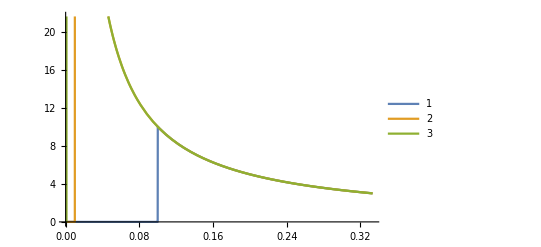

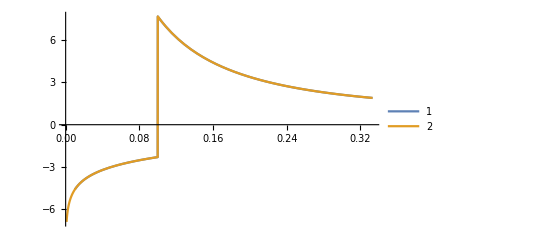

```mathematica
PlusDistribution[HeavisideTheta[tau]/tau]
%//replSingVarPlus
exp=FullSimplify[%,Assumptions->tau>0]/.tau->t

Plot[{exp/.beta->0.1,exp/.beta->0.01,exp/.beta->0.001},{t,0,1/3},PlotLegends->Automatic]
Plot[{(exp/.beta->0.1)-(Log@exp/.beta->0.01),(exp/.beta->0.1)-(Log@exp/.beta->0.001)},{t,0,1/3},PlotLegends->Automatic]
```

```mathematica
PlusDistribution[HeavisideTheta[u-v]/(u-v)+HeavisideTheta[v-u]/(v-u)]
%//replSymmPlus
exp2=%

Plot3D[{(*exp2/.beta->0.1,exp2/.beta->0.01,*)exp2/.beta->0.001},{u,0,1},{v,0,1},PlotLegends->Automatic]
```

((u-v)/(u-v)+(v-u)/(v-u))_+

-log(v/(v-u)) u-v+β+log((v-u)/(v-1)) u-v-β+(u-v-β)/(u-v)+(-u+v-β)/(v-u)

-log(v/(v-u)) u-v+β+log((v-u)/(v-1)) u-v-β+(u-v-β)/(u-v)+(-u+v-β)/(v-u)

Power::infy: Infinite expression TraditionalForm`1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

-Graphics3D-

```mathematica
Integrate[Gamma[0,x],{x,0,Infinity}]
```

1

```mathematica
Exp[1]Gamma[0,u-v]
exp3=%

Plot3D[{Gamma[u-v]HeavisideTheta[u-v],Gamma[v-u]HeavisideTheta[v-u]},{u,0,1},{v,0,1},PlotLegends->Automatic]
Plot3D[{psi[u-v]HeavisideTheta[u-v],psi[v-u]HeavisideTheta[v-u]},{u,0,1},{v,0,1},PlotLegends->Automatic]
```

ⅇ 0u-v

ⅇ 0u-v

-Graphics3D-

-Graphics3D-

```mathematica
exp2/.DiracDelta[u-v-beta]*a_:>DiracDelta[u-v](a/.u->v+beta)/.DiracDelta[u-v+beta]*a_:>DiracDelta[u-v](a/.u->v-beta)
Integrate[%u,{u,v-y,v+y},Assumptions->0<beta<y<1/5]
```

-u-v log(v/β)+u-v log(-β/(v-1))+(u-v-β)/(u-v)+(-u+v-β)/(v-u)

v (log(1/(1-v))-log(v)+2 log(y))

```mathematica
psi[u]HeavisideTheta[u-v]+psi[u]HeavisideTheta[1-v-u]
myint=Integrate[%,{u,v-y,v+y},Assumptions->0<beta<y<1/5]
```

(ⅇ^-u+0u) -u-v+1+(ⅇ^-u+0u) u-v

$Aborted

```mathematica
Series[myint,{v,0,0}]
Series[%,{y,0,1}]//Normal
FullSimplify[%,Assumptions->y>0]//Simplify
```

(y (--y)+y log(v)+ℽ y-y-2 ⅇ^-y+2)+O(v^1)

-ⅈ π y Floor[-(arg(y))/(2 π)]+ⅈ π y Floor[(arg(y))/(2 π)]+y (log(v)-log(y)+1)

y (log(v)-log(y)+1)

```mathematica
exp2/.DiracDelta[u-v-beta]*a_:>DiracDelta[u-v](a/.u->v+beta)/.DiracDelta[u-v+beta]*a_:>DiracDelta[u-v](a/.u->v-beta)
Integrate[%u,{u,0,1},Assumptions->0<beta<v<1-beta]
```

-u-v log(v/β)+u-v log(-β/(v-1))+(u-v-β)/(u-v)+(-u+v-β)/(v-u)

1-2 v

```mathematica
Gamma[0,u-v]HeavisideTheta[u-v]-Gamma[0,v-u]HeavisideTheta[v-u]
myint=Integrate[%u,{u,0,1},Assumptions->0<v<1]
```

u-v 0u-v-v-u 0v-u

1/2 (v^2 -v+(v^2-1) v-1-ⅇ^(v-1) v+ⅇ^-v v-2 ⅇ^(v-1)-ⅇ^-v+2)

```mathematica
Series[%,{v,0,1}]
%//N
```

(--1/2+1/2-1/ⅇ)+(1-1/ⅇ) v+O(v^2)

0.241813+0.632121 (v+0.)+O((v+0.)^2)

#### Make sure we can integrate the anomalous dimensions

```mathematica
anomDim2a1One/.ubar->1-u/.vbar->1-v
Integrate[%,{u,0,1},{v,0,1}]
```

u u-v

1/2

```mathematica
anomDim2a1Two/.ubar->1-u/.vbar->1-v
Integrate[%,{u,0,1}]
Integrate[%,{v,0,1}]
```

u v

v/2

1/4

```mathematica
anomDim2a1BetaThree//Expand
%/.DiracDelta[u-v-beta]a_:>DiracDelta[u-v-beta](a/.u->v+beta)/.DiracDelta[v-u-beta]a_:>DiracDelta[v-u-beta](a/.v->u+beta)//Simplify;
stopAndReorganize=%/.ubar->1-u/.vbar->1-v

stopAndReorganize/.HeavisideTheta[u-v]->AA;
uMinusV=SeriesCoefficient[%,{AA,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[v-u]->BB;
vMinusU=SeriesCoefficient[%,{BB,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[u-v-beta]->Cc;
uMinusVbeta=SeriesCoefficient[%,{Cc,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[v-u-beta]->DD;
vMinusUbeta=SeriesCoefficient[%,{DD,0,1}]//Simplify

stopAndReorganize/.DiracDelta[u-v-beta]->EE;
deltaTermsuvb=SeriesCoefficient[%,{EE,0,1}]//Simplify

stopAndReorganize/.DiracDelta[v-u-beta]->FF;
deltaTermsvub=SeriesCoefficient[%,{FF,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[u-v]->0/.HeavisideTheta[v-u]->0/.HeavisideTheta[u-v-beta]->0/.HeavisideTheta[v-u-beta]->0/.DiracDelta[u-v-beta]->0/.DiracDelta[v-u-beta]->0
%+HeavisideTheta[u-v]*uMinusV+HeavisideTheta[v-u]vMinusU+HeavisideTheta[u-v-beta]*uMinusVbeta+HeavisideTheta[v-u-beta]vMinusUbeta+DiracDelta[u-v-beta]*deltaTermsuvb+DiracDelta[v-u-beta]deltaTermsvub

integrateTermByTermNoPrint[%,{u,0,1}]
igrandV=FullSimplify[%,Assumptions->1>v>beta>0]


igrandV
Collect2[%,Log[v]]
Integrate[%,{v,0,1},Assumptions->0<beta<1]
```

0

0

0

«12 more identical outputs»

#### Put the anomalous dimension into 5x5 piles

```mathematica
one5x5=ConstantArray[0,{5,5}]

For[i=1,i≤5,i++,
For[j=1,j≤5,j++,
tmp=anomDim2a1One/.ubar->1-u/.vbar->1-v;

one5x5[[i,j]]=5Integrate[tmp,{u,(i-1)/5,i/5},{v,(j-1)/5,j/5}];
Print[(i-1)/5," < u < ",i/5,"     ",(j-1)/5,"  < v < ",j/5," :   ",one5x5[[i,j]]];
];
];

one5x5//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

0 < u < 1/5     0  < v < 1/5 :   1/50

0 < u < 1/5     1/5  < v < 2/5 :   0

0 < u < 1/5     2/5  < v < 3/5 :   0

0 < u < 1/5     3/5  < v < 4/5 :   0

0 < u < 1/5     4/5  < v < 1 :   0

1/5 < u < 2/5     0  < v < 1/5 :   0

1/5 < u < 2/5     1/5  < v < 2/5 :   3/50

1/5 < u < 2/5     2/5  < v < 3/5 :   0

1/5 < u < 2/5     3/5  < v < 4/5 :   0

1/5 < u < 2/5     4/5  < v < 1 :   0

2/5 < u < 3/5     0  < v < 1/5 :   0

2/5 < u < 3/5     1/5  < v < 2/5 :   0

2/5 < u < 3/5     2/5  < v < 3/5 :   1/10

2/5 < u < 3/5     3/5  < v < 4/5 :   0

2/5 < u < 3/5     4/5  < v < 1 :   0

3/5 < u < 4/5     0  < v < 1/5 :   0

3/5 < u < 4/5     1/5  < v < 2/5 :   0

3/5 < u < 4/5     2/5  < v < 3/5 :   0

3/5 < u < 4/5     3/5  < v < 4/5 :   7/50

3/5 < u < 4/5     4/5  < v < 1 :   0

4/5 < u < 1     0  < v < 1/5 :   0

4/5 < u < 1     1/5  < v < 2/5 :   0

4/5 < u < 1     2/5  < v < 3/5 :   0

4/5 < u < 1     3/5  < v < 4/5 :   0

4/5 < u < 1     4/5  < v < 1 :   9/50

(1/50 | 0 | 0 | 0 | 0
0 | 3/50 | 0 | 0 | 0
0 | 0 | 1/10 | 0 | 0
0 | 0 | 0 | 7/50 | 0
0 | 0 | 0 | 0 | 9/50)

```mathematica
(*two5x5Num=ConstantArray[0,{5,5}]*)
two5x5=ConstantArray[0,{5,5}]

tmp=anomDim2a1Two

For[i=1,i≤5,i++,
For[j=1,j≤5,j++,


tmp2=Integrate[tmp,{u,(i-1)/5,i/5}];
two5x5[[i,j]]=5Integrate[tmp2,{v,(j-1)/5,j/5}];

(*two5x5Num[[i,j]]=NIntegrate[tmp,{u,(i-1)/5,i/5},{v,(j-1)/5,j/5},WorkingPrecision->8];*)

];
];

two5x5//MatrixForm
(*two5x5Num//MatrixForm*)
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

u v

(1/2500 | 3/2500 | 1/500 | 7/2500 | 9/2500
3/2500 | 9/2500 | 3/500 | 21/2500 | 27/2500
1/500 | 3/500 | 1/100 | 7/500 | 9/500
7/2500 | 21/2500 | 7/500 | 49/2500 | 63/2500
9/2500 | 27/2500 | 9/500 | 63/2500 | 81/2500)

```mathematica
two5x5Exact={{0,0,0,0,(372-125 π^2-840 Log[5/4]+750 Log[5/4] Log[5]+750 PolyLog[2,4/5])/1500},{0,0,0,1/500 (122-445 Log[2]-500 Log[2]^2+195 Log[3]+250 Log[2] Log[3]+500 Log[2] Log[5]-250 Log[3] Log[5]+250 PolyLog[2,3/5]-250 PolyLog[2,4/5]),∫_(4/5)^1 (Piecewise[{{(v^2 (24-50 v+25 v^2) HeavisideTheta[4/5-v]-(-1+v) (-39+71 v-25 v^2+25 v^3-50 (-1+v) Log[-5/2 (-1+v)])+HeavisideTheta[-4/5+v] (56-130 v+99 v^2-50 v^3+25 v^4+100 v Log[2]-50 v^2 Log[2]-10 Log[3125]-50 Log[1-v]-50 (-2+v) v Log[-5/2 (-1+v)]))/(50 (2 v-2 v^2)), 3/5<v<1}, {0, True}}])ⅆv},{0,0,1/50 (12-12 Log[9/4]+25 ArcCoth[4] Log[9/4]+25 PolyLog[2,2/5]-25 PolyLog[2,3/5]),1/100 (-1+100 Log[2]^2-50 Log[8/3] Log[3]+5 Log[16/3]),1/100 (-1-100 ArcCoth[5] Log[5/4]+5 Log[1125/256])},{0,1/500 (118-445 Log[2]-500 Log[2]^2+195 Log[3]+250 Log[2] Log[5]+250 PolyLog[2,1/5]-250 PolyLog[2,2/5]),1/500 (-7+500 Log[2]^2-250 Log[8/3] Log[3]+5 Log[3456]),1/500 (-7+230 Log[2]-1000 Log[2]^2-115 Log[3]+1000 Log[2] Log[3]-250 Log[3]^2),∫_(4/5)^1 (Piecewise[{{(v^2 (16-50 v+25 v^2) HeavisideTheta[2/5-v]-(-1+v) (-11+59 v-25 v^2+25 v^3-50 (-1+v) Log[-5/4 (-1+v)])+HeavisideTheta[-2/5+v] (24-90 v+91 v^2-50 v^3+25 v^4+50 Log[3]-100 v Log[3]+50 v^2 Log[3]+100 v Log[4]-50 v^2 Log[4]-10 Log[3125]-50 Log[1-v]-50 (-2+v) v Log[-5/4 (-1+v)]))/(50 (2 v-2 v^2)), 1/5<v<1}, {0, True}}])ⅆv},{1/50 (58/5-56 ArcCoth[9]-25 PolyLog[2,1/5]),1/500 (-9+5 Log[2] (-9+100 Log[2]-50 Log[5])+50 Log[5]),1/500 (-9-50 Log[4]+5 Log[3/2] (11+100 Log[2]-50 Log[5])+50 Log[5]),1/500 (-9-50 Log[4]+5 Log[4/3] (11+100 Log[2]-50 Log[5])+50 Log[5]),1/500 (-9+100 ArcCoth[9]+5 Log[5/4] (11+100 Log[2]-50 Log[5]))}}
two5x5Exact[[4,2]]
%//N
```

(0 | 0 | 0 | 0 | (372-125 π^2-840 log(5/4)+750 log(5/4) log(5)+750 24/5)/1500
0 | 0 | 0 | 1/500 (122-445 log(2)-500 log^2(2)+195 log(3)+250 log(2) log(3)+500 log(2) log(5)-250 log(3) log(5)+250 23/5-250 24/5) | ∫_(4/5)^1 (Piecewise[{{((25 v^2-50 v+24) 4/5-v v^2-(v-1) (25 v^3-25 v^2+71 v-50 (v-1) log(-5/2 (v-1))-39)+v-4/5 (25 v^4-50 v^3-50 log(2) v^2+99 v^2-50 (v-2) log(-5/2 (v-1)) v+100 log(2) v-130 v-50 log(1-v)-10 log(3125)+56))/(50 (2 v-2 v^2)), 3/5<v<1}, {0, True}}])ⅆv
0 | 0 | 1/50 (12-12 log(9/4)+25 coth^-1(4) log(9/4)+25 22/5-25 23/5) | 1/100 (-1+100 log^2(2)-50 log(8/3) log(3)+5 log(16/3)) | 1/100 (-1-100 coth^-1(5) log(5/4)+5 log(1125/256))
0 | 1/500 (118-445 log(2)-500 log^2(2)+195 log(3)+250 log(2) log(5)+250 21/5-250 22/5) | 1/500 (-7+500 log^2(2)-250 log(8/3) log(3)+5 log(3456)) | 1/500 (-7+230 log(2)-1000 log^2(2)-115 log(3)+1000 log(2) log(3)-250 log^2(3)) | ∫_(4/5)^1 (Piecewise[{{((25 v^2-50 v+16) 2/5-v v^2-(v-1) (25 v^3-25 v^2+59 v-50 (v-1) log(-5/4 (v-1))-11)+v-2/5 (25 v^4-50 v^3-50 log(4) v^2+50 log(3) v^2+91 v^2-50 (v-2) log(-5/4 (v-1)) v+100 log(4) v-100 log(3) v-90 v-50 log(1-v)-10 log(3125)+50 log(3)+24))/(50 (2 v-2 v^2)), 1/5<v<1}, {0, True}}])ⅆv
1/50 (58/5-56 coth^-1(9)-25 21/5) | 1/500 (-9+5 log(2) (-9+100 log(2)-50 log(5))+50 log(5)) | 1/500 (-9-50 log(4)+5 log(3/2) (11+100 log(2)-50 log(5))+50 log(5)) | 1/500 (-9-50 log(4)+5 log(4/3) (11+100 log(2)-50 log(5))+50 log(5)) | 1/500 (-9+100 coth^-1(9)+5 log(5/4) (11+100 log(2)-50 log(5))))

1/500 (250 21/5-250 22/5+118-500 log^2(2)-445 log(2)+195 log(3)+250 log(2) log(5))

0.00575386

```mathematica
anomDim2a1BetaThree//Expand
%/.DiracDelta[u-v-beta]a_:>DiracDelta[u-v-beta](a/.u->v+beta)/.DiracDelta[v-u-beta]a_:>DiracDelta[v-u-beta](a/.v->u+beta)//Simplify;
stopAndReorganize=%/.ubar->1-u/.vbar->1-v

stopAndReorganize/.HeavisideTheta[u-v]->AA;
uMinusV=SeriesCoefficient[%,{AA,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[v-u]->BB;
vMinusU=SeriesCoefficient[%,{BB,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[u-v-beta]->Cc;
uMinusVbeta=SeriesCoefficient[%,{Cc,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[v-u-beta]->DD;
vMinusUbeta=SeriesCoefficient[%,{DD,0,1}]//Simplify

stopAndReorganize/.DiracDelta[u-v-beta]->EE;
deltaTermsuvb=SeriesCoefficient[%,{EE,0,1}]//Simplify

stopAndReorganize/.DiracDelta[v-u-beta]->FF;
deltaTermsvub=SeriesCoefficient[%,{FF,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[u-v]->0/.HeavisideTheta[v-u]->0/.HeavisideTheta[u-v-beta]->0/.HeavisideTheta[v-u-beta]->0/.DiracDelta[u-v-beta]->0/.DiracDelta[v-u-beta]->0
endStopAndReorganize=%+HeavisideTheta[u-v]*uMinusV+HeavisideTheta[v-u]vMinusU+HeavisideTheta[u-v-beta]*uMinusVbeta+HeavisideTheta[v-u-beta]vMinusUbeta+DiracDelta[u-v-beta]*deltaTermsuvb+DiracDelta[v-u-beta]deltaTermsvub;

three5x5=ConstantArray[0,{5,5}]

For[i=1,i≤5,i++,
For[j=1,j≤5,j++,

tmp=integrateTermByTermNoPrint[endStopAndReorganize,{u,(i-1)/5,i/5}];
tmp2igrandV=FullSimplify[tmp,Assumptions->1>v>beta>0];
tmp3=Collect2[%,Log[v]];
three5x5[[i,j]]=5Integrate[tmp3,{v,(j-1)/5,j/5},Assumptions->0<beta<1];

];
];
```

0

0

0

«6 more identical outputs»

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
one5x5
two5x5
one5x5+two5x5
{vals,vecs}=Eigensystem[%//N]
eVals=Reverse[vals];
eVecs=Reverse[vecs];
```

(1/50 | 0 | 0 | 0 | 0
0 | 3/50 | 0 | 0 | 0
0 | 0 | 1/10 | 0 | 0
0 | 0 | 0 | 7/50 | 0
0 | 0 | 0 | 0 | 9/50)

(1/2500 | 3/2500 | 1/500 | 7/2500 | 9/2500
3/2500 | 9/2500 | 3/500 | 21/2500 | 27/2500
1/500 | 3/500 | 1/100 | 7/500 | 9/500
7/2500 | 21/2500 | 7/500 | 49/2500 | 63/2500
9/2500 | 27/2500 | 9/500 | 63/2500 | 81/2500)

(51/2500 | 3/2500 | 1/500 | 7/2500 | 9/2500
3/2500 | 159/2500 | 3/500 | 21/2500 | 27/2500
1/500 | 3/500 | 11/100 | 7/500 | 9/500
7/2500 | 21/2500 | 7/500 | 399/2500 | 63/2500
9/2500 | 27/2500 | 9/500 | 63/2500 | 531/2500)

(0.227954 | 0.150542 | 0.105228 | 0.0620227 | 0.0202528
{0.0230756,0.085714,0.187515,0.381912,0.900612} | {-0.0103748,-0.0448745,-0.133982,-0.899284,0.413782} | {-0.0118878,-0.0672042,-0.968952,0.203965,0.121952} | {-0.01593,-0.992854,0.0881346,0.0600939,0.0510675} | {-0.999482,0.0190684,0.01584,0.0147684,0.0142334})

```mathematica
eVecs
```

(-0.999482 | 0.0190684 | 0.01584 | 0.0147684 | 0.0142334
-0.01593 | -0.992854 | 0.0881346 | 0.0600939 | 0.0510675
-0.0118878 | -0.0672042 | -0.968952 | 0.203965 | 0.121952
-0.0103748 | -0.0448745 | -0.133982 | -0.899284 | 0.413782
0.0230756 | 0.085714 | 0.187515 | 0.381912 | 0.900612)

#### Put the anomalous dimension into NxN piles

```mathematica
nN=25
oneNxN=ConstantArray[0,{nN,nN}]

For[i=1,i≤nN,i++,
For[j=1,j≤nN,j++,
tmp=anomDim2a1One/.ubar->1-u/.vbar->1-v;
oneNxN[[i,j]]=nN*Integrate[tmp,{u,(i-1)/nN,i/nN},{v,(j-1)/nN,j/nN}];
];
];

oneNxN//MatrixForm
```

25

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(1/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 7/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 9/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 11/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 13/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 31/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 33/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 37/50 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 39/50 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 41/50 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 43/50 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9/10 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 47/50 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 49/50)

```mathematica
(*two5x5Num=ConstantArray[0,{5,5}]*)
twoNxN=ConstantArray[0,{nN,nN}]

tmp=anomDim2a1Two

For[i=1,i≤nN,i++,
For[j=1,j≤nN,j++,
tmp2=Integrate[tmp,{u,(i-1)/nN,i/nN}];
twoNxN[[i,j]]=nN*Integrate[tmp2,{v,(j-1)/nN,j/nN}];
(*two5x5Num[[i,j]]=NIntegrate[tmp,{u,(i-1)/5,i/5},{v,(j-1)/5,j/5},WorkingPrecision->8];*)
];
];

twoNxN//MatrixForm
(*two5x5Num//MatrixForm*)
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

1/16 u v (-12 u+16 v-3)

(-217/75000000 | -523/75000000 | -637/75000000 | -559/75000000 | -289/75000000 | 173/75000000 | 827/75000000 | 1673/75000000 | 2711/75000000 | 3941/75000000 | 5363/75000000 | 6977/75000000 | 8783/75000000 | 10781/75000000 | 12971/75000000 | 15353/75000000 | 17927/75000000 | 20693/75000000 | 23651/75000000 | 26801/75000000 | 30143/75000000 | 33677/75000000 | 37403/75000000 | 41321/75000000 | 45431/75000000
-249/25000000 | -619/25000000 | -797/25000000 | -783/25000000 | -577/25000000 | -179/25000000 | 411/25000000 | 1193/25000000 | 2167/25000000 | 3333/25000000 | 4691/25000000 | 6241/25000000 | 7983/25000000 | 9917/25000000 | 12043/25000000 | 14361/25000000 | 16871/25000000 | 19573/25000000 | 22467/25000000 | 25553/25000000 | 28831/25000000 | 32301/25000000 | 35963/25000000 | 39817/25000000 | 43863/25000000
-1421/75000000 | -3623/75000000 | -973/15000000 | -5147/75000000 | -4469/75000000 | -2831/75000000 | -233/75000000 | 133/3000000 | 7843/75000000 | 13321/75000000 | 19759/75000000 | 27157/75000000 | 7103/15000000 | 44833/75000000 | 55111/75000000 | 66349/75000000 | 78547/75000000 | 18341/15000000 | 105823/75000000 | 120901/75000000 | 136939/75000000 | 153937/75000000 | 34379/15000000 | 190813/75000000 | 210691/75000000
-2239/75000000 | -5821/75000000 | -8059/75000000 | -8953/75000000 | -8503/75000000 | -6709/75000000 | -3571/75000000 | 911/75000000 | 6737/75000000 | 13907/75000000 | 22421/75000000 | 32279/75000000 | 43481/75000000 | 56027/75000000 | 69917/75000000 | 85151/75000000 | 101729/75000000 | 119651/75000000 | 138917/75000000 | 159527/75000000 | 181481/75000000 | 204779/75000000 | 229421/75000000 | 255407/75000000 | 282737/75000000
-1067/25000000 | -2817/25000000 | -3991/25000000 | -4589/25000000 | -4611/25000000 | -4057/25000000 | -2927/25000000 | -1221/25000000 | 1061/25000000 | 3919/25000000 | 7353/25000000 | 11363/25000000 | 15949/25000000 | 21111/25000000 | 26849/25000000 | 33163/25000000 | 40053/25000000 | 47519/25000000 | 55561/25000000 | 64179/25000000 | 73373/25000000 | 83143/25000000 | 93489/25000000 | 104411/25000000 | 115909/25000000
-4307/75000000 | -11513/75000000 | -16607/75000000 | -19589/75000000 | -20459/75000000 | -19217/75000000 | -15863/75000000 | -10397/75000000 | -2819/75000000 | 6871/75000000 | 18673/75000000 | 32587/75000000 | 48613/75000000 | 66751/75000000 | 87001/75000000 | 109363/75000000 | 133837/75000000 | 160423/75000000 | 189121/75000000 | 219931/75000000 | 252853/75000000 | 287887/75000000 | 325033/75000000 | 364291/75000000 | 405661/75000000
-5557/75000000 | -15007/75000000 | -21961/75000000 | -26419/75000000 | -28381/75000000 | -27847/75000000 | -24817/75000000 | -19291/75000000 | -11269/75000000 | -751/75000000 | 12263/75000000 | 27773/75000000 | 45779/75000000 | 66281/75000000 | 89279/75000000 | 114773/75000000 | 142763/75000000 | 173249/75000000 | 206231/75000000 | 241709/75000000 | 279683/75000000 | 320153/75000000 | 363119/75000000 | 408581/75000000 | 456539/75000000
-2317/25000000 | -6311/25000000 | -1869/5000000 | -11419/25000000 | -12533/25000000 | -12687/25000000 | -11881/25000000 | -2023/5000000 | -7389/25000000 | -3703/25000000 | 943/25000000 | 6549/25000000 | 2623/5000000 | 20641/25000000 | 29127/25000000 | 38573/25000000 | 48979/25000000 | 12069/5000000 | 72671/25000000 | 85957/25000000 | 100203/25000000 | 115409/25000000 | 5263/1000000 | 148701/25000000 | 166787/25000000
-8489/75000000 | -23291/75000000 | -34829/75000000 | -43103/75000000 | -48113/75000000 | -49859/75000000 | -48341/75000000 | -43559/75000000 | -35513/75000000 | -24203/75000000 | -9629/75000000 | 8209/75000000 | 29311/75000000 | 53677/75000000 | 81307/75000000 | 112201/75000000 | 146359/75000000 | 183781/75000000 | 224467/75000000 | 268417/75000000 | 315631/75000000 | 366109/75000000 | 419851/75000000 | 476857/75000000 | 537127/75000000
-10171/75000000 | -28081/75000000 | -42343/75000000 | -52957/75000000 | -59923/75000000 | -63241/75000000 | -62911/75000000 | -58933/75000000 | -51307/75000000 | -40033/75000000 | -25111/75000000 | -6541/75000000 | 15677/75000000 | 41543/75000000 | 71057/75000000 | 104219/75000000 | 141029/75000000 | 181487/75000000 | 225593/75000000 | 273347/75000000 | 324749/75000000 | 379799/75000000 | 438497/75000000 | 500843/75000000 | 566837/75000000
-3999/25000000 | -11101/25000000 | -16859/25000000 | -21273/25000000 | -24343/25000000 | -26069/25000000 | -26451/25000000 | -25489/25000000 | -23183/25000000 | -19533/25000000 | -14539/25000000 | -8201/25000000 | -519/25000000 | 8507/25000000 | 18877/25000000 | 30591/25000000 | 43649/25000000 | 58051/25000000 | 73797/25000000 | 90887/25000000 | 109321/25000000 | 129099/25000000 | 150221/25000000 | 172687/25000000 | 196497/25000000
-13967/75000000 | -38957/75000000 | -59531/75000000 | -75689/75000000 | -87431/75000000 | -94757/75000000 | -97667/75000000 | -96161/75000000 | -90239/75000000 | -79901/75000000 | -65147/75000000 | -45977/75000000 | -22391/75000000 | 5611/75000000 | 38029/75000000 | 74863/75000000 | 116113/75000000 | 161779/75000000 | 211861/75000000 | 266359/75000000 | 325273/75000000 | 388603/75000000 | 456349/75000000 | 528511/75000000 | 605089/75000000
-16081/75000000 | -45043/75000000 | -13841/15000000 | -88567/75000000 | -103129/75000000 | -112891/75000000 | -117853/75000000 | -23603/15000000 | -113377/75000000 | -103939/75000000 | -89701/75000000 | -70663/75000000 | -1873/3000000 | -18187/75000000 | 15251/75000000 | 53489/75000000 | 96527/75000000 | 28873/15000000 | 197003/75000000 | 254441/75000000 | 316679/75000000 | 383717/75000000 | 91111/15000000 | 532193/75000000 | 613631/75000000
-6113/25000000 | -17187/25000000 | -26533/25000000 | -34151/25000000 | -40041/25000000 | -44203/25000000 | -46637/25000000 | -47343/25000000 | -46321/25000000 | -43571/25000000 | -39093/25000000 | -32887/25000000 | -24953/25000000 | -15291/25000000 | -3901/25000000 | 9217/25000000 | 24063/25000000 | 40637/25000000 | 58939/25000000 | 78969/25000000 | 100727/25000000 | 124213/25000000 | 149427/25000000 | 176369/25000000 | 205039/25000000
-20741/75000000 | -58511/75000000 | -90713/75000000 | -117347/75000000 | -138413/75000000 | -153911/75000000 | -163841/75000000 | -168203/75000000 | -166997/75000000 | -160223/75000000 | -147881/75000000 | -129971/75000000 | -106493/75000000 | -77447/75000000 | -42833/75000000 | -2651/75000000 | 43099/75000000 | 94417/75000000 | 151303/75000000 | 213757/75000000 | 281779/75000000 | 355369/75000000 | 434527/75000000 | 519253/75000000 | 609547/75000000
-23287/75000000 | -65893/75000000 | -102547/75000000 | -133249/75000000 | -157999/75000000 | -176797/75000000 | -189643/75000000 | -196537/75000000 | -197479/75000000 | -192469/75000000 | -181507/75000000 | -164593/75000000 | -141727/75000000 | -112909/75000000 | -78139/75000000 | -37417/75000000 | 9257/75000000 | 61883/75000000 | 120461/75000000 | 184991/75000000 | 255473/75000000 | 331907/75000000 | 414293/75000000 | 502631/75000000 | 596921/75000000
-8659/25000000 | -24569/25000000 | -38367/25000000 | -50053/25000000 | -59627/25000000 | -67089/25000000 | -72439/25000000 | -75677/25000000 | -76803/25000000 | -75817/25000000 | -72719/25000000 | -67509/25000000 | -60187/25000000 | -50753/25000000 | -39207/25000000 | -25549/25000000 | -9779/25000000 | 8103/25000000 | 28097/25000000 | 50203/25000000 | 74421/25000000 | 100751/25000000 | 129193/25000000 | 159747/25000000 | 192413/25000000
-28811/75000000 | -81953/75000000 | -1027/600000 | -168077/75000000 | -201059/75000000 | -227321/75000000 | -246863/75000000 | -51937/15000000 | -265787/75000000 | -265169/75000000 | -257831/75000000 | -243773/75000000 | -44599/15000000 | -195497/75000000 | -161279/75000000 | -120341/75000000 | -72683/75000000 | -3661/15000000 | 42793/75000000 | 110611/75000000 | 185149/75000000 | 266407/75000000 | 70877/15000000 | 449083/75000000 | 550501/75000000
-31789/75000000 | -90631/75000000 | -142369/75000000 | -187003/75000000 | -224533/75000000 | -254959/75000000 | -278281/75000000 | -294499/75000000 | -303613/75000000 | -305623/75000000 | -300529/75000000 | -288331/75000000 | -269029/75000000 | -242623/75000000 | -209113/75000000 | -168499/75000000 | -120781/75000000 | -65959/75000000 | -4033/75000000 | 64997/75000000 | 141131/75000000 | 224369/75000000 | 314711/75000000 | 412157/75000000 | 516707/75000000
-11637/25000000 | -33247/25000000 | -52361/25000000 | -68979/25000000 | -83101/25000000 | -94727/25000000 | -103857/25000000 | -110491/25000000 | -114629/25000000 | -116271/25000000 | -115417/25000000 | -112067/25000000 | -106221/25000000 | -97879/25000000 | -87041/25000000 | -73707/25000000 | -57877/25000000 | -39551/25000000 | -18729/25000000 | 4589/25000000 | 30403/25000000 | 58713/25000000 | 89519/25000000 | 122821/25000000 | 158619/25000000
-38177/75000000 | -109283/75000000 | -172517/75000000 | -227879/75000000 | -275369/75000000 | -314987/75000000 | -346733/75000000 | -370607/75000000 | -386609/75000000 | -394739/75000000 | -394997/75000000 | -387383/75000000 | -371897/75000000 | -348539/75000000 | -317309/75000000 | -278207/75000000 | -231233/75000000 | -176387/75000000 | -113669/75000000 | -43079/75000000 | 35383/75000000 | 121717/75000000 | 215923/75000000 | 318001/75000000 | 427951/75000000
-41587/75000000 | -119257/75000000 | -188671/75000000 | -249829/75000000 | -302731/75000000 | -347377/75000000 | -383767/75000000 | -411901/75000000 | -431779/75000000 | -443401/75000000 | -446767/75000000 | -441877/75000000 | -428731/75000000 | -407329/75000000 | -377671/75000000 | -339757/75000000 | -293587/75000000 | -239161/75000000 | -176479/75000000 | -105541/75000000 | -26347/75000000 | 61103/75000000 | 156809/75000000 | 260771/75000000 | 372989/75000000
-15047/25000000 | -43221/25000000 | -13703/5000000 | -90929/25000000 | -110463/25000000 | -127117/25000000 | -140891/25000000 | -30357/5000000 | -159799/25000000 | -164933/25000000 | -167187/25000000 | -166561/25000000 | -32611/5000000 | -156669/25000000 | -147403/25000000 | -135257/25000000 | -120231/25000000 | -4093/1000000 | -81539/25000000 | -57873/25000000 | -31327/25000000 | -1901/25000000 | 6081/5000000 | 65591/25000000 | 103657/25000000
-48839/75000000 | -140501/75000000 | -223139/75000000 | -296753/75000000 | -361343/75000000 | -416909/75000000 | -463451/75000000 | -500969/75000000 | -529463/75000000 | -548933/75000000 | -559379/75000000 | -560801/75000000 | -553199/75000000 | -536573/75000000 | -510923/75000000 | -476249/75000000 | -432551/75000000 | -379829/75000000 | -318083/75000000 | -247313/75000000 | -167519/75000000 | -78701/75000000 | 19141/75000000 | 126007/75000000 | 241897/75000000
-52681/75000000 | -151771/75000000 | -241453/75000000 | -321727/75000000 | -392593/75000000 | -454051/75000000 | -506101/75000000 | -548743/75000000 | -581977/75000000 | -605803/75000000 | -620221/75000000 | -625231/75000000 | -620833/75000000 | -607027/75000000 | -583813/75000000 | -551191/75000000 | -509161/75000000 | -457723/75000000 | -396877/75000000 | -326623/75000000 | -246961/75000000 | -157891/75000000 | -59413/75000000 | 48473/75000000 | 165767/75000000)

```mathematica
anomDim2a1BetaThree//Expand
%/.DiracDelta[u-v-beta]a_:>DiracDelta[u-v-beta](a/.u->v+beta)/.DiracDelta[v-u-beta]a_:>DiracDelta[v-u-beta](a/.v->u+beta)//Simplify;
stopAndReorganize=%/.ubar->1-u/.vbar->1-v

stopAndReorganize/.HeavisideTheta[u-v]->AA;
uMinusV=SeriesCoefficient[%,{AA,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[v-u]->BB;
vMinusU=SeriesCoefficient[%,{BB,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[u-v-beta]->Cc;
uMinusVbeta=SeriesCoefficient[%,{Cc,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[v-u-beta]->DD;
vMinusUbeta=SeriesCoefficient[%,{DD,0,1}]//Simplify

stopAndReorganize/.DiracDelta[u-v-beta]->EE;
deltaTermsuvb=SeriesCoefficient[%,{EE,0,1}]//Simplify

stopAndReorganize/.DiracDelta[v-u-beta]->FF;
deltaTermsvub=SeriesCoefficient[%,{FF,0,1}]//Simplify

stopAndReorganize/.HeavisideTheta[u-v]->0/.HeavisideTheta[v-u]->0/.HeavisideTheta[u-v-beta]->0/.HeavisideTheta[v-u-beta]->0/.DiracDelta[u-v-beta]->0/.DiracDelta[v-u-beta]->0
endStopAndReorganize=%+HeavisideTheta[u-v]*uMinusV+HeavisideTheta[v-u]vMinusU+HeavisideTheta[u-v-beta]*uMinusVbeta+HeavisideTheta[v-u-beta]vMinusUbeta+DiracDelta[u-v-beta]*deltaTermsuvb+DiracDelta[v-u-beta]deltaTermsvub;

threeNxN=ConstantArray[0,{nN,nN}]

(*For[i=1,i≤nN,i++,
For[j=1,j≤nN,j++,

tmp=integrateTermByTermNoPrint[endStopAndReorganize,{u,(i-1)/nN,i/nN}];
tmp2igrandV=FullSimplify[tmp,Assumptions->1>v>beta>0];
tmp3=Collect2[%,Log[v]];
threeNxN[[i,j]]=nN*Integrate[tmp3,{v,(j-1)/nN,j/nN},Assumptions->0<beta<1];

];
];*)
```

0

0

0

«6 more identical outputs»

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
oneNxN
twoNxN
oneNxN+twoNxN
{vvalsN,vvecsN}=Eigensystem[%//N]
valsN=Reverse[vvalsN]
vecsN=Reverse[vvecsN]
```

(1/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 7/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 9/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 11/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 13/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 31/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 33/50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 37/50 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 39/50 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 41/50 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 43/50 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9/10 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 47/50 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 49/50)

(-217/75000000 | -523/75000000 | -637/75000000 | -559/75000000 | -289/75000000 | 173/75000000 | 827/75000000 | 1673/75000000 | 2711/75000000 | 3941/75000000 | 5363/75000000 | 6977/75000000 | 8783/75000000 | 10781/75000000 | 12971/75000000 | 15353/75000000 | 17927/75000000 | 20693/75000000 | 23651/75000000 | 26801/75000000 | 30143/75000000 | 33677/75000000 | 37403/75000000 | 41321/75000000 | 45431/75000000
-249/25000000 | -619/25000000 | -797/25000000 | -783/25000000 | -577/25000000 | -179/25000000 | 411/25000000 | 1193/25000000 | 2167/25000000 | 3333/25000000 | 4691/25000000 | 6241/25000000 | 7983/25000000 | 9917/25000000 | 12043/25000000 | 14361/25000000 | 16871/25000000 | 19573/25000000 | 22467/25000000 | 25553/25000000 | 28831/25000000 | 32301/25000000 | 35963/25000000 | 39817/25000000 | 43863/25000000
-1421/75000000 | -3623/75000000 | -973/15000000 | -5147/75000000 | -4469/75000000 | -2831/75000000 | -233/75000000 | 133/3000000 | 7843/75000000 | 13321/75000000 | 19759/75000000 | 27157/75000000 | 7103/15000000 | 44833/75000000 | 55111/75000000 | 66349/75000000 | 78547/75000000 | 18341/15000000 | 105823/75000000 | 120901/75000000 | 136939/75000000 | 153937/75000000 | 34379/15000000 | 190813/75000000 | 210691/75000000
-2239/75000000 | -5821/75000000 | -8059/75000000 | -8953/75000000 | -8503/75000000 | -6709/75000000 | -3571/75000000 | 911/75000000 | 6737/75000000 | 13907/75000000 | 22421/75000000 | 32279/75000000 | 43481/75000000 | 56027/75000000 | 69917/75000000 | 85151/75000000 | 101729/75000000 | 119651/75000000 | 138917/75000000 | 159527/75000000 | 181481/75000000 | 204779/75000000 | 229421/75000000 | 255407/75000000 | 282737/75000000
-1067/25000000 | -2817/25000000 | -3991/25000000 | -4589/25000000 | -4611/25000000 | -4057/25000000 | -2927/25000000 | -1221/25000000 | 1061/25000000 | 3919/25000000 | 7353/25000000 | 11363/25000000 | 15949/25000000 | 21111/25000000 | 26849/25000000 | 33163/25000000 | 40053/25000000 | 47519/25000000 | 55561/25000000 | 64179/25000000 | 73373/25000000 | 83143/25000000 | 93489/25000000 | 104411/25000000 | 115909/25000000
-4307/75000000 | -11513/75000000 | -16607/75000000 | -19589/75000000 | -20459/75000000 | -19217/75000000 | -15863/75000000 | -10397/75000000 | -2819/75000000 | 6871/75000000 | 18673/75000000 | 32587/75000000 | 48613/75000000 | 66751/75000000 | 87001/75000000 | 109363/75000000 | 133837/75000000 | 160423/75000000 | 189121/75000000 | 219931/75000000 | 252853/75000000 | 287887/75000000 | 325033/75000000 | 364291/75000000 | 405661/75000000
-5557/75000000 | -15007/75000000 | -21961/75000000 | -26419/75000000 | -28381/75000000 | -27847/75000000 | -24817/75000000 | -19291/75000000 | -11269/75000000 | -751/75000000 | 12263/75000000 | 27773/75000000 | 45779/75000000 | 66281/75000000 | 89279/75000000 | 114773/75000000 | 142763/75000000 | 173249/75000000 | 206231/75000000 | 241709/75000000 | 279683/75000000 | 320153/75000000 | 363119/75000000 | 408581/75000000 | 456539/75000000
-2317/25000000 | -6311/25000000 | -1869/5000000 | -11419/25000000 | -12533/25000000 | -12687/25000000 | -11881/25000000 | -2023/5000000 | -7389/25000000 | -3703/25000000 | 943/25000000 | 6549/25000000 | 2623/5000000 | 20641/25000000 | 29127/25000000 | 38573/25000000 | 48979/25000000 | 12069/5000000 | 72671/25000000 | 85957/25000000 | 100203/25000000 | 115409/25000000 | 5263/1000000 | 148701/25000000 | 166787/25000000
-8489/75000000 | -23291/75000000 | -34829/75000000 | -43103/75000000 | -48113/75000000 | -49859/75000000 | -48341/75000000 | -43559/75000000 | -35513/75000000 | -24203/75000000 | -9629/75000000 | 8209/75000000 | 29311/75000000 | 53677/75000000 | 81307/75000000 | 112201/75000000 | 146359/75000000 | 183781/75000000 | 224467/75000000 | 268417/75000000 | 315631/75000000 | 366109/75000000 | 419851/75000000 | 476857/75000000 | 537127/75000000
-10171/75000000 | -28081/75000000 | -42343/75000000 | -52957/75000000 | -59923/75000000 | -63241/75000000 | -62911/75000000 | -58933/75000000 | -51307/75000000 | -40033/75000000 | -25111/75000000 | -6541/75000000 | 15677/75000000 | 41543/75000000 | 71057/75000000 | 104219/75000000 | 141029/75000000 | 181487/75000000 | 225593/75000000 | 273347/75000000 | 324749/75000000 | 379799/75000000 | 438497/75000000 | 500843/75000000 | 566837/75000000
-3999/25000000 | -11101/25000000 | -16859/25000000 | -21273/25000000 | -24343/25000000 | -26069/25000000 | -26451/25000000 | -25489/25000000 | -23183/25000000 | -19533/25000000 | -14539/25000000 | -8201/25000000 | -519/25000000 | 8507/25000000 | 18877/25000000 | 30591/25000000 | 43649/25000000 | 58051/25000000 | 73797/25000000 | 90887/25000000 | 109321/25000000 | 129099/25000000 | 150221/25000000 | 172687/25000000 | 196497/25000000
-13967/75000000 | -38957/75000000 | -59531/75000000 | -75689/75000000 | -87431/75000000 | -94757/75000000 | -97667/75000000 | -96161/75000000 | -90239/75000000 | -79901/75000000 | -65147/75000000 | -45977/75000000 | -22391/75000000 | 5611/75000000 | 38029/75000000 | 74863/75000000 | 116113/75000000 | 161779/75000000 | 211861/75000000 | 266359/75000000 | 325273/75000000 | 388603/75000000 | 456349/75000000 | 528511/75000000 | 605089/75000000
-16081/75000000 | -45043/75000000 | -13841/15000000 | -88567/75000000 | -103129/75000000 | -112891/75000000 | -117853/75000000 | -23603/15000000 | -113377/75000000 | -103939/75000000 | -89701/75000000 | -70663/75000000 | -1873/3000000 | -18187/75000000 | 15251/75000000 | 53489/75000000 | 96527/75000000 | 28873/15000000 | 197003/75000000 | 254441/75000000 | 316679/75000000 | 383717/75000000 | 91111/15000000 | 532193/75000000 | 613631/75000000
-6113/25000000 | -17187/25000000 | -26533/25000000 | -34151/25000000 | -40041/25000000 | -44203/25000000 | -46637/25000000 | -47343/25000000 | -46321/25000000 | -43571/25000000 | -39093/25000000 | -32887/25000000 | -24953/25000000 | -15291/25000000 | -3901/25000000 | 9217/25000000 | 24063/25000000 | 40637/25000000 | 58939/25000000 | 78969/25000000 | 100727/25000000 | 124213/25000000 | 149427/25000000 | 176369/25000000 | 205039/25000000
-20741/75000000 | -58511/75000000 | -90713/75000000 | -117347/75000000 | -138413/75000000 | -153911/75000000 | -163841/75000000 | -168203/75000000 | -166997/75000000 | -160223/75000000 | -147881/75000000 | -129971/75000000 | -106493/75000000 | -77447/75000000 | -42833/75000000 | -2651/75000000 | 43099/75000000 | 94417/75000000 | 151303/75000000 | 213757/75000000 | 281779/75000000 | 355369/75000000 | 434527/75000000 | 519253/75000000 | 609547/75000000
-23287/75000000 | -65893/75000000 | -102547/75000000 | -133249/75000000 | -157999/75000000 | -176797/75000000 | -189643/75000000 | -196537/75000000 | -197479/75000000 | -192469/75000000 | -181507/75000000 | -164593/75000000 | -141727/75000000 | -112909/75000000 | -78139/75000000 | -37417/75000000 | 9257/75000000 | 61883/75000000 | 120461/75000000 | 184991/75000000 | 255473/75000000 | 331907/75000000 | 414293/75000000 | 502631/75000000 | 596921/75000000
-8659/25000000 | -24569/25000000 | -38367/25000000 | -50053/25000000 | -59627/25000000 | -67089/25000000 | -72439/25000000 | -75677/25000000 | -76803/25000000 | -75817/25000000 | -72719/25000000 | -67509/25000000 | -60187/25000000 | -50753/25000000 | -39207/25000000 | -25549/25000000 | -9779/25000000 | 8103/25000000 | 28097/25000000 | 50203/25000000 | 74421/25000000 | 100751/25000000 | 129193/25000000 | 159747/25000000 | 192413/25000000
-28811/75000000 | -81953/75000000 | -1027/600000 | -168077/75000000 | -201059/75000000 | -227321/75000000 | -246863/75000000 | -51937/15000000 | -265787/75000000 | -265169/75000000 | -257831/75000000 | -243773/75000000 | -44599/15000000 | -195497/75000000 | -161279/75000000 | -120341/75000000 | -72683/75000000 | -3661/15000000 | 42793/75000000 | 110611/75000000 | 185149/75000000 | 266407/75000000 | 70877/15000000 | 449083/75000000 | 550501/75000000
-31789/75000000 | -90631/75000000 | -142369/75000000 | -187003/75000000 | -224533/75000000 | -254959/75000000 | -278281/75000000 | -294499/75000000 | -303613/75000000 | -305623/75000000 | -300529/75000000 | -288331/75000000 | -269029/75000000 | -242623/75000000 | -209113/75000000 | -168499/75000000 | -120781/75000000 | -65959/75000000 | -4033/75000000 | 64997/75000000 | 141131/75000000 | 224369/75000000 | 314711/75000000 | 412157/75000000 | 516707/75000000
-11637/25000000 | -33247/25000000 | -52361/25000000 | -68979/25000000 | -83101/25000000 | -94727/25000000 | -103857/25000000 | -110491/25000000 | -114629/25000000 | -116271/25000000 | -115417/25000000 | -112067/25000000 | -106221/25000000 | -97879/25000000 | -87041/25000000 | -73707/25000000 | -57877/25000000 | -39551/25000000 | -18729/25000000 | 4589/25000000 | 30403/25000000 | 58713/25000000 | 89519/25000000 | 122821/25000000 | 158619/25000000
-38177/75000000 | -109283/75000000 | -172517/75000000 | -227879/75000000 | -275369/75000000 | -314987/75000000 | -346733/75000000 | -370607/75000000 | -386609/75000000 | -394739/75000000 | -394997/75000000 | -387383/75000000 | -371897/75000000 | -348539/75000000 | -317309/75000000 | -278207/75000000 | -231233/75000000 | -176387/75000000 | -113669/75000000 | -43079/75000000 | 35383/75000000 | 121717/75000000 | 215923/75000000 | 318001/75000000 | 427951/75000000
-41587/75000000 | -119257/75000000 | -188671/75000000 | -249829/75000000 | -302731/75000000 | -347377/75000000 | -383767/75000000 | -411901/75000000 | -431779/75000000 | -443401/75000000 | -446767/75000000 | -441877/75000000 | -428731/75000000 | -407329/75000000 | -377671/75000000 | -339757/75000000 | -293587/75000000 | -239161/75000000 | -176479/75000000 | -105541/75000000 | -26347/75000000 | 61103/75000000 | 156809/75000000 | 260771/75000000 | 372989/75000000
-15047/25000000 | -43221/25000000 | -13703/5000000 | -90929/25000000 | -110463/25000000 | -127117/25000000 | -140891/25000000 | -30357/5000000 | -159799/25000000 | -164933/25000000 | -167187/25000000 | -166561/25000000 | -32611/5000000 | -156669/25000000 | -147403/25000000 | -135257/25000000 | -120231/25000000 | -4093/1000000 | -81539/25000000 | -57873/25000000 | -31327/25000000 | -1901/25000000 | 6081/5000000 | 65591/25000000 | 103657/25000000
-48839/75000000 | -140501/75000000 | -223139/75000000 | -296753/75000000 | -361343/75000000 | -416909/75000000 | -463451/75000000 | -500969/75000000 | -529463/75000000 | -548933/75000000 | -559379/75000000 | -560801/75000000 | -553199/75000000 | -536573/75000000 | -510923/75000000 | -476249/75000000 | -432551/75000000 | -379829/75000000 | -318083/75000000 | -247313/75000000 | -167519/75000000 | -78701/75000000 | 19141/75000000 | 126007/75000000 | 241897/75000000
-52681/75000000 | -151771/75000000 | -241453/75000000 | -321727/75000000 | -392593/75000000 | -454051/75000000 | -506101/75000000 | -548743/75000000 | -581977/75000000 | -605803/75000000 | -620221/75000000 | -625231/75000000 | -620833/75000000 | -607027/75000000 | -583813/75000000 | -551191/75000000 | -509161/75000000 | -457723/75000000 | -396877/75000000 | -326623/75000000 | -246961/75000000 | -157891/75000000 | -59413/75000000 | 48473/75000000 | 165767/75000000)

(1499783/75000000 | -523/75000000 | -637/75000000 | -559/75000000 | -289/75000000 | 173/75000000 | 827/75000000 | 1673/75000000 | 2711/75000000 | 3941/75000000 | 5363/75000000 | 6977/75000000 | 8783/75000000 | 10781/75000000 | 12971/75000000 | 15353/75000000 | 17927/75000000 | 20693/75000000 | 23651/75000000 | 26801/75000000 | 30143/75000000 | 33677/75000000 | 37403/75000000 | 41321/75000000 | 45431/75000000
-249/25000000 | 1499381/25000000 | -797/25000000 | -783/25000000 | -577/25000000 | -179/25000000 | 411/25000000 | 1193/25000000 | 2167/25000000 | 3333/25000000 | 4691/25000000 | 6241/25000000 | 7983/25000000 | 9917/25000000 | 12043/25000000 | 14361/25000000 | 16871/25000000 | 19573/25000000 | 22467/25000000 | 25553/25000000 | 28831/25000000 | 32301/25000000 | 35963/25000000 | 39817/25000000 | 43863/25000000
-1421/75000000 | -3623/75000000 | 1499027/15000000 | -5147/75000000 | -4469/75000000 | -2831/75000000 | -233/75000000 | 133/3000000 | 7843/75000000 | 13321/75000000 | 19759/75000000 | 27157/75000000 | 7103/15000000 | 44833/75000000 | 55111/75000000 | 66349/75000000 | 78547/75000000 | 18341/15000000 | 105823/75000000 | 120901/75000000 | 136939/75000000 | 153937/75000000 | 34379/15000000 | 190813/75000000 | 210691/75000000
-2239/75000000 | -5821/75000000 | -8059/75000000 | 10491047/75000000 | -8503/75000000 | -6709/75000000 | -3571/75000000 | 911/75000000 | 6737/75000000 | 13907/75000000 | 22421/75000000 | 32279/75000000 | 43481/75000000 | 56027/75000000 | 69917/75000000 | 85151/75000000 | 101729/75000000 | 119651/75000000 | 138917/75000000 | 159527/75000000 | 181481/75000000 | 204779/75000000 | 229421/75000000 | 255407/75000000 | 282737/75000000
-1067/25000000 | -2817/25000000 | -3991/25000000 | -4589/25000000 | 4495389/25000000 | -4057/25000000 | -2927/25000000 | -1221/25000000 | 1061/25000000 | 3919/25000000 | 7353/25000000 | 11363/25000000 | 15949/25000000 | 21111/25000000 | 26849/25000000 | 33163/25000000 | 40053/25000000 | 47519/25000000 | 55561/25000000 | 64179/25000000 | 73373/25000000 | 83143/25000000 | 93489/25000000 | 104411/25000000 | 115909/25000000
-4307/75000000 | -11513/75000000 | -16607/75000000 | -19589/75000000 | -20459/75000000 | 16480783/75000000 | -15863/75000000 | -10397/75000000 | -2819/75000000 | 6871/75000000 | 18673/75000000 | 32587/75000000 | 48613/75000000 | 66751/75000000 | 87001/75000000 | 109363/75000000 | 133837/75000000 | 160423/75000000 | 189121/75000000 | 219931/75000000 | 252853/75000000 | 287887/75000000 | 325033/75000000 | 364291/75000000 | 405661/75000000
-5557/75000000 | -15007/75000000 | -21961/75000000 | -26419/75000000 | -28381/75000000 | -27847/75000000 | 19475183/75000000 | -19291/75000000 | -11269/75000000 | -751/75000000 | 12263/75000000 | 27773/75000000 | 45779/75000000 | 66281/75000000 | 89279/75000000 | 114773/75000000 | 142763/75000000 | 173249/75000000 | 206231/75000000 | 241709/75000000 | 279683/75000000 | 320153/75000000 | 363119/75000000 | 408581/75000000 | 456539/75000000
-2317/25000000 | -6311/25000000 | -1869/5000000 | -11419/25000000 | -12533/25000000 | -12687/25000000 | -11881/25000000 | 1497977/5000000 | -7389/25000000 | -3703/25000000 | 943/25000000 | 6549/25000000 | 2623/5000000 | 20641/25000000 | 29127/25000000 | 38573/25000000 | 48979/25000000 | 12069/5000000 | 72671/25000000 | 85957/25000000 | 100203/25000000 | 115409/25000000 | 5263/1000000 | 148701/25000000 | 166787/25000000
-8489/75000000 | -23291/75000000 | -34829/75000000 | -43103/75000000 | -48113/75000000 | -49859/75000000 | -48341/75000000 | -43559/75000000 | 25464487/75000000 | -24203/75000000 | -9629/75000000 | 8209/75000000 | 29311/75000000 | 53677/75000000 | 81307/75000000 | 112201/75000000 | 146359/75000000 | 183781/75000000 | 224467/75000000 | 268417/75000000 | 315631/75000000 | 366109/75000000 | 419851/75000000 | 476857/75000000 | 537127/75000000
-10171/75000000 | -28081/75000000 | -42343/75000000 | -52957/75000000 | -59923/75000000 | -63241/75000000 | -62911/75000000 | -58933/75000000 | -51307/75000000 | 28459967/75000000 | -25111/75000000 | -6541/75000000 | 15677/75000000 | 41543/75000000 | 71057/75000000 | 104219/75000000 | 141029/75000000 | 181487/75000000 | 225593/75000000 | 273347/75000000 | 324749/75000000 | 379799/75000000 | 438497/75000000 | 500843/75000000 | 566837/75000000
-3999/25000000 | -11101/25000000 | -16859/25000000 | -21273/25000000 | -24343/25000000 | -26069/25000000 | -26451/25000000 | -25489/25000000 | -23183/25000000 | -19533/25000000 | 10485461/25000000 | -8201/25000000 | -519/25000000 | 8507/25000000 | 18877/25000000 | 30591/25000000 | 43649/25000000 | 58051/25000000 | 73797/25000000 | 90887/25000000 | 109321/25000000 | 129099/25000000 | 150221/25000000 | 172687/25000000 | 196497/25000000
-13967/75000000 | -38957/75000000 | -59531/75000000 | -75689/75000000 | -87431/75000000 | -94757/75000000 | -97667/75000000 | -96161/75000000 | -90239/75000000 | -79901/75000000 | -65147/75000000 | 34454023/75000000 | -22391/75000000 | 5611/75000000 | 38029/75000000 | 74863/75000000 | 116113/75000000 | 161779/75000000 | 211861/75000000 | 266359/75000000 | 325273/75000000 | 388603/75000000 | 456349/75000000 | 528511/75000000 | 605089/75000000
-16081/75000000 | -45043/75000000 | -13841/15000000 | -88567/75000000 | -103129/75000000 | -112891/75000000 | -117853/75000000 | -23603/15000000 | -113377/75000000 | -103939/75000000 | -89701/75000000 | -70663/75000000 | 1498127/3000000 | -18187/75000000 | 15251/75000000 | 53489/75000000 | 96527/75000000 | 28873/15000000 | 197003/75000000 | 254441/75000000 | 316679/75000000 | 383717/75000000 | 91111/15000000 | 532193/75000000 | 613631/75000000
-6113/25000000 | -17187/25000000 | -26533/25000000 | -34151/25000000 | -40041/25000000 | -44203/25000000 | -46637/25000000 | -47343/25000000 | -46321/25000000 | -43571/25000000 | -39093/25000000 | -32887/25000000 | -24953/25000000 | 13484709/25000000 | -3901/25000000 | 9217/25000000 | 24063/25000000 | 40637/25000000 | 58939/25000000 | 78969/25000000 | 100727/25000000 | 124213/25000000 | 149427/25000000 | 176369/25000000 | 205039/25000000
-20741/75000000 | -58511/75000000 | -90713/75000000 | -117347/75000000 | -138413/75000000 | -153911/75000000 | -163841/75000000 | -168203/75000000 | -166997/75000000 | -160223/75000000 | -147881/75000000 | -129971/75000000 | -106493/75000000 | -77447/75000000 | 43457167/75000000 | -2651/75000000 | 43099/75000000 | 94417/75000000 | 151303/75000000 | 213757/75000000 | 281779/75000000 | 355369/75000000 | 434527/75000000 | 519253/75000000 | 609547/75000000
-23287/75000000 | -65893/75000000 | -102547/75000000 | -133249/75000000 | -157999/75000000 | -176797/75000000 | -189643/75000000 | -196537/75000000 | -197479/75000000 | -192469/75000000 | -181507/75000000 | -164593/75000000 | -141727/75000000 | -112909/75000000 | -78139/75000000 | 46462583/75000000 | 9257/75000000 | 61883/75000000 | 120461/75000000 | 184991/75000000 | 255473/75000000 | 331907/75000000 | 414293/75000000 | 502631/75000000 | 596921/75000000
-8659/25000000 | -24569/25000000 | -38367/25000000 | -50053/25000000 | -59627/25000000 | -67089/25000000 | -72439/25000000 | -75677/25000000 | -76803/25000000 | -75817/25000000 | -72719/25000000 | -67509/25000000 | -60187/25000000 | -50753/25000000 | -39207/25000000 | -25549/25000000 | 16490221/25000000 | 8103/25000000 | 28097/25000000 | 50203/25000000 | 74421/25000000 | 100751/25000000 | 129193/25000000 | 159747/25000000 | 192413/25000000
-28811/75000000 | -81953/75000000 | -1027/600000 | -168077/75000000 | -201059/75000000 | -227321/75000000 | -246863/75000000 | -51937/15000000 | -265787/75000000 | -265169/75000000 | -257831/75000000 | -243773/75000000 | -44599/15000000 | -195497/75000000 | -161279/75000000 | -120341/75000000 | -72683/75000000 | 10496339/15000000 | 42793/75000000 | 110611/75000000 | 185149/75000000 | 266407/75000000 | 70877/15000000 | 449083/75000000 | 550501/75000000
-31789/75000000 | -90631/75000000 | -142369/75000000 | -187003/75000000 | -224533/75000000 | -254959/75000000 | -278281/75000000 | -294499/75000000 | -303613/75000000 | -305623/75000000 | -300529/75000000 | -288331/75000000 | -269029/75000000 | -242623/75000000 | -209113/75000000 | -168499/75000000 | -120781/75000000 | -65959/75000000 | 55495967/75000000 | 64997/75000000 | 141131/75000000 | 224369/75000000 | 314711/75000000 | 412157/75000000 | 516707/75000000
-11637/25000000 | -33247/25000000 | -52361/25000000 | -68979/25000000 | -83101/25000000 | -94727/25000000 | -103857/25000000 | -110491/25000000 | -114629/25000000 | -116271/25000000 | -115417/25000000 | -112067/25000000 | -106221/25000000 | -97879/25000000 | -87041/25000000 | -73707/25000000 | -57877/25000000 | -39551/25000000 | -18729/25000000 | 19504589/25000000 | 30403/25000000 | 58713/25000000 | 89519/25000000 | 122821/25000000 | 158619/25000000
-38177/75000000 | -109283/75000000 | -172517/75000000 | -227879/75000000 | -275369/75000000 | -314987/75000000 | -346733/75000000 | -370607/75000000 | -386609/75000000 | -394739/75000000 | -394997/75000000 | -387383/75000000 | -371897/75000000 | -348539/75000000 | -317309/75000000 | -278207/75000000 | -231233/75000000 | -176387/75000000 | -113669/75000000 | -43079/75000000 | 61535383/75000000 | 121717/75000000 | 215923/75000000 | 318001/75000000 | 427951/75000000
-41587/75000000 | -119257/75000000 | -188671/75000000 | -249829/75000000 | -302731/75000000 | -347377/75000000 | -383767/75000000 | -411901/75000000 | -431779/75000000 | -443401/75000000 | -446767/75000000 | -441877/75000000 | -428731/75000000 | -407329/75000000 | -377671/75000000 | -339757/75000000 | -293587/75000000 | -239161/75000000 | -176479/75000000 | -105541/75000000 | -26347/75000000 | 64561103/75000000 | 156809/75000000 | 260771/75000000 | 372989/75000000
-15047/25000000 | -43221/25000000 | -13703/5000000 | -90929/25000000 | -110463/25000000 | -127117/25000000 | -140891/25000000 | -30357/5000000 | -159799/25000000 | -164933/25000000 | -167187/25000000 | -166561/25000000 | -32611/5000000 | -156669/25000000 | -147403/25000000 | -135257/25000000 | -120231/25000000 | -4093/1000000 | -81539/25000000 | -57873/25000000 | -31327/25000000 | -1901/25000000 | 4506081/5000000 | 65591/25000000 | 103657/25000000
-48839/75000000 | -140501/75000000 | -223139/75000000 | -296753/75000000 | -361343/75000000 | -416909/75000000 | -463451/75000000 | -500969/75000000 | -529463/75000000 | -548933/75000000 | -559379/75000000 | -560801/75000000 | -553199/75000000 | -536573/75000000 | -510923/75000000 | -476249/75000000 | -432551/75000000 | -379829/75000000 | -318083/75000000 | -247313/75000000 | -167519/75000000 | -78701/75000000 | 19141/75000000 | 70626007/75000000 | 241897/75000000
-52681/75000000 | -151771/75000000 | -241453/75000000 | -321727/75000000 | -392593/75000000 | -454051/75000000 | -506101/75000000 | -548743/75000000 | -581977/75000000 | -605803/75000000 | -620221/75000000 | -625231/75000000 | -620833/75000000 | -607027/75000000 | -583813/75000000 | -551191/75000000 | -509161/75000000 | -457723/75000000 | -396877/75000000 | -326623/75000000 | -246961/75000000 | -157891/75000000 | -59413/75000000 | 48473/75000000 | 73665767/75000000)

(0.980001 | 0.94 | 0.9 | 0.86 | 0.82 | 0.78 | 0.74 | 0.699999 | 0.659999 | 0.619999 | 0.579999 | 0.539999 | 0.499999 | 0.459999 | 0.419999 | 0.379999 | 0.339999 | 0.3 | 0.26 | 0.22 | 0.18 | 0.14 | 0.0999999 | 0.0599999 | 0.02
{-0.000745848,-0.00224776,-0.00374968,-0.0052516,-0.00675352,-0.00825544,-0.00975737,-0.0112593,-0.0127612,-0.0142632,-0.0157651,-0.0172671,-0.0187691,-0.0202711,-0.0217731,-0.0232751,-0.0247772,-0.0262793,-0.0277815,-0.0292838,-0.0307863,-0.0322893,-0.0337934,-0.0353017,-0.994793} | {0.00071754,0.00216287,0.0036082,0.00505354,0.00649887,0.00794421,0.00938955,0.0108349,0.0122802,0.0137256,0.0151709,0.0166163,0.0180617,0.0195071,0.0209525,0.0223979,0.0238433,0.0252888,0.0267344,0.0281801,0.029626,0.0310725,0.0325215,0.995129,0.0353975} | {-0.000688966,-0.00207718,-0.0034654,-0.00485361,-0.00624183,-0.00763005,-0.00901827,-0.0104065,-0.0117947,-0.0131829,-0.0145712,-0.0159594,-0.0173476,-0.0187358,-0.0201241,-0.0215123,-0.0229006,-0.0242889,-0.0256772,-0.0270656,-0.0284542,-0.0298436,-0.995463,-0.0326154,-0.0340047} | {-0.000660128,-0.0019907,-0.00332127,-0.00465184,-0.00598241,-0.00731297,-0.00864354,-0.0099741,-0.0113047,-0.0126352,-0.0139658,-0.0152963,-0.0166269,-0.0179574,-0.019288,-0.0206185,-0.021949,-0.0232795,-0.0246099,-0.0259402,-0.0272698,-0.995794,-0.0299348,-0.0312644,-0.0325947} | {0.000631032,0.00190344,0.00317585,0.00444825,0.00572065,0.00699305,0.00826545,0.00953784,0.0108102,0.0120826,0.013355,0.0146273,0.0158997,0.017172,0.0184443,0.0197165,0.0209887,0.0222606,0.0235321,0.0248017,0.99612,0.0273578,0.0286274,0.0298989,0.0311709} | {-0.000601685,-0.00181543,-0.00302917,-0.0042429,-0.00545664,-0.00667036,-0.00788408,-0.0090978,-0.0103115,-0.0115252,-0.0127389,-0.0139525,-0.0151661,-0.0163797,-0.0175932,-0.0188065,-0.0200195,-0.0212319,-0.0224413,-0.99644,-0.0248862,-0.0260956,-0.0273079,-0.028521,-0.0297343} | {0.000572096,0.00172669,0.00288128,0.00403586,0.00519043,0.006345,0.00749956,0.0086541,0.00980863,0.0109631,0.0121176,0.013272,0.0144264,0.0155806,0.0167347,0.0178884,0.0190412,0.0201902,0.996754,0.0225219,0.0236709,0.0248237,0.0259774,0.0271314,0.0282857} | {0.000542274,0.00163725,0.00273221,0.00382717,0.00492212,0.00601706,0.00711198,0.00820688,0.00930176,0.0103966,0.0114914,0.0125861,0.0136807,0.014775,0.0158689,0.0169618,0.0180502,0.997059,0.0202667,0.0213551,0.0224479,0.0235418,0.0246362,0.0257307,0.0268255} | {-0.000512228,-0.00154713,-0.00258203,-0.00361691,-0.00465179,-0.00568664,-0.00672147,-0.00775627,-0.00879104,-0.00982574,-0.0108604,-0.0118948,-0.0129291,-0.0139628,-0.0149953,-0.0160229,-0.997355,-0.0181223,-0.0191499,-0.0201824,-0.0212161,-0.0222504,-0.0232849,-0.0243195,-0.0253542} | {-0.000481968,-0.00145637,-0.00243077,-0.00340515,-0.00437951,-0.00535385,-0.00632816,-0.00730242,-0.00827662,-0.00925073,-0.0102247,-0.0111984,-0.0121715,-0.0131434,-0.01411,-0.99764,-0.0160905,-0.0170571,-0.0180289,-0.0190021,-0.0199758,-0.0209498,-0.0219239,-0.0228981,-0.0238723} | {0.000451504,0.001365,0.00227849,0.00319196,0.0041054,0.00501881,0.00593217,0.00684547,0.00775867,0.00867171,0.00958449,0.0104967,0.0114076,0.012313,0.997914,0.0141729,0.0150783,0.0159892,0.0169014,0.0178142,0.0187272,0.0196404,0.0205537,0.0214671,0.0223805} | {0.000420848,0.00127306,0.00212524,0.00297741,0.00382954,0.00468162,0.00553364,0.00638555,0.00723731,0.0080888,0.00893973,0.00978928,0.0106333,0.998174,0.0123711,0.0132151,0.0140647,0.0149156,0.0157671,0.0166188,0.0174708,0.0183228,0.0191749,0.020027,0.0208792} | {-0.000390011,-0.00118056,-0.00197108,-0.00276158,-0.00355202,-0.0043424,-0.00513268,-0.00592281,-0.00671266,-0.00750196,-0.00828989,-0.00907233,-0.998421,-0.0106866,-0.011469,-0.012257,-0.0130463,-0.0138361,-0.0146263,-0.0154165,-0.0162069,-0.0169974,-0.0177879,-0.0185784,-0.0193689} | {-0.000359004,-0.00108755,-0.00181607,-0.00254454,-0.00327295,-0.00400127,-0.00472943,-0.00545732,-0.00618468,-0.00691071,-0.0076314,-0.998653,-0.00912081,-0.0098415,-0.0105675,-0.0112949,-0.0120228,-0.0127509,-0.0134793,-0.0142077,-0.0149361,-0.0156647,-0.0163932,-0.0171218,-0.0178504} | {-0.000327839,-0.00099407,-0.00166026,-0.00232639,-0.00299243,-0.00365832,-0.00432395,-0.00498908,-0.00565294,-0.0063117,-0.998868,-0.00767505,-0.00833382,-0.00899767,-0.0096628,-0.0103284,-0.0109943,-0.0116604,-0.0123265,-0.0129927,-0.0136589,-0.0143252,-0.0149915,-0.0156578,-0.0163241} | {-0.000296529,-0.000900147,-0.00150371,-0.00210719,-0.00271053,-0.00331363,-0.00391626,-0.00451769,-0.00511436,-0.999067,-0.00635058,-0.00694725,-0.00754869,-0.00815132,-0.00875442,-0.00935776,-0.00996124,-0.0105648,-0.0111684,-0.0117721,-0.0123758,-0.0129795,-0.0135832,-0.0141869,-0.0147907} | {-0.000265085,-0.00080582,-0.00134648,-0.00188701,-0.00242732,-0.0029672,-0.00350599,-0.00404041,-0.999249,-0.00514855,-0.00568297,-0.00622175,-0.00676163,-0.00730195,-0.00784248,-0.00838314,-0.00892387,-0.00946466,-0.0100055,-0.0105463,-0.0110872,-0.0116281,-0.012169,-0.0127099,-0.0132508} | {-0.00023352,-0.000711124,-0.00118862,-0.00166591,-0.00214282,-0.00261874,-0.00309076,-0.999412,-0.00407001,-0.00454202,-0.00501795,-0.00549485,-0.00597215,-0.00644964,-0.00692724,-0.00740492,-0.00788264,-0.00836039,-0.00883817,-0.00931596,-0.00979377,-0.0102716,-0.0107494,-0.0112273,-0.0117051} | {0.000201846,0.000616091,0.00103016,0.0014439,0.00185678,0.00226624,0.999556,0.0031159,0.00352537,0.00393825,0.00435198,0.00476605,0.0051803,0.00559464,0.00600904,0.00642348,0.00683796,0.00725245,0.00766696,0.00808148,0.00849601,0.00891055,0.00932509,0.00973964,0.0101542} | {-0.000170075,-0.000520747,-0.00087113,-0.00122079,-0.00156757,-0.999681,-0.0022871,-0.00263387,-0.00298353,-0.00333392,-0.00368459,-0.0040354,-0.0043863,-0.00473725,-0.00508824,-0.00543925,-0.00579027,-0.00614131,-0.00649236,-0.00684342,-0.00719448,-0.00754555,-0.00789662,-0.0082477,-0.00859878} | {0.000138215,0.000425097,0.000711395,0.000995353,0.999786,0.00158432,0.00186828,0.00215458,0.00244146,0.00272858,0.00301581,0.00330311,0.00359045,0.00387782,0.00416521,0.00445261,0.00474003,0.00502745,0.00531488,0.00560231,0.00588975,0.00617719,0.00646464,0.00675208,0.00703953} | {0.000106269,0.000329077,0.000550099,0.99987,0.00100822,0.00122924,0.00145205,0.0016753,0.00189874,0.00212226,0.00234583,0.00256944,0.00279306,0.00301671,0.00324036,0.00346402,0.00368769,0.00391136,0.00413503,0.00435871,0.00458239,0.00480608,0.00502976,0.00525345,0.00547714} | {0.0000742173,0.00023219,0.999934,0.000559308,0.000717281,0.000876496,0.00103602,0.00119567,0.00135538,0.00151513,0.00167489,0.00183468,0.00199447,0.00215427,0.00231408,0.00247389,0.00263371,0.00279352,0.00295334,0.00311316,0.00327299,0.00343281,0.00359264,0.00375246,0.00391229} | {0.0000419042,0.999976,0.000238,0.000332823,0.000428362,0.00052408,0.00061987,0.000715696,0.000811542,0.000907401,0.00100327,0.00109914,0.00119502,0.0012909,0.00138679,0.00148267,0.00157856,0.00167445,0.00177034,0.00186623,0.00196212,0.00205801,0.0021539,0.00224979,0.00234569} | {-0.999997,-0.000044593,-0.0000761707,-0.000107975,-0.000139835,-0.000171719,-0.000203613,-0.000235514,-0.000267419,-0.000299327,-0.000331237,-0.000363148,-0.00039506,-0.000426972,-0.000458886,-0.0004908,-0.000522714,-0.000554629,-0.000586544,-0.000618459,-0.000650374,-0.00068229,-0.000714206,-0.000746121,-0.000778037})

{0.02,0.0599999,0.0999999,0.14,0.18,0.22,0.26,0.3,0.339999,0.379999,0.419999,0.459999,0.499999,0.539999,0.579999,0.619999,0.659999,0.699999,0.74,0.78,0.82,0.86,0.9,0.94,0.980001}

(-0.999997 | -0.000044593 | -0.0000761707 | -0.000107975 | -0.000139835 | -0.000171719 | -0.000203613 | -0.000235514 | -0.000267419 | -0.000299327 | -0.000331237 | -0.000363148 | -0.00039506 | -0.000426972 | -0.000458886 | -0.0004908 | -0.000522714 | -0.000554629 | -0.000586544 | -0.000618459 | -0.000650374 | -0.00068229 | -0.000714206 | -0.000746121 | -0.000778037
0.0000419042 | 0.999976 | 0.000238 | 0.000332823 | 0.000428362 | 0.00052408 | 0.00061987 | 0.000715696 | 0.000811542 | 0.000907401 | 0.00100327 | 0.00109914 | 0.00119502 | 0.0012909 | 0.00138679 | 0.00148267 | 0.00157856 | 0.00167445 | 0.00177034 | 0.00186623 | 0.00196212 | 0.00205801 | 0.0021539 | 0.00224979 | 0.00234569
0.0000742173 | 0.00023219 | 0.999934 | 0.000559308 | 0.000717281 | 0.000876496 | 0.00103602 | 0.00119567 | 0.00135538 | 0.00151513 | 0.00167489 | 0.00183468 | 0.00199447 | 0.00215427 | 0.00231408 | 0.00247389 | 0.00263371 | 0.00279352 | 0.00295334 | 0.00311316 | 0.00327299 | 0.00343281 | 0.00359264 | 0.00375246 | 0.00391229
0.000106269 | 0.000329077 | 0.000550099 | 0.99987 | 0.00100822 | 0.00122924 | 0.00145205 | 0.0016753 | 0.00189874 | 0.00212226 | 0.00234583 | 0.00256944 | 0.00279306 | 0.00301671 | 0.00324036 | 0.00346402 | 0.00368769 | 0.00391136 | 0.00413503 | 0.00435871 | 0.00458239 | 0.00480608 | 0.00502976 | 0.00525345 | 0.00547714
0.000138215 | 0.000425097 | 0.000711395 | 0.000995353 | 0.999786 | 0.00158432 | 0.00186828 | 0.00215458 | 0.00244146 | 0.00272858 | 0.00301581 | 0.00330311 | 0.00359045 | 0.00387782 | 0.00416521 | 0.00445261 | 0.00474003 | 0.00502745 | 0.00531488 | 0.00560231 | 0.00588975 | 0.00617719 | 0.00646464 | 0.00675208 | 0.00703953
-0.000170075 | -0.000520747 | -0.00087113 | -0.00122079 | -0.00156757 | -0.999681 | -0.0022871 | -0.00263387 | -0.00298353 | -0.00333392 | -0.00368459 | -0.0040354 | -0.0043863 | -0.00473725 | -0.00508824 | -0.00543925 | -0.00579027 | -0.00614131 | -0.00649236 | -0.00684342 | -0.00719448 | -0.00754555 | -0.00789662 | -0.0082477 | -0.00859878
0.000201846 | 0.000616091 | 0.00103016 | 0.0014439 | 0.00185678 | 0.00226624 | 0.999556 | 0.0031159 | 0.00352537 | 0.00393825 | 0.00435198 | 0.00476605 | 0.0051803 | 0.00559464 | 0.00600904 | 0.00642348 | 0.00683796 | 0.00725245 | 0.00766696 | 0.00808148 | 0.00849601 | 0.00891055 | 0.00932509 | 0.00973964 | 0.0101542
-0.00023352 | -0.000711124 | -0.00118862 | -0.00166591 | -0.00214282 | -0.00261874 | -0.00309076 | -0.999412 | -0.00407001 | -0.00454202 | -0.00501795 | -0.00549485 | -0.00597215 | -0.00644964 | -0.00692724 | -0.00740492 | -0.00788264 | -0.00836039 | -0.00883817 | -0.00931596 | -0.00979377 | -0.0102716 | -0.0107494 | -0.0112273 | -0.0117051
-0.000265085 | -0.00080582 | -0.00134648 | -0.00188701 | -0.00242732 | -0.0029672 | -0.00350599 | -0.00404041 | -0.999249 | -0.00514855 | -0.00568297 | -0.00622175 | -0.00676163 | -0.00730195 | -0.00784248 | -0.00838314 | -0.00892387 | -0.00946466 | -0.0100055 | -0.0105463 | -0.0110872 | -0.0116281 | -0.012169 | -0.0127099 | -0.0132508
-0.000296529 | -0.000900147 | -0.00150371 | -0.00210719 | -0.00271053 | -0.00331363 | -0.00391626 | -0.00451769 | -0.00511436 | -0.999067 | -0.00635058 | -0.00694725 | -0.00754869 | -0.00815132 | -0.00875442 | -0.00935776 | -0.00996124 | -0.0105648 | -0.0111684 | -0.0117721 | -0.0123758 | -0.0129795 | -0.0135832 | -0.0141869 | -0.0147907
-0.000327839 | -0.00099407 | -0.00166026 | -0.00232639 | -0.00299243 | -0.00365832 | -0.00432395 | -0.00498908 | -0.00565294 | -0.0063117 | -0.998868 | -0.00767505 | -0.00833382 | -0.00899767 | -0.0096628 | -0.0103284 | -0.0109943 | -0.0116604 | -0.0123265 | -0.0129927 | -0.0136589 | -0.0143252 | -0.0149915 | -0.0156578 | -0.0163241
-0.000359004 | -0.00108755 | -0.00181607 | -0.00254454 | -0.00327295 | -0.00400127 | -0.00472943 | -0.00545732 | -0.00618468 | -0.00691071 | -0.0076314 | -0.998653 | -0.00912081 | -0.0098415 | -0.0105675 | -0.0112949 | -0.0120228 | -0.0127509 | -0.0134793 | -0.0142077 | -0.0149361 | -0.0156647 | -0.0163932 | -0.0171218 | -0.0178504
-0.000390011 | -0.00118056 | -0.00197108 | -0.00276158 | -0.00355202 | -0.0043424 | -0.00513268 | -0.00592281 | -0.00671266 | -0.00750196 | -0.00828989 | -0.00907233 | -0.998421 | -0.0106866 | -0.011469 | -0.012257 | -0.0130463 | -0.0138361 | -0.0146263 | -0.0154165 | -0.0162069 | -0.0169974 | -0.0177879 | -0.0185784 | -0.0193689
0.000420848 | 0.00127306 | 0.00212524 | 0.00297741 | 0.00382954 | 0.00468162 | 0.00553364 | 0.00638555 | 0.00723731 | 0.0080888 | 0.00893973 | 0.00978928 | 0.0106333 | 0.998174 | 0.0123711 | 0.0132151 | 0.0140647 | 0.0149156 | 0.0157671 | 0.0166188 | 0.0174708 | 0.0183228 | 0.0191749 | 0.020027 | 0.0208792
0.000451504 | 0.001365 | 0.00227849 | 0.00319196 | 0.0041054 | 0.00501881 | 0.00593217 | 0.00684547 | 0.00775867 | 0.00867171 | 0.00958449 | 0.0104967 | 0.0114076 | 0.012313 | 0.997914 | 0.0141729 | 0.0150783 | 0.0159892 | 0.0169014 | 0.0178142 | 0.0187272 | 0.0196404 | 0.0205537 | 0.0214671 | 0.0223805
-0.000481968 | -0.00145637 | -0.00243077 | -0.00340515 | -0.00437951 | -0.00535385 | -0.00632816 | -0.00730242 | -0.00827662 | -0.00925073 | -0.0102247 | -0.0111984 | -0.0121715 | -0.0131434 | -0.01411 | -0.99764 | -0.0160905 | -0.0170571 | -0.0180289 | -0.0190021 | -0.0199758 | -0.0209498 | -0.0219239 | -0.0228981 | -0.0238723
-0.000512228 | -0.00154713 | -0.00258203 | -0.00361691 | -0.00465179 | -0.00568664 | -0.00672147 | -0.00775627 | -0.00879104 | -0.00982574 | -0.0108604 | -0.0118948 | -0.0129291 | -0.0139628 | -0.0149953 | -0.0160229 | -0.997355 | -0.0181223 | -0.0191499 | -0.0201824 | -0.0212161 | -0.0222504 | -0.0232849 | -0.0243195 | -0.0253542
0.000542274 | 0.00163725 | 0.00273221 | 0.00382717 | 0.00492212 | 0.00601706 | 0.00711198 | 0.00820688 | 0.00930176 | 0.0103966 | 0.0114914 | 0.0125861 | 0.0136807 | 0.014775 | 0.0158689 | 0.0169618 | 0.0180502 | 0.997059 | 0.0202667 | 0.0213551 | 0.0224479 | 0.0235418 | 0.0246362 | 0.0257307 | 0.0268255
0.000572096 | 0.00172669 | 0.00288128 | 0.00403586 | 0.00519043 | 0.006345 | 0.00749956 | 0.0086541 | 0.00980863 | 0.0109631 | 0.0121176 | 0.013272 | 0.0144264 | 0.0155806 | 0.0167347 | 0.0178884 | 0.0190412 | 0.0201902 | 0.996754 | 0.0225219 | 0.0236709 | 0.0248237 | 0.0259774 | 0.0271314 | 0.0282857
-0.000601685 | -0.00181543 | -0.00302917 | -0.0042429 | -0.00545664 | -0.00667036 | -0.00788408 | -0.0090978 | -0.0103115 | -0.0115252 | -0.0127389 | -0.0139525 | -0.0151661 | -0.0163797 | -0.0175932 | -0.0188065 | -0.0200195 | -0.0212319 | -0.0224413 | -0.99644 | -0.0248862 | -0.0260956 | -0.0273079 | -0.028521 | -0.0297343
0.000631032 | 0.00190344 | 0.00317585 | 0.00444825 | 0.00572065 | 0.00699305 | 0.00826545 | 0.00953784 | 0.0108102 | 0.0120826 | 0.013355 | 0.0146273 | 0.0158997 | 0.017172 | 0.0184443 | 0.0197165 | 0.0209887 | 0.0222606 | 0.0235321 | 0.0248017 | 0.99612 | 0.0273578 | 0.0286274 | 0.0298989 | 0.0311709
-0.000660128 | -0.0019907 | -0.00332127 | -0.00465184 | -0.00598241 | -0.00731297 | -0.00864354 | -0.0099741 | -0.0113047 | -0.0126352 | -0.0139658 | -0.0152963 | -0.0166269 | -0.0179574 | -0.019288 | -0.0206185 | -0.021949 | -0.0232795 | -0.0246099 | -0.0259402 | -0.0272698 | -0.995794 | -0.0299348 | -0.0312644 | -0.0325947
-0.000688966 | -0.00207718 | -0.0034654 | -0.00485361 | -0.00624183 | -0.00763005 | -0.00901827 | -0.0104065 | -0.0117947 | -0.0131829 | -0.0145712 | -0.0159594 | -0.0173476 | -0.0187358 | -0.0201241 | -0.0215123 | -0.0229006 | -0.0242889 | -0.0256772 | -0.0270656 | -0.0284542 | -0.0298436 | -0.995463 | -0.0326154 | -0.0340047
0.00071754 | 0.00216287 | 0.0036082 | 0.00505354 | 0.00649887 | 0.00794421 | 0.00938955 | 0.0108349 | 0.0122802 | 0.0137256 | 0.0151709 | 0.0166163 | 0.0180617 | 0.0195071 | 0.0209525 | 0.0223979 | 0.0238433 | 0.0252888 | 0.0267344 | 0.0281801 | 0.029626 | 0.0310725 | 0.0325215 | 0.995129 | 0.0353975
-0.000745848 | -0.00224776 | -0.00374968 | -0.0052516 | -0.00675352 | -0.00825544 | -0.00975737 | -0.0112593 | -0.0127612 | -0.0142632 | -0.0157651 | -0.0172671 | -0.0187691 | -0.0202711 | -0.0217731 | -0.0232751 | -0.0247772 | -0.0262793 | -0.0277815 | -0.0292838 | -0.0307863 | -0.0322893 | -0.0337934 | -0.0353017 | -0.994793)

```mathematica
vecsN[[All,3]]
Abs@%
```

{-0.0000761707,0.000238,0.999934,0.000550099,0.000711395,-0.00087113,0.00103016,-0.00118862,-0.00134648,-0.00150371,-0.00166026,-0.00181607,-0.00197108,0.00212524,0.00227849,-0.00243077,-0.00258203,0.00273221,0.00288128,-0.00302917,0.00317585,-0.00332127,-0.0034654,0.0036082,-0.00374968}

{0.0000761707,0.000238,0.999934,0.000550099,0.000711395,0.00087113,0.00103016,0.00118862,0.00134648,0.00150371,0.00166026,0.00181607,0.00197108,0.00212524,0.00227849,0.00243077,0.00258203,0.00273221,0.00288128,0.00302917,0.00317585,0.00332127,0.0034654,0.0036082,0.00374968}

```mathematica
Max[vecsN[[All,1]]]
Sign[%]
Ordering[ Abs@vecsN[[All,1]],-1]
Position[vecsN[[All,1]],Max[Abs@vecsN[[All,1]]]]
```

0.00071754

1

{1}

{}

```mathematica
(* it seems to work? last thing i need to do is either find an algorithm to calculate E and D and Einv, or to fit discretized eigenvectors as a functon of u and v *)

C2[v_,y_]:=1/v
rah=multiply[matEinv[uu,v],C2[v,yy]]
c2new[u_,v_]:=rah/.uu->u/.yy->v

matD[a,b]

multiply[matD[u,v],c2new[v,w]]
```

1/uu-(3 uu)/4

a a-b

1-(3 u^2)/4

```mathematica
(* fix the eigen vector signs *)
newVecsN=ConstantArray[0,{nN,nN}];

For[i=1,i≤nN,i++,
indMax=Ordering[ Abs@vecsN[[All,i]],-1];
newVecsN[[All,i]]=Sign[vecsN[[All,indMax[[1]]]]]*vecsN[[All,i]];
]
```

```mathematica
newVecsN[[All,3]].newVecsN[[All,3]]
```

0.999993

```mathematica
ListPlot3D[newVecsN]

Plot3D[HeavisideTheta[u-v+0.05]HeavisideTheta[0.05-(u-v)]+u*v,{u,0,1},{v,0,1}]
```

-Graphics3D-

-Graphics3D-

#### Testing Canonical Example

```mathematica
ClearAll[matD,matE,matEinv];
(* so from this we know that if E(u,v)=delta(u-v)+u*v then if D(u,v)=u*delta(u-v) the corresponding matrix gamma=E*D*E^-1 is *)
matD[u_,v_]:=DiracDelta[u-v]*u
matE[u_,v_]:=(DiracDelta[u-v]+u*v)
matEinv[u_,v_]:=(DiracDelta[u-v]-3*u*v/4)

(* first do D*E^-1 *)
gammaPerm=multiply[matE[uu,z],matD[z,w],matEinv[w,vv]]
gamma[u_,v_]:=gammaPerm/.uu->u/.vv->v
gammaTrans[u_,v_]:=gammaPerm/.uu->v/.vv->u

(* then presumably we have that the rows of E are eigenfunctions of gamma with eigenvalue u? *)
```

vv uu-vv+1/16 uu vv (-12 uu+16 vv-3)

```mathematica
multiply[gamma[u,w],eigenVecs[w,z]]
```

u (u-z+z^2)

```mathematica
aa=multiply[t1[u,v],gammaTrans[v,uu]]
bb=multiply[gamma[u,v],gammaTrans[v,u1]]/.u1->u
```

u^2 uu-u+(u uu (1280 u^2-420 u (4 uu+1)+1280 uu^2-420 uu+151))/1280

0 u^2+((2560 u^2-420 (4 u+1) u-420 u+151) u^2)/1280

```mathematica
bb/.u1->u
```

0 u^2+((2560 u^2-420 (4 u+1) u-420 u+151) u^2)/1280

```mathematica
t1[u_,v_]:=gamma[u,v]
t2[uu_,v_]:=gamma[uu,v]-aa*t1[uu,v]/bb
```

```mathematica
t2[uu,vv]/.vv->v
%//Simplify
```

-((u^2 uu-u+(u uu (1280 u^2-420 u (4 uu+1)+1280 uu^2-420 uu+151))/1280) (v uu-v+1/16 uu v (-12 uu+16 v-3)))/(0 u^2+((2560 u^2-420 (4 u+1) u-420 u+151) u^2)/1280)+v uu-v+1/16 uu v (-12 uu+16 v-3)

-((u^2 uu-u+(u uu (1280 u^2-420 u (4 uu+1)+1280 uu^2-420 uu+151))/1280) (v uu-v+1/16 uu v (-12 uu+16 v-3)))/(0 u^2+((880 u^2-840 u+151) u^2)/1280)+v uu-v-1/16 uu v (12 uu-16 v+3)

```mathematica
gamma
matE
(gamma/.v->w)(matE/.u->w)
%//Expand
%/.DiracDelta[a_]*DiracDelta[b_]:>DiracDelta[a]*someFunc[b]
Integrate[%,{w,0,1},Assumptions->0<w<1&&0<u<1&&0<v<1]
```

u u-v-1/16 u v (12 u-16 v+3)

u-v+u v

(u u-w-1/16 u w (12 u-16 w+3)) (w-v+v w)

-3/4 u^2 w w-v+u w^2 w-v+u v w u-w-3/16 u w w-v+u u-w w-v-3/4 u^2 v w^2+u v w^3-3/16 u v w^2

u u-w someFunc(w-v)-3/4 u^2 w w-v+u w^2 w-v+u v w u-w-3/16 u w w-v-3/4 u^2 v w^2+u v w^3-3/16 u v w^2

u (someFunc(u-v)+v^2)

#### Testing Canonical Example 2

```mathematica
ClearAll[matD,matE,matEinv];
(* so from this we know that if E(u,v)=delta(u-v)+u*v then if D(u,v)=u*delta(u-v) the corresponding matrix gamma=E*D*E^-1 is *)
matD[u_,v_]:=DiracDelta[u-v]*(Log[u]+u)
matE[u_,v_]:=DiracDelta[u-v]+HeavisideTheta[u-v](*+HeavisideTheta[u-v]Exp[u-v]-1*Exp[(u-v)]*)
matEinv[u_,v_]:=DiracDelta[u-v](*+HeavisideTheta[v-u]*)+HeavisideTheta[v-u]Exp[v-u]-1*Exp[(v-u)]

(* first do D*E^-1 *)

(*useMe=PlusDistribution[HeavisideTheta[u-v]/(u-v)+HeavisideTheta[v-u]/(v-u)]//replSymmPlus*)
invCheck=multiply[matE[u,w],matEinv[w,v]]


(*gammaPerm=multiply[matE[uu,w],matD[w,z],matEinv[z,vv]]
gamma[u_,v_]:=gammaPerm/.uu->u/.vv->v*)


(* then presumably we have that the rows of E are eigenfunctions of gamma with eigenvalue u? *)
```

u-v+u-v+v-u-1

```mathematica
gammaPerm/.uu->u/.vv->v
rah=FullSimplify[%,Assumptions->u≠v]
SeriesCoefficient[rah,{DiracDelta[_],0,1}]
SeriesCoefficient[rah,{DiracDelta[_],0,0}]
rah2=Integrate[%,{u,0,1},Assumptions->0<v<1]
```

ⅇ^-u (ⅇ^u v u-v+ⅇ^u log(v) u-v+ⅇ^v (u+log(u)) v-u+u-v (u ⅇ^v+ⅇ^v log(u)+ⅇ^(u+v) 0u-ⅇ^(u+v) 0v-ⅇ^u+ⅇ^v)+u (-ⅇ^v)-ⅇ^v log(u)-ⅇ^(u+v) 0u+ⅇ^(u+v) 0v+ⅇ^u-ⅇ^v)

ⅇ^-u (ⅇ^u v u-v+ⅇ^u log(v) u-v+ⅇ^v (u+log(u)) v-u+u-v (ⅇ^v (ⅇ^u (0u-0v)+u+log(u)+1)-ⅇ^u)-ⅇ^v (ⅇ^u (0u-0v)+u+log(u)+1)+ⅇ^u)

v+log(v)

ⅇ^-u (ⅇ^v (u+log(u)) v-u+u-v (u ⅇ^v+ⅇ^v log(u)+ⅇ^(u+v) 0u-ⅇ^(u+v) 0v-ⅇ^u+ⅇ^v)+u (-ⅇ^v)-ⅇ^v log(u)-ⅇ^(u+v) 0u+ⅇ^(u+v) 0v+ⅇ^u-ⅇ^v)

v-2 ⅇ^v+2

```mathematica
SeriesCoefficient[rah,{DiracDelta[_],0,0}]/.HeavisideTheta[u-v]->1-HeavisideTheta[v-u]
%//Expand
%//Simplify
```

ⅇ^-u (ⅇ^v (u+log(u)) v-u+(1-v-u) (u ⅇ^v+ⅇ^v log(u)+ⅇ^(u+v) 0u-ⅇ^(u+v) 0v-ⅇ^u+ⅇ^v)+u (-ⅇ^v)-ⅇ^v log(u)-ⅇ^(u+v) 0u+ⅇ^(u+v) 0v+ⅇ^u-ⅇ^v)

-ⅇ^(v-u) v-u+v-u-ⅇ^v 0u v-u+ⅇ^v 0v v-u

-ⅇ^-u v-u (ⅇ^(u+v) 0u-ⅇ^(u+v) 0v-ⅇ^u+ⅇ^v)

```mathematica
psi[v_]:=(Gamma[0,v]+Exp[-v]);


Integrate[(psi[u]-psi[v])u,{u,0,1}]
Integrate[(psi[u]-psi[v])(u-v),{u,0,1}]
```

1/2 (--1-ⅇ^-v-0v-6/ⅇ+3)

1/2 (2 -1 v--1-4 v+ⅇ^-v (2 v-1)+(4 v-6)/ⅇ+(2 v-1) 0v+3)

```mathematica
%//FullSimplify
```

1/2 ⅇ^(-v-1) (ⅇ^v (ⅇ (2 v-1) (1v+-1)+ⅇ (3-4 v)+4 v-6)+ⅇ (2 v-1))

```mathematica
Gamma[0,x]
Integrate[%*x^n,{x,0,1}]
%*Exp[1]
%//FullSimplify
```

0x

Piecewise[{{(--1 (n+1)+n+2-n+21+1/ⅇ)/(n+1)^2, Re(n)>-1}, {0, True}}]

Piecewise[{{(ⅇ (--1 (n+1)+n+2-n+21+1/ⅇ))/(n+1)^2, Re(n)>-1}, {0, True}}]

Piecewise[{{(ⅇ (--1 (n+1)+n+2-n+21+1/ⅇ))/(n+1)^2, Re(n)>-1}, {0, True}}]

```mathematica
Gamma[0,x]
Integrate[%,{x,0,1}]
```

0x

--1+1-1/ⅇ

```mathematica
Gamma[0,x]
Integrate[%*x,{x,0,1}]
%*Exp[1]
%//FullSimplify
```

0x

(-ⅇ -1-2+ⅇ)/(2 ⅇ)

1/2 (-ⅇ -1-2+ⅇ)

1/2 (-ⅇ -1-2+ⅇ)

```mathematica
Integrate[Exp[-x]/x,{x,1,Infinity}]
%//N
%*GompertzMakehamDistribution
EulerGamma
%//N
```

--1

0.219384

0.219384 GompertzMakehamDistribution

ℽ

0.577216

```mathematica
rah-SeriesCoefficient[rah,{HeavisideTheta[_],0,0}]+(HeavisideTheta[u-v]+HeavisideTheta[v-u])SeriesCoefficient[rah,{HeavisideTheta[_],0,0}]//Expand
%/.DiracDelta[a_]*HeavisideTheta[u-v]:> DiracDelta[a]*(1-HeavisideTheta[v-u])//Expand
%/.C->1/.B->0
```

-A ⅇ^(1-v) u-v+2 A ⅇ^(u-v) u-v-A ⅇ^(1-v) v-u+2 A ⅇ^(u-v) v-u+B ⅇ^(1-v) u-v-2 B ⅇ^(u-v) u-v+B ⅇ^(1-v) v-u-B v-u+C ⅇ^(v-1) u-v+C ⅇ^(v-1) v-u+u-v u-v+u-v v-u-ⅇ^(v-1) u-v-ⅇ^(v-1) v-u

-A ⅇ^(1-v) u-v+2 A ⅇ^(u-v) u-v-A ⅇ^(1-v) v-u+2 A ⅇ^(u-v) v-u+B ⅇ^(1-v) u-v-2 B ⅇ^(u-v) u-v+B ⅇ^(1-v) v-u-B v-u+C ⅇ^(v-1) u-v+C ⅇ^(v-1) v-u+u-v-ⅇ^(v-1) u-v-ⅇ^(v-1) v-u

-A ⅇ^(1-v) u-v+2 A ⅇ^(u-v) u-v-A ⅇ^(1-v) v-u+2 A ⅇ^(u-v) v-u+u-v

```mathematica
SeriesCoefficient[rah,{DiracDelta[_],0,1}]
%/.v-1->-vbar//FullSimplify
%/.v-1->-vbar//FullSimplify
%//Expand
(%//expLogs)/.Log[beta]->BETA/.beta->0
%/.BETA->Log[beta]//FullSimplify
```

v (-β+v+1) log(v/β)-v (β+v+1) log(-β/(v-1))+1

-v (β+v+1) log(β/(v̄))+v (-β+v+1) log(v/β)+1

-v (β+v+1) log(β/(v̄))+v (-β+v+1) log(v/β)+1

-v^2 log(β/(v̄))-β v log(β/(v̄))-v log(β/(v̄))+v^2 log(v/β)-β v log(v/β)+v log(v/β)+1

-v^2 (BETA-log(v̄))-v (BETA-log(v̄))+v^2 (log(v)-BETA)+v (log(v)-BETA)+1

v (v+1) log((v̄ v)/β^2)+1

```mathematica
SeriesCoefficient[rah,{HeavisideTheta[_],0,1}]
%//Expand
%/.k->-3//Expand
```

-k (u^2-u v+1)-3 u^2+u (3 v-1)-3

-k u^2+k u v-k-3 u^2+3 u v-u-3

-u

```mathematica
multiply[gamma[u,w],eigenVecs[w,z]]
```

u (u-z+z^2)

```mathematica
aa=multiply[t1[u,v],gammaTrans[v,uu]]
bb=multiply[gamma[u,v],gammaTrans[v,u1]]/.u1->u
```

u^2 uu-u+(u uu (1280 u^2-420 u (4 uu+1)+1280 uu^2-420 uu+151))/1280

0 u^2+((2560 u^2-420 (4 u+1) u-420 u+151) u^2)/1280

```mathematica
bb/.u1->u
```

0 u^2+((2560 u^2-420 (4 u+1) u-420 u+151) u^2)/1280

```mathematica
t1[u_,v_]:=gamma[u,v]
t2[uu_,v_]:=gamma[uu,v]-aa*t1[uu,v]/bb
```

```mathematica
t2[uu,vv]/.vv->v
%//Simplify
```

-((u^2 uu-u+(u uu (1280 u^2-420 u (4 uu+1)+1280 uu^2-420 uu+151))/1280) (v uu-v+1/16 uu v (-12 uu+16 v-3)))/(0 u^2+((2560 u^2-420 (4 u+1) u-420 u+151) u^2)/1280)+v uu-v+1/16 uu v (-12 uu+16 v-3)

-((u^2 uu-u+(u uu (1280 u^2-420 u (4 uu+1)+1280 uu^2-420 uu+151))/1280) (v uu-v+1/16 uu v (-12 uu+16 v-3)))/(0 u^2+((880 u^2-840 u+151) u^2)/1280)+v uu-v-1/16 uu v (12 uu-16 v+3)

```mathematica
gamma
matE
(gamma/.v->w)(matE/.u->w)
%//Expand
%/.DiracDelta[a_]*DiracDelta[b_]:>DiracDelta[a]*someFunc[b]
Integrate[%,{w,0,1},Assumptions->0<w<1&&0<u<1&&0<v<1]
```

u u-v-1/16 u v (12 u-16 v+3)

u-v+u v

(u u-w-1/16 u w (12 u-16 w+3)) (w-v+v w)

-3/4 u^2 w w-v+u w^2 w-v+u v w u-w-3/16 u w w-v+u u-w w-v-3/4 u^2 v w^2+u v w^3-3/16 u v w^2

u u-w someFunc(w-v)-3/4 u^2 w w-v+u w^2 w-v+u v w u-w-3/16 u w w-v-3/4 u^2 v w^2+u v w^3-3/16 u v w^2

u (someFunc(u-v)+v^2)

#### Testing Canonical Example 3

```mathematica
ClearAll[matD,matE,matEinv];
(* so from this we know that if E(u,v)=delta(u-v)+u*v then if D(u,v)=u*delta(u-v) the corresponding matrix gamma=E*D*E^-1 is *)
matD[u_,v_]:=DiracDelta[u-v]
matE[u_,v_]:=DiracDelta[u-v]+u*HeavisideTheta[u-v]
matEinv[u_,v_]:=DiracDelta[u-v]-k*u*HeavisideTheta[u-v]Exp[u-v]+Exp[u-v]

(* first do D*E^-1 *)

(*useMe=PlusDistribution[HeavisideTheta[u-v]/(u-v)+HeavisideTheta[v-u]/(v-u)]//replSymmPlus*)
invCheck=multiply[matE[u,w],matEinv[w,v]]
%//Expand

(*gammaPerm=multiply[matE[uu,w],matD[w,z],matEinv[z,vv]]
gamma[u_,v_]:=gammaPerm/.uu->u/.vv->v*)


(* then presumably we have that the rows of E are eigenfunctions of gamma with eigenvalue u? *)
```

ⅇ^-v (ⅇ^v u-v+u u-v (ⅇ^v (k (v-1)+1)-k ⅇ^u u)+ⅇ^u u-u+ⅇ^u)

u-v+k u^2 (-ⅇ^(u-v)) u-v-k u u-v+k u v u-v+u u-v+u ⅇ^(u-v)-u ⅇ^-v+ⅇ^(u-v)

```mathematica
LaplaceTransform[x*f[x],x,s]
D[%,s]
```

ℒ_x[x f(x)](s)

-(ℒ_x[x^2 f(x)](s))

```mathematica
F[s]
```

F(s)

```mathematica
x*HeavisideTheta[x]+f[x]+x*Integrate[f[y],{y,0,x}]
D[%,x]
D[%,x]
LaplaceTransform[%,x,s]
%/.LaplaceTransform[f[x],x,s]->F[s]
%/.LaplaceTransform[x*D[f[x],x],x,s]->-D[F[s],s]
```

x ∫_0^x f(y)ⅆy+f(x)+x x

x x+f'(x)+∫_0^x f(y)ⅆy+x f(x)+x

x+f''(x)+x f'(x)+2 f(x)

ℒ_x[x f'(x)](s)+s^2 (ℒ_x[f(x)](s))+2 (ℒ_x[f(x)](s))-f'(0)-f(0) s+1

ℒ_x[x f'(x)](s)-f'(0)-f(0) s+s^2 F(s)+2 F(s)+1

-f'(0)-f(0) s-F'(s)+s^2 F(s)+2 F(s)+1

```mathematica
NIntegrate[Exp[-2m-m^3/3](3.*m+1.),{m,1,3}]
```

0.127693

```mathematica
LaplaceTransform[HeavisideTheta[x-k]*x,x,t]
InverseLaplaceTransform[%,t,x]

D[f[x],x]
LaplaceTransform[%,x,t]
InverseLaplaceTransform[%,t,x]
```

(ⅇ^(-k t) (ⅇ^(k t) -k+k t k+k))/t^2

x (k x-k+-k)

f'(x)

t (ℒ_x[f(x)](t))-f(0)

f'(x)

```mathematica
gammaPerm/.uu->u/.vv->v
rah=FullSimplify[%,Assumptions->u≠v]
SeriesCoefficient[rah,{DiracDelta[_],0,1}]
SeriesCoefficient[rah,{DiracDelta[_],0,0}]
rah2=Integrate[%,{u,0,1},Assumptions->0<v<1]
```

ⅇ^-u (ⅇ^u v u-v+ⅇ^u log(v) u-v+ⅇ^v (u+log(u)) v-u+u-v (u ⅇ^v+ⅇ^v log(u)+ⅇ^(u+v) 0u-ⅇ^(u+v) 0v-ⅇ^u+ⅇ^v)+u (-ⅇ^v)-ⅇ^v log(u)-ⅇ^(u+v) 0u+ⅇ^(u+v) 0v+ⅇ^u-ⅇ^v)

ⅇ^-u (ⅇ^u v u-v+ⅇ^u log(v) u-v+ⅇ^v (u+log(u)) v-u+u-v (ⅇ^v (ⅇ^u (0u-0v)+u+log(u)+1)-ⅇ^u)-ⅇ^v (ⅇ^u (0u-0v)+u+log(u)+1)+ⅇ^u)

v+log(v)

ⅇ^-u (ⅇ^v (u+log(u)) v-u+u-v (u ⅇ^v+ⅇ^v log(u)+ⅇ^(u+v) 0u-ⅇ^(u+v) 0v-ⅇ^u+ⅇ^v)+u (-ⅇ^v)-ⅇ^v log(u)-ⅇ^(u+v) 0u+ⅇ^(u+v) 0v+ⅇ^u-ⅇ^v)

v-2 ⅇ^v+2

```mathematica
SeriesCoefficient[rah,{DiracDelta[_],0,0}]/.HeavisideTheta[u-v]->1-HeavisideTheta[v-u]
%//Expand
%//Simplify
```

ⅇ^-u (ⅇ^v (u+log(u)) v-u+(1-v-u) (u ⅇ^v+ⅇ^v log(u)+ⅇ^(u+v) 0u-ⅇ^(u+v) 0v-ⅇ^u+ⅇ^v)+u (-ⅇ^v)-ⅇ^v log(u)-ⅇ^(u+v) 0u+ⅇ^(u+v) 0v+ⅇ^u-ⅇ^v)

-ⅇ^(v-u) v-u+v-u-ⅇ^v 0u v-u+ⅇ^v 0v v-u

-ⅇ^-u v-u (ⅇ^(u+v) 0u-ⅇ^(u+v) 0v-ⅇ^u+ⅇ^v)

```mathematica
psi[v_]:=(Gamma[0,v]+Exp[-v]);


Integrate[(psi[u]-psi[v])u,{u,0,1}]
Integrate[(psi[u]-psi[v])(u-v),{u,0,1}]
```

1/2 (--1-ⅇ^-v-0v-6/ⅇ+3)

1/2 (2 -1 v--1-4 v+ⅇ^-v (2 v-1)+(4 v-6)/ⅇ+(2 v-1) 0v+3)

```mathematica
%//FullSimplify
```

1/2 ⅇ^(-v-1) (ⅇ^v (ⅇ (2 v-1) (1v+-1)+ⅇ (3-4 v)+4 v-6)+ⅇ (2 v-1))

```mathematica
Gamma[0,x]
Integrate[%*x^n,{x,0,1}]
%*Exp[1]
%//FullSimplify
```

0x

Piecewise[{{(--1 (n+1)+n+2-n+21+1/ⅇ)/(n+1)^2, Re(n)>-1}, {0, True}}]

Piecewise[{{(ⅇ (--1 (n+1)+n+2-n+21+1/ⅇ))/(n+1)^2, Re(n)>-1}, {0, True}}]

Piecewise[{{(ⅇ (--1 (n+1)+n+2-n+21+1/ⅇ))/(n+1)^2, Re(n)>-1}, {0, True}}]

```mathematica
Gamma[0,x]
Integrate[%,{x,0,1}]
```

0x

--1+1-1/ⅇ

```mathematica
Gamma[0,x]
Integrate[%*x,{x,0,1}]
%*Exp[1]
%//FullSimplify
```

0x

(-ⅇ -1-2+ⅇ)/(2 ⅇ)

1/2 (-ⅇ -1-2+ⅇ)

1/2 (-ⅇ -1-2+ⅇ)

```mathematica
Integrate[Exp[-x]/x,{x,1,Infinity}]
%//N
%*GompertzMakehamDistribution
EulerGamma
%//N
```

--1

0.219384

0.219384 GompertzMakehamDistribution

ℽ

0.577216

```mathematica
rah-SeriesCoefficient[rah,{HeavisideTheta[_],0,0}]+(HeavisideTheta[u-v]+HeavisideTheta[v-u])SeriesCoefficient[rah,{HeavisideTheta[_],0,0}]//Expand
%/.DiracDelta[a_]*HeavisideTheta[u-v]:> DiracDelta[a]*(1-HeavisideTheta[v-u])//Expand
%/.C->1/.B->0
```

-A ⅇ^(1-v) u-v+2 A ⅇ^(u-v) u-v-A ⅇ^(1-v) v-u+2 A ⅇ^(u-v) v-u+B ⅇ^(1-v) u-v-2 B ⅇ^(u-v) u-v+B ⅇ^(1-v) v-u-B v-u+C ⅇ^(v-1) u-v+C ⅇ^(v-1) v-u+u-v u-v+u-v v-u-ⅇ^(v-1) u-v-ⅇ^(v-1) v-u

-A ⅇ^(1-v) u-v+2 A ⅇ^(u-v) u-v-A ⅇ^(1-v) v-u+2 A ⅇ^(u-v) v-u+B ⅇ^(1-v) u-v-2 B ⅇ^(u-v) u-v+B ⅇ^(1-v) v-u-B v-u+C ⅇ^(v-1) u-v+C ⅇ^(v-1) v-u+u-v-ⅇ^(v-1) u-v-ⅇ^(v-1) v-u

-A ⅇ^(1-v) u-v+2 A ⅇ^(u-v) u-v-A ⅇ^(1-v) v-u+2 A ⅇ^(u-v) v-u+u-v

```mathematica
SeriesCoefficient[rah,{DiracDelta[_],0,1}]
%/.v-1->-vbar//FullSimplify
%/.v-1->-vbar//FullSimplify
%//Expand
(%//expLogs)/.Log[beta]->BETA/.beta->0
%/.BETA->Log[beta]//FullSimplify
```

v (-β+v+1) log(v/β)-v (β+v+1) log(-β/(v-1))+1

-v (β+v+1) log(β/(v̄))+v (-β+v+1) log(v/β)+1

-v (β+v+1) log(β/(v̄))+v (-β+v+1) log(v/β)+1

-v^2 log(β/(v̄))-β v log(β/(v̄))-v log(β/(v̄))+v^2 log(v/β)-β v log(v/β)+v log(v/β)+1

-v^2 (BETA-log(v̄))-v (BETA-log(v̄))+v^2 (log(v)-BETA)+v (log(v)-BETA)+1

v (v+1) log((v̄ v)/β^2)+1

```mathematica
SeriesCoefficient[rah,{HeavisideTheta[_],0,1}]
%//Expand
%/.k->-3//Expand
```

-k (u^2-u v+1)-3 u^2+u (3 v-1)-3

-k u^2+k u v-k-3 u^2+3 u v-u-3

-u

```mathematica
multiply[gamma[u,w],eigenVecs[w,z]]
```

u (u-z+z^2)

```mathematica
aa=multiply[t1[u,v],gammaTrans[v,uu]]
bb=multiply[gamma[u,v],gammaTrans[v,u1]]/.u1->u
```

u^2 uu-u+(u uu (1280 u^2-420 u (4 uu+1)+1280 uu^2-420 uu+151))/1280

0 u^2+((2560 u^2-420 (4 u+1) u-420 u+151) u^2)/1280

```mathematica
bb/.u1->u
```

0 u^2+((2560 u^2-420 (4 u+1) u-420 u+151) u^2)/1280

```mathematica
t1[u_,v_]:=gamma[u,v]
t2[uu_,v_]:=gamma[uu,v]-aa*t1[uu,v]/bb
```

```mathematica
t2[uu,vv]/.vv->v
%//Simplify
```

-((u^2 uu-u+(u uu (1280 u^2-420 u (4 uu+1)+1280 uu^2-420 uu+151))/1280) (v uu-v+1/16 uu v (-12 uu+16 v-3)))/(0 u^2+((2560 u^2-420 (4 u+1) u-420 u+151) u^2)/1280)+v uu-v+1/16 uu v (-12 uu+16 v-3)

-((u^2 uu-u+(u uu (1280 u^2-420 u (4 uu+1)+1280 uu^2-420 uu+151))/1280) (v uu-v+1/16 uu v (-12 uu+16 v-3)))/(0 u^2+((880 u^2-840 u+151) u^2)/1280)+v uu-v-1/16 uu v (12 uu-16 v+3)

```mathematica
gamma
matE
(gamma/.v->w)(matE/.u->w)
%//Expand
%/.DiracDelta[a_]*DiracDelta[b_]:>DiracDelta[a]*someFunc[b]
Integrate[%,{w,0,1},Assumptions->0<w<1&&0<u<1&&0<v<1]
```

u u-v-1/16 u v (12 u-16 v+3)

u-v+u v

(u u-w-1/16 u w (12 u-16 w+3)) (w-v+v w)

-3/4 u^2 w w-v+u w^2 w-v+u v w u-w-3/16 u w w-v+u u-w w-v-3/4 u^2 v w^2+u v w^3-3/16 u v w^2

u u-w someFunc(w-v)-3/4 u^2 w w-v+u w^2 w-v+u v w u-w-3/16 u w w-v-3/4 u^2 v w^2+u v w^3-3/16 u v w^2

u (someFunc(u-v)+v^2)